# 退相干

11180708忻宇

#### A_ij矩阵

```mathematica
Clear["Global`*"](*清除所有缓存中的变量*)
Subscript[E, 0]=Sqrt[1-(3p)/4]{{1,0},{0,1}};
Subscript[E, 1]=Sqrt[p/4]{{0,1},{1,0}};
Subscript[E, 2]=Sqrt[p/4]{{0,-ⅈ},{ⅈ,0}};
Subscript[E, 3]=Sqrt[p/4]{{1,0},{0,-1}};
Ek={Subscript[E, 0],Subscript[E, 1],Subscript[E, 2],Subscript[E, 3]};(*初始化表征通道的矩阵*)
AijGen={{x00,x01},{x10,x11}};(*初始化表征操作后位置的矩阵*)
Temp={{0,0},{0,0}};
For[i=1,i≤4,i++,(Temp+=Ek[[i]].AijGen .Ek[[i]])]
Collect[Temp,{x00,x01,x11,x10}]//MatrixForm
```

((1-p/2) x00+(p x11)/2 | (1-p) x01
(1-p) x10 | (p x00)/2+(1-p/2) x11)

## 演化

## FuncForNqbit

执行其他section前应编译本section以将所有函数写入内存

```mathematica
Clear["Global`*"](*清除所有缓存中的变量*)
(*******************Function*****************)
Loc[BB_,Numm_,A000_,A001_,A010_,A011_]:=(*根据A00,A01,A10,A11的几何约定求解对应元素在矩阵中的位置*)
(*例如A11,A11,A11,A11 ,定位密度矩阵（16，16）*)
Module[{B=BB,m,n,Num=Numm,i,A00=A000,A01=A001,A10=A010,A11=A011},
(*参数结合*)(
m=1;
n=1;
For[i=1,i≤Num,i++,
(
Switch[B[[i]],
A11,(m=m+2^(Num-i); n=n+2^(Num-i)),
A10,(m=m+2^(Num-i);n=n),
A01,(m=m;n=n+2^(Num-i)),
A00,(m=m;n=n)
];(*根据Aij更新（m，n）*)
)
];
Return[{m,n}]
)
]

Gen[ΨΨ_,A000_,A001_,A010_,A011_]:=
Module[{Ψ=ΨΨ,NUM ,temp,listForA,itor,A,k,B,m,n,kron,Krontemp,A00=A000,A01=A001,A10=A010,A11=A011},(
(*phi,密度矩阵，NUM，粒子数，Aij 四个算子*)
(*计算演化后的矩阵*)
NUM=Log2[Dimensions[Ψ][[1]]];
temp=Table[UnitStep[-ii*jj],{ii,1,2^NUM},{jj,1,2^NUM}];(*建立一个2^NUM 维的零矩阵*)
listForA={A11,A10,A01,A00};
For[itor=2,itor≤NUM,itor++,(listForA=Join[listForA,{A11,A10,A01,A00}])];(*生成待全排列元素*)
A=Permutations[listForA,{NUM}];(*全排列*)
For[k=1,k≤4^NUM,k++,(*mathmatica中变量生存周期似乎不局域*)
(
B= A[[k]];
{m,n}=Loc[B,NUM,A00,A01,A10,A11];
Krontemp=KroneckerProduct[B[[1]] ,B[[2]] ];
 For[kron=3,kron≤NUM,kron++,
(
Krontemp=KroneckerProduct[Krontemp,B[[kron]]];
)
]; 
temp=temp+Krontemp Ψ[[m,n]];
)
];
Return[temp ];(**)
)
]
f[MM_]:=
Module[{ M=MM,len=(Dimensions[MM][[1]])/2,A,i,ii,jj,j},
((*分割密度矩阵为4块*)
 A=Table[UnitStep[-ii*jj],{ii,1,2},{jj,1,2}];;
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,A[[i,j]]=M[[len(i-1)+1;;len i,len(j-1)+1;;len j]]]];
Return[A]
)
]

PPT[MM_]:=
Module[{M=MM,lengthForM,res,ii,jj,A,},
((*计算部分转置后的矩阵*)
lengthForM=Log2[Dimensions[M][[1]]];
res=Table[UnitStep[-ii*jj],{ii,1,2^lengthForM},{jj,1,2^lengthForM}];
A=f[M];
res[[1;;2^(lengthForM-1),1;;2^(lengthForM-1)]]=A[[1,1]];
res[[1;;2^(lengthForM-1),(2^(lengthForM-1)+1);;2^lengthForM]]=A[[2,1]];
res[[(2^(lengthForM-1)+1);;2^lengthForM,1;;2^(lengthForM-1)]]=A[[1,2]];
res[[(2^(lengthForM-1)+1);;2^lengthForM,(2^(lengthForM-1)+1);;2^lengthForM]]=A[[2,2]];
(*将分割后的矩阵重新赋值给res生成转置后的矩阵*)
Return[res]
)
]
NegativityForρ[PPPTedρ_]:=
Module[{PPTedρ=PPPTedρ,lengthForM,Ev,sum,itorForNe,Negativity},
(
lengthForM= Dimensions[PPTedρ][[1]];
Ev=Eigenvalues[PPTedρ](*求本征值*);
sum=0;
For[itorForNe=1,itorForNe≤lengthForM,itorForNe++,
(
If[Ev[[itorForNe]]<0,sum+=Ev[[itorForNe]]];
)
];
Negativity=-2sum;(*为了使得最大负熵为1*)
Return[Negativity];
)]
MinEvForρ[PPPTedρ_]:=
Module[{PPTedρ=PPPTedρ, Ev },
(
(*Return the min Ev for a ppt*)
Ev=Eigenvalues[PPTedρ](*求本征值*);
Return[Min[Ev]];
)]
```

## 3Qbit

### Ψ=√α|000>+√(1-α)|111>

#### FuncFor3qbit

```mathematica
FindMaxP[αα_]:=
Module[{Ev,p,α,mid,PPTForρ,Header,NewDensity,Tail,minev},(
(*为了函数外的α,Ev和p能被本函数识别，没有声明其为局部量*)
Ev=({{1/8 (p^3+8 α-12 p α+6 p^2 α-2 p^3 α)}, {1/8 (4 p-4 p^2+p^3-4 p α+6 p^2 α-2 p^3 α)}, {1/8 (4 p-4 p^2+p^3-4 p α+6 p^2 α-2 p^3 α)}, {1/8 (2 p^2-p^3+4 p α-6 p^2 α+2 p^3 α)}, {1/8 (2 p^2-p^3+4 p α-6 p^2 α+2 p^3 α)}, {1/8 (8-12 p+6 p^2-p^3-8 α+12 p α-6 p^2 α+2 p^3 α)}, {1/8 (2 p-p^2-√(4 p^2-12 p^3+13 p^4-6 p^5+p^6+64 α-384 p α+944 p^2 α-1232 p^3 α+908 p^4 α-360 p^5 α+60 p^6 α-64 α^2+384 p α^2-944 p^2 α^2+1232 p^3 α^2-908 p^4 α^2+360 p^5 α^2-60 p^6 α^2))}, {1/8 (2 p-p^2+√(4 p^2-12 p^3+13 p^4-6 p^5+p^6+64 α-384 p α+944 p^2 α-1232 p^3 α+908 p^4 α-360 p^5 α+60 p^6 α-64 α^2+384 p α^2-944 p^2 α^2+1232 p^3 α^2-908 p^4 α^2+360 p^5 α^2-60 p^6 α^2))}});
α=αα;
Header=1;
Tail=0;
While[Header>Tail,
(
mid=(Header+Tail)/2;
p=mid;
minev=Min[Evaluate[Ev]];
If[minev>0,
(
Header=mid;
),
(
Tail=mid;
)];
If[Abs[minev]<10^-15,Break[]];(*控制精度*))
];
Return[mid])]
N0[αα_]:=
Module[{ev,α=αα,i,sum},
(
ev=-√(α-α^2);
Evaluate[ev];
sum=0;
 If[ev<0,sum=sum+ev];
Return[ -2*sum];
)
]
```

#### MainFor3qbit

```mathematica
(*计算相关向量*)
Ψ=({{α, 0, 0, 0, 0, 0, 0, √(1-α) √α}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {√(1-α) √α, 0, 0, 0, 0, 0, 0, 1-α}});(*某个N粒子密度矩阵*)
A00=({{1-p/2, 0}, {0, p/2}});
A01=({{0, 1-p}, {0, 0}});
A10=({{0, 0}, {1-p, 0}});
A11=({{p/2, 0}, {0, 1-p/2}}); 
Gen[Ψ,A00,A01,A10,A11] //MatrixForm
PPT[Gen[Ψ,A00,A01,A10,A11]] ;
Eigenvalues[PPT[Gen[Ψ,A00,A01,A10,A11]]] //MatrixForm
Eigenvalues[PPT[ Ψ ]]//MatrixForm
```

(1/8 p^3 (1-α)+(1-p/2)^3 α | 0 | 0 | 0 | 0 | 0 | 0 | (1-p)^3 √(1-α) √α
0 | 1/4 (1-p/2) p^2 (1-α)+1/2 (1-p/2)^2 p α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/4 (1-p/2) p^2 (1-α)+1/2 (1-p/2)^2 p α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (1-p/2)^2 p (1-α)+1/4 (1-p/2) p^2 α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/4 (1-p/2) p^2 (1-α)+1/2 (1-p/2)^2 p α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (1-p/2)^2 p (1-α)+1/4 (1-p/2) p^2 α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 (1-p/2)^2 p (1-α)+1/4 (1-p/2) p^2 α | 0
(1-p)^3 √(1-α) √α | 0 | 0 | 0 | 0 | 0 | 0 | (1-p/2)^3 (1-α)+(p^3 α)/8)

(1/8 (p^3+8 α-12 p α+6 p^2 α-2 p^3 α)
1/8 (4 p-4 p^2+p^3-4 p α+6 p^2 α-2 p^3 α)
1/8 (4 p-4 p^2+p^3-4 p α+6 p^2 α-2 p^3 α)
1/8 (2 p^2-p^3+4 p α-6 p^2 α+2 p^3 α)
1/8 (2 p^2-p^3+4 p α-6 p^2 α+2 p^3 α)
1/8 (8-12 p+6 p^2-p^3-8 α+12 p α-6 p^2 α+2 p^3 α)
1/8 (2 p-p^2-√(4 p^2-12 p^3+13 p^4-6 p^5+p^6+64 α-384 p α+944 p^2 α-1232 p^3 α+908 p^4 α-360 p^5 α+60 p^6 α-64 α^2+384 p α^2-944 p^2 α^2+1232 p^3 α^2-908 p^4 α^2+360 p^5 α^2-60 p^6 α^2))
1/8 (2 p-p^2+√(4 p^2-12 p^3+13 p^4-6 p^5+p^6+64 α-384 p α+944 p^2 α-1232 p^3 α+908 p^4 α-360 p^5 α+60 p^6 α-64 α^2+384 p α^2-944 p^2 α^2+1232 p^3 α^2-908 p^4 α^2+360 p^5 α^2-60 p^6 α^2)))

(0
0
0
0
1-α
α
-√(α-α^2)
√(α-α^2))

#### PicFor3qbit

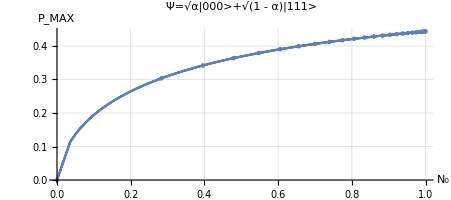

```mathematica
ParametricPlot[{N0[x],FindMaxP[x]},{x,0,1},AxesOrigin->{0,0},AxesLabel->{Style[Subscript[N, 0],Large,Bold,Red],Style[Subscript[P, MAX],Large,Bold,Blue]},LabelStyle->Directive[Orange,Bold],Axes->True,Mesh->Full,GridLines->Automatic,PlotLabel->"Ψ=√α|000>+√(1 - α)|111>"]
```

### γ= c_1|000>+c_2/(√3)(|100>+|010>+|001>)+c_3|111>

#### 求本征值

```mathematica
up= {{1},{0}};(*|0>*)
down= {{0},{1}};(*|1>*)
γ=x* KroneckerProduct[up,up,up]+y/(√3)* (KroneckerProduct[down,up,up]+KroneckerProduct[up,down,up]+KroneckerProduct[up,up,down])+z* KroneckerProduct[down,down,down];
ρForγ=γ.Transpose[γ];
PPT[ρForγ];
EvForρForγ=Eigenvalues[PPT[ρForγ]];
A00=({{1-p/2, 0}, {0, p/2}});
A01=({{0, 1-p}, {0, 0}});
A10=({{0, 0}, {1-p, 0}});
A11=({{p/2, 0}, {0, 1-p/2}}); 
ρ1Forγ= Gen[ρForγ,A00,A01,A10,A11];
EvForρ1Forγ=Eigenvalues[PPT[ρ1Forγ]];
```

#### N0 and FindMaxP

```mathematica
N0[θθ_,ϕϕ_]:=
Module[{ev,x=Sin[θθ]Cos[ϕϕ],y=Sin[θθ]Sin[ϕϕ],z =Cos[θθ],i,sum},
(
ev={0,0,0,0,-1/3 √(2 y^4+9 x^2 z^2+6 y^2 z^2),1/3 √(2 y^4+9 x^2 z^2+6 y^2 z^2),1/6 (3 x^2+3 y^2+3 z^2-√(9 x^4+18 x^2 y^2+y^4-18 x^2 z^2-6 y^2 z^2+9 z^4)),1/6 (3 x^2+3 y^2+3 z^2+√(9 x^4+18 x^2 y^2+y^4-18 x^2 z^2-6 y^2 z^2+9 z^4))};
 Evaluate[ev];
sum=0;
For[i=1,i≤8,i++,(If[ev[[i]]<0,sum=sum+ev[[i]]])];
Return[ -2*sum];
)
]
FindMaxP[θθ_,ϕϕ_,accuracyy_]:=
Module[{Ev,p,mid,x=Sin[θθ]Cos[ϕϕ],y=Sin[θθ]Sin[ϕϕ],z =Cos[θθ],PPTForρ,Header ,Tail,minev,accuracy=accuracyy},(
Ev={1/3072(768 p x^2-384 p^2 x^2+768 p y^2-384 p^2 y^2+768 p z^2-384 p^2 z^2-128 √(36 p^2 x^4-108 p^3 x^4+117 p^4 x^4-54 p^5 x^4+9 p^6 x^4+72 p^2 x^2 y^2-216 p^3 x^2 y^2+234 p^4 x^2 y^2-108 p^5 x^2 y^2+18 p^6 x^2 y^2+4 p^2 y^4-12 p^3 y^4+13 p^4 y^4-6 p^5 y^4+p^6 y^4-72 p^2 x^2 z^2+216 p^3 x^2 z^2-234 p^4 x^2 z^2+108 p^5 x^2 z^2-18 p^6 x^2 z^2-24 p^2 y^2 z^2+72 p^3 y^2 z^2-78 p^4 y^2 z^2+36 p^5 y^2 z^2-6 p^6 y^2 z^2+36 p^2 z^4-108 p^3 z^4+117 p^4 z^4-54 p^5 z^4+9 p^6 z^4)),1/3072(768 p x^2-384 p^2 x^2+768 p y^2-384 p^2 y^2+768 p z^2-384 p^2 z^2+128 √(36 p^2 x^4-108 p^3 x^4+117 p^4 x^4-54 p^5 x^4+9 p^6 x^4+72 p^2 x^2 y^2-216 p^3 x^2 y^2+234 p^4 x^2 y^2-108 p^5 x^2 y^2+18 p^6 x^2 y^2+4 p^2 y^4-12 p^3 y^4+13 p^4 y^4-6 p^5 y^4+p^6 y^4-72 p^2 x^2 z^2+216 p^3 x^2 z^2-234 p^4 x^2 z^2+108 p^5 x^2 z^2-18 p^6 x^2 z^2-24 p^2 y^2 z^2+72 p^3 y^2 z^2-78 p^4 y^2 z^2+36 p^5 y^2 z^2-6 p^6 y^2 z^2+36 p^2 z^4-108 p^3 z^4+117 p^4 z^4-54 p^5 z^4+9 p^6 z^4)),1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x^4 y^8+2973747944575991808 p^9 x^4 y^8-6011302747935080448 p^10 x^4 y^8+7443394652880764928 p^11 x^4 y^8-6326537129664970752 p^12 x^4 y^8+3832805175450402816 p^13 x^4 y^8-1663312603197210624 p^14 x^4 y^8+507030991055880192 p^15 x^4 y^8-103290321336532992 p^16 x^4 y^8+12635450187448320 p^17 x^4 y^8-701969454858240 p^18 x^4 y^8-108086391056891904 p^4 x^2 y^10+1040331513922584576 p^5 x^2 y^10-4532873024948404224 p^6 x^2 y^10+12240783787193008128 p^7 x^2 y^10-23165953533240410112 p^8 x^2 y^10+32626257131741380608 p^9 x^2 y^10-35251890898870468608 p^10 x^2 y^10+29612926768565452800 p^11 x^2 y^10-19370157919180947456 p^12 x^2 y^10+9783586405346181120 p^13 x^2 y^10-3743797510158680064 p^14 x^2 y^10+1049475052619169792 p^15 x^2 y^10-203242525371138048 p^16 x^2 y^10+24291235514548224 p^17 x^2 y^10-1349513084141568 p^18 x^2 y^10-36028797018963968 p^3 y^12+333266372425416704 p^4 y^12-1398367684298539008 p^5 y^12+3574732204225331200 p^6 y^12-6238048433861558272 p^7 y^12+7834152289299333120 p^8 y^12-7227116317650714624 p^9 y^12+4864995905280933888 p^10 y^12-2277414036565917696 p^11 y^12+619051434716954624 p^12 y^12+8712530138497024 p^13 y^12-91455178175152128 p^14 y^12+42592881436786688 p^15 y^12-10295277126680576 p^16 y^12+1347039182979072 p^17 y^12-74835510165504 p^18 y^12+273593677362757632 √3 p^7 x^8 y^3 z-2051952580220682240 √3 p^8 x^8 y^3 z+6908240353409630208 √3 p^9 x^8 y^3 z-13782281497148915712 √3 p^10 x^8 y^3 z+18108481520447520768 √3 p^11 x^8 y^3 z-16458369653853388800 √3 p^12 x^8 y^3 z+10563280886927720448 √3 p^13 x^8 y^3 z-4790026804452655104 √3 p^14 x^8 y^3 z+1504765225495166976 √3 p^15 x^8 y^3 z-312067788241895424 √3 p^16 x^8 y^3 z+38474110879137792 √3 p^17 x^8 y^3 z-2137450604396544 √3 p^18 x^8 y^3 z+820781032088272896 √3 p^7 x^6 y^5 z-6155857740662046720 √3 p^8 x^6 y^5 z+20724721060228890624 √3 p^9 x^6 y^5 z-41346844491446747136 √3 p^10 x^6 y^5 z+54325444561342562304 √3 p^11 x^6 y^5 z-49375108961560166400 √3 p^12 x^6 y^5 z+31689842660783161344 √3 p^13 x^6 y^5 z-14370080413357965312 √3 p^14 x^6 y^5 z+4514295676485500928 √3 p^15 x^6 y^5 z-936203364725686272 √3 p^16 x^6 y^5 z+115422332637413376 √3 p^17 x^6 y^5 z-6412351813189632 √3 p^18 x^6 y^5 z-324259173170675712 √3 p^4 x^4 y^7 z+3242591731706757120 √3 p^5 x^4 y^7 z-14632195189326741504 √3 p^6 x^4 y^7 z+40096673382386368512 √3 p^7 x^4 y^7 z-75638518691640901632 √3 p^8 x^4 y^7 z+105275300464482582528 √3 p^9 x^4 y^7 z-112539465925942837248 √3 p^10 x^4 y^7 z+94211856136126070784 √3 p^11 x^4 y^7 z-61925585591879073792 √3 p^12 x^4 y^7 z+31610044504885690368 √3 p^13 x^4 y^7 z-12246562820308598784 √3 p^14 x^4 y^7 z+3470586462842388480 √3 p^15 x^4 y^7 z-677176017407705088 √3 p^16 x^4 y^7 z+81223122967068672 √3 p^17 x^4 y^7 z-4512395720392704 √3 p^18 x^4 y^7 z-216172782113783808 √3 p^3 x^2 y^9 z+2161727821137838080 √3 p^4 x^2 y^9 z-9889904781705609216 √3 p^5 x^2 y^9 z+27548518920625324032 √3 p^6 x^2 y^9 z-52323946370697265152 √3 p^7 x^2 y^9 z+71706876216946458624 √3 p^8 x^2 y^9 z-72940581039869263872 √3 p^9 x^2 y^9 z+55591448637842915328 √3 p^10 x^2 y^9 z-31500638699875467264 √3 p^11 x^2 y^9 z+12874630250373316608 √3 p^12 x^2 y^9 z-3513704910837252096 √3 p^13 x^2 y^9 z+495017727010799616 √3 p^14 x^2 y^9 z+28710447624486912 √3 p^15 x^2 y^9 z-26018843159691264 √3 p^16 x^2 y^9 z+4274901208793088 √3 p^17 x^2 y^9 z-237494511599616 √3 p^18 x^2 y^9 z+615585774066204672 p^7 x^10 z^2-4052606345935847424 p^8 x^10 z^2+12311715481324093440 p^9 x^10 z^2-22674076011438538752 p^10 x^10 z^2+28021977423638691840 p^11 x^10 z^2-24328462779241463808 p^12 x^10 z^2+15104294695968178176 p^13 x^10 z^2-6692892205016678400 p^14 x^10 z^2+2071189635660251136 p^15 x^10 z^2-425820237594624000 p^16 x^10 z^2+52300744476327936 p^17 x^10 z^2-2905596915351552 p^18 x^10 z^2+2462343096264818688 p^7 x^8 y^2 z^2-15834234077369597952 p^8 x^8 y^2 z^2+47143610530570174464 p^9 x^8 y^2 z^2-85369777139597967360 p^10 x^8 y^2 z^2+104068195026858934272 p^11 x^8 y^2 z^2-89383909374654676992 p^12 x^8 y^2 z^2+55045765415024197632 p^13 x^8 y^2 z^2-24250445832180989952 p^14 x^8 y^2 z^2+7475733488876912640 p^15 x^8 y^2 z^2-1533487217991745536 p^16 x^8 y^2 z^2+188162448518283264 p^17 x^8 y^2 z^2-10453469362126848 p^18 x^8 y^2 z^2-729583139634020352 p^4 x^6 y^4 z^2+7113435611431698432 p^5 x^6 y^4 z^2-31372075004262875136 p^6 x^6 y^4 z^2+87823570433445199872 p^7 x^6 y^4 z^2-177847290022349242368 p^8 x^6 y^4 z^2+275166841007593488384 p^9 x^6 y^4 z^2-331065449213771907072 p^10 x^6 y^4 z^2+309719442511198420992 p^11 x^6 y^4 z^2-223417736908083560448 p^12 x^6 y^4 z^2+122530068380566683648 p^13 x^6 y^4 z^2-50008506823996342272 p^14 x^6 y^4 z^2+14682860685134659584 p^15 x^6 y^4 z^2-2927550314267541504 p^16 x^6 y^4 z^2+354683209667051520 p^17 x^6 y^4 z^2-19704622759280640 p^18 x^6 y^4 z^2-1459166279268040704 p^3 x^4 y^6 z^2+15807634692070440960 p^4 x^4 y^6 z^2-79159770650291208192 p^5 x^4 y^6 z^2+243984761612610306048 p^6 x^4 y^6 z^2-512562554890384048128 p^7 x^4 y^6 z^2+766290291346857000960 p^8 x^4 y^6 z^2-826347903440167895040 p^9 x^4 y^6 z^2+635218020373075329024 p^10 x^4 y^6 z^2-329651881880730992640 p^11 x^4 y^6 z^2+94103875298185445376 p^12 x^4 y^6 z^2+5599170605472546816 p^13 x^4 y^6 z^2-18631444434989875200 p^14 x^4 y^6 z^2+8658337409387200512 p^15 x^4 y^6 z^2-2107407548679192576 p^16 x^4 y^6 z^2+276399081281028096 p^17 x^4 y^6 z^2-15355504515612672 p^18 x^4 y^6 z^2-486388759756013568 p^3 x^2 y^8 z^2+5390808753962483712 p^4 x^2 y^8 z^2-27501231124537933824 p^5 x^2 y^8 z^2+88188362003262210048 p^6 x^2 y^8 z^2-199062199754519740416 p^7 x^2 y^8 z^2+332670278793487712256 p^8 x^2 y^8 z^2-421975181660616916992 p^9 x^2 y^8 z^2+411595088206969700352 p^10 x^2 y^8 z^2-310751276999261552640 p^11 x^2 y^8 z^2+181922062522701053952 p^12 x^2 y^8 z^2-82300991807963529216 p^13 x^2 y^8 z^2+28453960149029093376 p^14 x^2 y^8 z^2-7334384672056541184 p^15 x^2 y^8 z^2+1339436884706721792 p^16 x^2 y^8 z^2-155477266359386112 p^17 x^2 y^8 z^2+8637625908854784 p^18 x^2 y^8 z^2-432345564227567616 p^2 y^10 z^2+4539628424389459968 p^3 y^10 z^2-21914515786784833536 p^4 y^10 z^2+64824813036370919424 p^5 y^10 z^2-131372252930211053568 p^6 y^10 z^2+192684258257232986112 p^7 y^10 z^2-210241963617001930752 p^8 y^10 z^2+172255297028782817280 p^9 y^10 z^2-105036011549906436096 p^10 y^10 z^2+45823774364773908480 p^11 y^10 z^2-12556757040736763904 p^12 y^10 z^2+821810174971871232 p^13 y^10 z^2+1005591344531374080 p^14 y^10 z^2-510415287846174720 p^15 y^10 z^2+124887478485123072 p^16 y^10 z^2-16409386410835968 p^17 y^10 z^2+911632578379776 p^18 y^10 z^2-1459166279268040704 √3 p^3 x^6 y^3 z^3+16780412211582468096 √3 p^4 x^6 y^3 z^3-88279559895716462592 √3 p^5 x^6 y^3 z^3+283260653962908401664 √3 p^6 x^6 y^3 z^3-622243220215365107712 √3 p^7 x^6 y^3 z^3+994148225643806982144 √3 p^8 x^6 y^3 z^3-1196470750053566251008 √3 p^9 x^6 y^3 z^3+1107450207281658986496 √3 p^10 x^6 y^3 z^3-797291874913024475136 √3 p^11 x^6 y^3 z^3+448226241676094472192 √3 p^12 x^6 y^3 z^3-196173791504445210624 √3 p^13 x^6 y^3 z^3+66063610797153583104 √3 p^14 x^6 y^3 z^3-16689214319128215552 √3 p^15 x^6 y^3 z^3+3005255549781540864 √3 p^16 x^6 y^3 z^3-346266997912240128 √3 p^17 x^6 y^3 z^3+19237055439568896 √3 p^18 x^6 y^3 z^3-1459166279268040704 √3 p^3 x^4 y^5 z^3+17266800971338481664 √3 p^4 x^4 y^5 z^3-92778655923459588096 √3 p^5 x^4 y^5 z^3+303749780467630473216 √3 p^6 x^4 y^5 z^3-683254610267260059648 √3 p^7 x^4 y^5 z^3+1125640386914096775168 √3 p^8 x^4 y^5 z^3-1410071413830168084480 √3 p^9 x^4 y^5 z^3+1372866473621018640384 √3 p^10 x^4 y^5 z^3-1050318527571255361536 √3 p^11 x^4 y^5 z^3+632564731689484419072 √3 p^12 x^4 y^5 z^3-297746869192438579200 √3 p^13 x^4 y^5 z^3+107601638370438021120 √3 p^14 x^4 y^5 z^3-28894532259255681024 √3 p^15 x^4 y^5 z^3+5439574293677604864 √3 p^16 x^4 y^5 z^3-641235181318963200 √3 p^17 x^4 y^5 z^3+35624176739942400 √3 p^18 x^4 y^5 z^3-648518346341351424 √3 p^2 x^2 y^7 z^3+5836665117072162816 √3 p^3 x^2 y^7 z^3-21238975842679259136 √3 p^4 x^2 y^7 z^3+33925615992981946368 √3 p^5 x^2 y^7 z^3+10396559739784790016 √3 p^6 x^2 y^7 z^3-168787032734498291712 √3 p^7 x^2 y^7 z^3+405247968219632762880 √3 p^8 x^2 y^7 z^3-576132552480578863104 √3 p^9 x^2 y^7 z^3+564228694240508510208 √3 p^10 x^2 y^7 z^3-399021812103537229824 √3 p^11 x^2 y^7 z^3+206686406895565012992 √3 p^12 x^2 y^7 z^3-78245416780632686592 √3 p^13 x^2 y^7 z^3+21399126308334600192 √3 p^14 x^2 y^7 z^3-4169770304991657984 √3 p^15 x^2 y^7 z^3+575528366443069440 √3 p^16 x^2 y^7 z^3-55573715714310144 √3 p^17 x^2 y^7 z^3+3087428650795008 √3 p^18 x^2 y^7 z^3-1641562064176545792 p^3 x^8 z^4+17236401673853730816 p^4 x^8 z^4-83309274756959698944 p^5 x^8 z^4+248081066948680482816 p^6 x^8 z^4-511038790103960911872 p^7 x^8 z^4+773021835783636516864 p^8 x^8 z^4-888341570792038858752 p^9 x^8 z^4+790976420860567486464 p^10 x^8 z^4-551327596546231369728 p^11 x^8 z^4+301742833097357918208 p^12 x^8 z^4-129172018012845244416 p^13 x^8 z^4+42721492411399274496 p^14 x^8 z^4-10639694746034896896 p^15 x^8 z^4+1896453048750833664 p^16 x^8 z^4-217318610668879872 p^17 x^8 z^4+12073256148271104 p^18 x^8 z^4-3283124128353091584 p^3 x^6 y^2 z^4+32284053928805400576 p^4 x^6 y^2 z^4-145278242679624302592 p^5 x^6 y^2 z^4+402045908884572340224 p^6 x^6 y^2 z^4-769687412840777908224 p^7 x^6 y^2 z^4+1083191567888827809792 p^8 x^6 y^2 z^4-1160327885300290289664 p^9 x^6 y^2 z^4+965623234844600303616 p^10 x^6 y^2 z^4-631159239169837891584 p^11 x^6 y^2 z^4+325181047699868221440 p^12 x^6 y^2 z^4-131614589691019395072 p^13 x^6 y^2 z^4+41368753360141811712 p^14 x^6 y^2 z^4-9860059638081257472 p^15 x^6 y^2 z^4+1699540411820802048 p^16 x^6 y^2 z^4-191168238430715904 p^17 x^6 y^2 z^4+10620457690595328 p^18 x^6 y^2 z^4-729583139634020352 p^2 x^4 y^4 z^4+2735936773627576320 p^3 x^4 y^4 z^4+9758174492605022208 p^4 x^4 y^4 z^4-92611459787293458432 p^5 x^4 y^4 z^4+309229253839256813568 p^6 x^4 y^4 z^4-623120999930237288448 p^7 x^4 y^4 z^4+857368486567263338496 p^8 x^4 y^4 z^4-841195110327329488896 p^9 x^4 y^4 z^4+590447929991431716864 p^10 x^4 y^4 z^4-283824228438934290432 p^11 x^4 y^4 z^4+77742997141343698944 p^12 x^4 y^4 z^4+2098442130866307072 p^13 x^4 y^4 z^4-12435242314169843712 p^14 x^4 y^4 z^4+5760073137081286656 p^15 x^4 y^4 z^4-1392192826996948992 p^16 x^4 y^4 z^4+182150868693417984 p^17 x^4 y^4 z^4-10119492705189888 p^18 x^4 y^4 z^4-1945555039024054272 p^2 x^2 y^6 z^4+18482772870728515584 p^3 x^2 y^6 z^4-82686089158522306560 p^4 x^2 y^6 z^4+236567333026331099136 p^5 x^2 y^6 z^4-491982230493207724032 p^6 x^2 y^6 z^4+795412818337248313344 p^7 x^2 y^6 z^4-1034404495337988292608 p^8 x^2 y^6 z^4+1095936473359309602816 p^9 x^2 y^6 z^4-945904540535507386368 p^10 x^2 y^6 z^4+660712581204270907392 p^11 x^2 y^6 z^4-369797004143483682816 p^12 x^2 y^6 z^4+163654380514644590592 p^13 x^2 y^6 z^4-56162820850332991488 p^14 x^2 y^6 z^4+14478377910647390208 p^15 x^2 y^6 z^4-2649815326358765568 p^16 x^2 y^6 z^4+307926477695877120 p^17 x^2 y^6 z^4-17107026538659840 p^18 x^2 y^6 z^4-1297036692682702848 p^2 y^8 z^4+12646107753656352768 p^3 y^8 z^4-55529383405478215680 p^4 y^8 z^4+144903318010645708800 p^5 y^8 z^4-247571878715810906112 p^6 y^8 z^4+284973147721216032768 p^7 y^8 z^4-214687438661681676288 p^8 y^8 z^4+90260264122457260032 p^9 y^8 z^4-2490050789284773888 p^10 y^8 z^4-17452680009083781120 p^11 y^8 z^4+3914384540184870912 p^12 y^8 z^4+6198488005494177792 p^13 y^8 z^4-5800348248006721536 p^14 y^8 z^4+2444036227662348288 p^15 y^8 z^4-581663641326059520 p^16 y^8 z^4+75690243017146368 p^17 y^8 z^4-4205013500952576 p^18 y^8 z^4-2918332558536081408 √3 p^2 x^4 y^3 z^5+33560824423164936192 √3 p^3 x^4 y^3 z^5-178747869210334986240 √3 p^4 x^4 y^3 z^5+587679218975203393536 √3 p^5 x^4 y^3 z^5-1340244227507695386624 √3 p^6 x^4 y^3 z^5+2257239036135204716544 √3 p^7 x^4 y^3 z^5-2916463001740769230848 √3 p^8 x^4 y^3 z^5+2961856752709873434624 √3 p^9 x^4 y^3 z^5-2400123334137904889856 √3 p^10 x^4 y^3 z^5+1563798761254460325888 √3 p^11 x^4 y^3 z^5-819646758300873129984 √3 p^12 x^4 y^3 z^5+343022347894766174208 √3 p^13 x^4 y^3 z^5-112621559862119104512 √3 p^14 x^4 y^3 z^5+28088950875909783552 √3 p^15 x^4 y^3 z^5-5025858854471073792 √3 p^16 x^4 y^3 z^5+577111663187066880 √3 p^17 x^4 y^3 z^5-32061759065948160 √3 p^18 x^4 y^3 z^5-1945555039024054272 √3 p^2 x^2 y^5 z^5+23346660468288651264 √3 p^3 x^2 y^5 z^5-129379410095099609088 √3 p^4 x^2 y^5 z^5+441397799478582312960 √3 p^5 x^2 y^5 z^5-1040385557118113021952 √3 p^6 x^2 y^5 z^5+1798756831470192427008 √3 p^7 x^2 y^5 z^5-2360216656364798214144 √3 p^8 x^2 y^5 z^5+2395958630382494023680 √3 p^9 x^2 y^5 z^5-1899519102895584706560 √3 p^10 x^2 y^5 z^5+1178696660805450989568 √3 p^11 x^2 y^5 z^5-570455167015952842752 √3 p^12 x^2 y^5 z^5+213549839951119515648 √3 p^13 x^2 y^5 z^5-61072901130399252480 √3 p^14 x^2 y^5 z^5+13117296864669990912 √3 p^15 x^2 y^5 z^5-2055277503383076864 √3 p^16 x^2 y^5 z^5+218019961648447488 √3 p^17 x^2 y^5 z^5-12112220091580416 √3 p^18 x^2 y^5 z^5-3283124128353091584 p^2 x^6 z^6+36114365411884007424 p^3 x^6 z^6-184675732219861401600 p^4 x^6 z^6+585216875878938574848 p^5 x^6 z^6-1288831415636610514944 p^6 x^6 z^6+2095043584405316567040 p^7 x^6 z^6-2605210294662683688960 p^8 x^6 z^6+2534469229459575668736 p^9 x^6 z^6-1955985322984486207488 p^10 x^6 z^6+1206471168948002881536 p^11 x^6 z^6-595659390806717890560 p^12 x^6 z^6+234195119097218334720 p^13 x^6 z^6-72316900661199372288 p^14 x^6 z^6+17069680526710800384 p^15 x^6 z^6-2926837830732742656 p^16 x^6 z^6+328232258437644288 p^17 x^6 z^6-18235125468758016 p^18 x^6 z^6-2188749418902061056 p^2 x^4 y^2 z^6+22981868898471641088 p^3 x^4 y^2 z^6-112720595073456144384 p^4 x^4 y^2 z^6+344454439799711858688 p^5 x^4 y^2 z^6-730221524881200119808 p^6 x^4 y^2 z^6+1128231927024671784960 p^7 x^4 y^2 z^6-1297860006989581516800 p^8 x^4 y^2 z^6+1113132975955214598144 p^9 x^4 y^2 z^6-695594825089976107008 p^10 x^4 y^2 z^6+292937605332546355200 p^11 x^4 y^2 z^6-58955162570465476608 p^12 x^4 y^2 z^6-16989526129045929984 p^13 x^4 y^2 z^6+18864604671752798208 p^14 x^4 y^2 z^6-7607186701047300096 p^15 x^4 y^2 z^6+1749503319698571264 p^16 x^4 y^2 z^6-224833085449961472 p^17 x^4 y^2 z^6+12490726969442304 p^18 x^4 y^2 z^6-4377498837804122112 p^3 x^2 y^4 z^6+44139779947858231296 p^4 x^2 y^4 z^6-205560049591885234176 p^5 x^2 y^4 z^6+591965519920553263104 p^6 x^2 y^4 z^6-1181924686207112970240 p^7 x^2 y^4 z^6+1732338166378197417984 p^8 x^2 y^4 z^6-1922109580838940180480 p^9 x^2 y^4 z^6+1640547487622992232448 p^10 x^2 y^4 z^6-1084337241412784357376 p^11 x^2 y^4 z^6+555068847587460120576 p^12 x^2 y^4 z^6-218966139782660358144 p^13 x^2 y^4 z^6+65929663892611399680 p^14 x^2 y^4 z^6-14905155547991900160 p^15 x^2 y^4 z^6+2446356746952769536 p^16 x^2 y^4 z^6-267314916212342784 p^17 x^2 y^4 z^6+14850828678463488 p^18 x^2 y^4 z^6-1215971899390033920 p^4 y^6 z^6+11916524614022332416 p^5 y^6 z^6-50888423989472919552 p^6 y^6 z^6+127008264891289042944 p^7 y^6 z^6-205962840283558182912 p^8 y^6 z^6+224647008500123172864 p^9 y^6 z^6-160510190675577274368 p^10 y^6 z^6+62614952994215559168 p^11 y^6 z^6+4398398354824888320 p^12 y^6 z^6-22599502734796259328 p^13 y^6 z^6+15064989354298441728 p^14 y^6 z^6-5570433769568993280 p^15 y^6 z^6+1248241466153631744 p^16 y^6 z^6-158839298039218176 p^17 y^6 z^6+8824405446623232 p^18 y^6 z^6+1459166279268040704 √3 p^4 x^2 y^3 z^7-14226871222863396864 √3 p^5 x^2 y^3 z^7+64385712072702296064 √3 p^6 x^2 y^3 z^7-179386254457514754048 √3 p^7 x^2 y^3 z^7+344044049283667722240 √3 p^8 x^2 y^3 z^7-481068882696182169600 √3 p^9 x^2 y^3 z^7+506558693637145755648 √3 p^10 x^2 y^3 z^7-408902850423476453376 √3 p^11 x^2 y^3 z^7+254906659212053446656 √3 p^12 x^2 y^3 z^7-122460244994156396544 √3 p^13 x^2 y^3 z^7+44747528403041648640 √3 p^14 x^2 y^3 z^7-12083720750188462080 √3 p^15 x^2 y^3 z^7+2281372278425911296 √3 p^16 x^2 y^3 z^7-269318776153964544 √3 p^17 x^2 y^3 z^7+14962154230775808 √3 p^18 x^2 y^3 z^7-1641562064176545792 p^3 x^4 z^8+17236401673853730816 p^4 x^4 z^8-83309274756959698944 p^5 x^4 z^8+248081066948680482816 p^6 x^4 z^8-511038790103960911872 p^7 x^4 z^8+773021835783636516864 p^8 x^4 z^8-888341570792038858752 p^9 x^4 z^8+790976420860567486464 p^10 x^4 z^8-551327596546231369728 p^11 x^4 z^8+301742833097357918208 p^12 x^4 z^8-129172018012845244416 p^13 x^4 z^8+42721492411399274496 p^14 x^4 z^8-10639694746034896896 p^15 x^4 z^8+1896453048750833664 p^16 x^4 z^8-217318610668879872 p^17 x^4 z^8+12073256148271104 p^18 x^4 z^8-2188749418902061056 p^4 x^2 y^2 z^8+21340306834295095296 p^5 x^2 y^2 z^8-94116225012788625408 p^6 x^2 y^2 z^8+252390167367143915520 p^7 x^2 y^2 z^8-462852103678445223936 p^8 x^2 y^2 z^8+616355256283787427840 p^9 x^2 y^2 z^8-616329606876534669312 p^10 x^2 y^2 z^8+471495953922624847872 p^11 x^2 y^2 z^8-278304618494847614976 p^12 x^2 y^2 z^8+126729446334671093760 p^13 x^2 y^2 z^8-44074231462656737280 p^14 x^2 y^2 z^8+11419329853988536320 p^15 x^2 y^2 z^8-2093365685680865280 p^16 x^2 y^2 z^8+243468982907043840 p^17 x^2 y^2 z^8-13526054605946880 p^18 x^2 y^2 z^8-182395784908505088 p^5 y^4 z^8+1550364171722293248 p^6 y^4 z^8-4240701999122743296 p^7 y^4 z^8+2428143886594473984 p^8 y^4 z^8+13084047633046044672 p^9 y^4 z^8-39817854825768419328 p^10 y^4 z^8+59170332597974728704 p^11 y^4 z^8-56330373228266520576 p^12 y^4 z^8+36849292178029019136 p^13 y^4 z^8-16847207542969860096 p^14 y^4 z^8+5312099114576510976 p^15 y^4 z^8-1103592465182490624 p^16 y^4 z^8+136162283033198592 p^17 y^4 z^8-7564571279622144 p^18 y^4 z^8+615585774066204672 p^7 x^2 z^10-4052606345935847424 p^8 x^2 z^10+12311715481324093440 p^9 x^2 z^10-22674076011438538752 p^10 x^2 z^10+28021977423638691840 p^11 x^2 z^10-24328462779241463808 p^12 x^2 z^10+15104294695968178176 p^13 x^2 z^10-6692892205016678400 p^14 x^2 z^10+2071189635660251136 p^15 x^2 z^10-425820237594624000 p^16 x^2 z^10+52300744476327936 p^17 x^2 z^10-2905596915351552 p^18 x^2 z^10+376191306373791744 p^8 y^2 z^10-2103251394726199296 p^9 y^2 z^10+5326526906156187648 p^10 y^2 z^10-8019714667695833088 p^11 y^2 z^10+7929941742311178240 p^12 y^2 z^10-5371413368848515072 p^13 y^2 z^10+2521122987885723648 p^14 y^2 z^10-809025053764091904 p^15 y^2 z^10+169793732386750464 p^16 y^2 z^10-21040529387028480 p^17 y^2 z^10+1168918299279360 p^18 y^2 z^10+25649407252758528 p^9 z^12-115422332637413376 p^10 z^12+230844665274826752 p^11 z^12-269318776153964544 p^12 z^12+201989082115473408 p^13 z^12-100994541057736704 p^14 z^12+33664847019245568 p^15 z^12-7213895789838336 p^16 z^12+901736973729792 p^17 z^12-50096498540544 p^18 z^12+(-133590662774784 p^6 x^10+467567319711744 p^7 x^10-734748645261312 p^8 x^10+684652146720768 p^9 x^10-417470821171200 p^10 x^10+171163036680192 p^11 x^10-45921790328832 p^12 x^10+7305739370496 p^13 x^10-521838526464 p^14 x^10-667953313873920 p^6 x^8 y^2+2337836598558720 p^7 x^8 y^2-3673743226306560 p^8 x^8 y^2+3423260733603840 p^9 x^8 y^2-2087354105856000 p^10 x^8 y^2+855815183400960 p^11 x^8 y^2-229608951644160 p^12 x^8 y^2+36528696852480 p^13 x^8 y^2-2609192632320 p^14 x^8 y^2+118747255799808 p^4 x^6 y^4-1246846185897984 p^5 x^6 y^4+3324923162394624 p^6 x^6 y^4-4616299569217536 p^7 x^6 y^4+4178419063455744 p^8 x^6 y^4-2731186883395584 p^9 x^6 y^4+1330340350132224 p^10 x^6 y^4-474061310263296 p^11 x^6 y^4+116891829927936 p^12 x^6 y^4-17858474016768 p^13 x^6 y^4+1275605286912 p^14 x^6 y^4+158329674399744 p^3 x^4 y^6-1227054976598016 p^4 x^4 y^6+2988472604295168 p^5 x^4 y^6-3780120976293888 p^6 x^4 y^6+2785612708970496 p^7 x^4 y^6-1066251401035776 p^8 x^4 y^6-39582418599936 p^9 x^4 y^6+293775763046400 p^10 x^4 y^6-174719269601280 p^11 x^4 y^6+54425825574912 p^12 x^4 y^6-9199819948032 p^13 x^4 y^6+657129996288 p^14 x^4 y^6+422212465065984 p^3 x^2 y^8-3813106325127168 p^4 x^2 y^8+13768084603011072 p^5 x^2 y^8-28900113380278272 p^6 x^2 y^8+40373242338213888 p^7 x^2 y^8-39902376483618816 p^8 x^2 y^8+28636849064902656 p^9 x^2 y^8-14965040448798720 p^10 x^2 y^8+5586326522953728 p^11 x^2 y^8-1418009222578176 p^12 x^2 y^8+219803541307392 p^13 x^2 y^8-15700252950528 p^14 x^2 y^8+140737488355328 p y^10-1266637395197952 p^2 y^10+5365616743546880 p^3 y^10-14588320277331968 p^4 y^10+28365200973365248 p^5 y^10-41267420169502720 p^6 y^10+45781740035244032 p^7 y^10-38943602344198144 p^8 y^10+25293509082742784 p^9 y^10-12360847158411264 p^10 y^10+4413216335593472 p^11 y^10-1089392684826624 p^12 y^10+166528766967808 p^13 y^10-11894911926272 p^14 y^10+474989023199232 √3 p^3 x^6 y^3 z-4749890231992320 √3 p^4 x^6 y^3 z+20187033485967360 √3 p^5 x^6 y^3 z-49280111156920320 √3 p^6 x^6 y^3 z+77957573432573952 √3 p^7 x^6 y^3 z-84889444489887744 √3 p^8 x^6 y^3 z+65541063498006528 √3 p^9 x^6 y^3 z-36139985132322816 √3 p^10 x^6 y^3 z+14012176184377344 √3 p^11 x^6 y^3 z-3644056412356608 √3 p^12 x^6 y^3 z+571471168536576 √3 p^13 x^6 y^3 z-40819369181184 √3 p^14 x^6 y^3 z+949978046398464 √3 p^3 x^4 y^5 z-9499780463984640 √3 p^4 x^4 y^5 z+40374066971934720 √3 p^5 x^4 y^5 z-98560222313840640 √3 p^6 x^4 y^5 z+155915146865147904 √3 p^7 x^4 y^5 z-169778888979775488 √3 p^8 x^4 y^5 z+131082126996013056 √3 p^9 x^4 y^5 z-72279970264645632 √3 p^10 x^4 y^5 z+28024352368754688 √3 p^11 x^4 y^5 z-7288112824713216 √3 p^12 x^4 y^5 z+1142942337073152 √3 p^13 x^4 y^5 z-81638738362368 √3 p^14 x^4 y^5 z+422212465065984 √3 p x^2 y^7 z-3799912185593856 √3 p^2 x^2 y^7 z+15780190881841152 √3 p^3 x^2 y^7 z-41112938785800192 √3 p^4 x^2 y^7 z+76684338967609344 √3 p^5 x^2 y^7 z-109300251893956608 √3 p^6 x^2 y^7 z+121999611194769408 √3 p^7 x^2 y^7 z-106564117208236032 √3 p^8 x^2 y^7 z+71801682706563072 √3 p^9 x^2 y^7 z-36446748876472320 √3 p^10 x^2 y^7 z+13444828184444928 √3 p^11 x^2 y^7 z-3396666296107008 √3 p^12 x^2 y^7 z+525291680169984 √3 p^13 x^2 y^7 z-37520834297856 √3 p^14 x^2 y^7 z+1068725302198272 p^3 x^8 z^2-10152890370883584 p^4 x^8 z^2+39810017506885632 p^5 x^8 z^2-90574469361303552 p^6 x^8 z^2+135928499373342720 p^7 x^8 z^2-142808418506244096 p^8 x^8 z^2+107790966026403840 p^9 x^8 z^2-58629602125283328 p^10 x^8 z^2+22547599051456512 p^11 x^8 z^2-5836242079973376 p^12 x^8 z^2+913217421312000 p^13 x^8 z^2-65229815808000 p^14 x^8 z^2+3206175906594816 p^3 x^6 y^2 z^2-30102429345251328 p^4 x^6 y^2 z^2+115689513962962944 p^5 x^6 y^2 z^2-258408872027357184 p^6 x^6 y^2 z^2+382247416419581952 p^7 x^6 y^2 z^2-397521282196832256 p^8 x^6 y^2 z^2+298063033761005568 p^9 x^6 y^2 z^2-161461014796173312 p^10 x^6 y^2 z^2+61941537306574848 p^11 x^6 y^2 z^2-16010005991915520 p^12 x^6 y^2 z^2+2503433357623296 p^13 x^6 y^2 z^2-178816668401664 p^14 x^6 y^2 z^2+949978046398464 p x^4 y^4 z^2-8549802417586176 p^2 x^4 y^4 z^2+40017825204535296 p^3 x^4 y^4 z^2-134125025425883136 p^4 x^4 y^4 z^2+328603343612018688 p^5 x^4 y^4 z^2-584934138662879232 p^6 x^4 y^4 z^2+761719115734843392 p^7 x^4 y^4 z^2-732492447401115648 p^8 x^4 y^4 z^2+521693803245993984 p^9 x^4 y^4 z^2-272896037234933760 p^10 x^4 y^4 z^2+102257158363545600 p^11 x^4 y^4 z^2-26046004532871168 p^12 x^4 y^4 z^2+4044132615979008 p^13 x^4 y^4 z^2-288866615427072 p^14 x^4 y^4 z^2+1583296743997440 p x^2 y^6 z^2-14249670695976960 p^2 x^2 y^6 z^2+60046529016102912 p^3 x^2 y^6 z^2-164524322910633984 p^4 x^2 y^6 z^2+324605519333425152 p^5 x^2 y^6 z^2-477220482047803392 p^6 x^2 y^6 z^2+528623200402145280 p^7 x^2 y^6 z^2-442558652860071936 p^8 x^2 y^6 z^2+279464244821360640 p^9 x^2 y^6 z^2-131906554558414848 p^10 x^2 y^6 z^2+45518544439345152 p^11 x^2 y^6 z^2-10945621074640896 p^12 x^2 y^6 z^2+1650555931852800 p^13 x^2 y^6 z^2-117896852275200 p^14 x^2 y^6 z^2+1688849860263936 p y^8 z^2-15199648742375424 p^2 y^8 z^2+60534712178835456 p^3 y^8 z^2-142259212448169984 p^4 y^8 z^2+217175536718315520 p^5 y^8 z^2-219532339892453376 p^6 y^8 z^2+137267704535973888 p^7 y^8 z^2-33179137757675520 p^8 y^8 z^2-26053271617536000 p^9 y^8 z^2+32091652038328320 p^10 y^8 z^2-16816910087749632 p^11 y^8 z^2+5057736307900416 p^12 y^8 z^2-843767800135680 p^13 y^8 z^2+60269128581120 p^14 y^8 z^2+1899956092796928 √3 p x^4 y^3 z^3-17099604835172352 √3 p^2 x^4 y^3 z^3+65073496178294784 √3 p^3 x^4 y^3 z^3-132759431984185344 √3 p^4 x^4 y^3 z^3+139053036541575168 √3 p^5 x^4 y^3 z^3-9440406836084736 √3 p^6 x^4 y^3 z^3-199257895232077824 √3 p^7 x^4 y^3 z^3+330874384879190016 √3 p^8 x^4 y^3 z^3-304453120463732736 √3 p^9 x^4 y^3 z^3+184318006111764480 √3 p^10 x^4 y^3 z^3-75463881060777984 √3 p^11 x^4 y^3 z^3+20246407113867264 √3 p^12 x^4 y^3 z^3-3221019313569792 √3 p^13 x^4 y^3 z^3+230072808112128 √3 p^14 x^4 y^3 z^3+1266637395197952 √3 p x^2 y^5 z^3-11399736556781568 √3 p^2 x^2 y^5 z^3+42115693390331904 √3 p^3 x^2 y^5 z^3-78214859153473536 √3 p^4 x^2 y^5 z^3+54307078319112192 √3 p^5 x^2 y^5 z^3+80589804269469696 √3 p^6 x^2 y^5 z^3-265320951875371008 √3 p^7 x^2 y^5 z^3+363386393956712448 √3 p^8 x^2 y^5 z^3-313844049276567552 √3 p^9 x^2 y^5 z^3+184778151727988736 √3 p^10 x^2 y^5 z^3-74612859060879360 √3 p^11 x^2 y^5 z^3+19875321939492864 √3 p^12 x^2 y^5 z^3-3151750081019904 √3 p^13 x^2 y^5 z^3+225125005787136 √3 p^14 x^2 y^5 z^3+4274901208793088 p x^6 z^4-38474110879137792 p^2 x^6 z^4+154965168818749440 p^3 x^6 z^4-373519493118296064 p^4 x^6 z^4+598486169231032320 p^5 x^6 z^4-664212775316226048 p^6 x^6 z^4+511117875776323584 p^7 x^6 z^4-259065692785999872 p^8 x^6 z^4+69283457481572352 p^9 x^6 z^4+6003230408441856 p^10 x^6 z^4-13100234368352256 p^11 x^6 z^4+5080619893653504 p^12 x^6 z^4-920523160682496 p^13 x^6 z^4+65751654334464 p^14 x^6 z^4+7124835347988480 p x^4 y^2 z^4-64123518131896320 p^2 x^4 y^2 z^4+264331391410372608 p^3 x^4 y^2 z^4-675434390989307904 p^4 x^4 y^2 z^4+1197417640671313920 p^5 x^4 y^2 z^4-1552546152547614720 p^6 x^4 y^2 z^4+1511266637750206464 p^7 x^4 y^2 z^4-1117497026666299392 p^8 x^4 y^2 z^4+628961539176529920 p^9 x^4 y^2 z^4-267584880676700160 p^10 x^4 y^2 z^4+84443214567702528 p^11 x^4 y^2 z^4-18961524697595904 p^12 x^4 y^2 z^4+2751828496220160 p^13 x^4 y^2 z^4-196559178301440 p^14 x^4 y^2 z^4+9499780463984640 p x^2 y^4 z^4-85498024175861760 p^2 x^2 y^4 z^4+355173042097225728 p^3 x^2 y^4 z^4-919756869797412864 p^4 x^2 y^4 z^4+1667834894522253312 p^5 x^2 y^4 z^4-2243239565907197952 p^6 x^2 y^4 z^4+2305641248829997056 p^7 x^2 y^4 z^4-1834021679014084608 p^8 x^2 y^4 z^4+1127991315397607424 p^9 x^2 y^4 z^4-528764831243698176 p^10 x^2 y^4 z^4+183194545746345984 p^11 x^2 y^4 z^4-44328443361361920 p^12 x^2 y^4 z^4+6706668742115328 p^13 x^2 y^4 z^4-479047767293952 p^14 x^2 y^4 z^4+3799912185593856 p y^6 z^4-34199209670344704 p^2 y^6 z^4+139171783797374976 p^3 y^6 z^4-344050382470643712 p^4 y^6 z^4+578417883000864768 p^5 y^6 z^4-698639583893520384 p^6 y^6 z^4+623467623169916928 p^7 y^6 z^4-416149757950427136 p^8 y^6 z^4+208004372792082432 p^9 y^6 z^4-77268591958818816 p^10 y^6 z^4+21022902841245696 p^11 y^6 z^4-4094615661576192 p^12 y^6 z^4+540624713416704 p^13 y^6 z^4-38616050958336 p^14 y^6 z^4-4274901208793088 √3 p^3 x^2 y^3 z^5+35624176739942400 √3 p^4 x^2 y^3 z^5-135371871611781120 √3 p^5 x^2 y^3 z^5+309930337637498880 √3 p^6 x^2 y^3 z^5-475404638594531328 √3 p^7 x^2 y^3 z^5+513299856601645056 √3 p^8 x^2 y^3 z^5-398166970400243712 √3 p^9 x^2 y^3 z^5+221838428092760064 √3 p^10 x^2 y^3 z^5-86922991245459456 √3 p^11 x^2 y^3 z^5+22777208003100672 √3 p^12 x^2 y^3 z^5-3584682784456704 √3 p^13 x^2 y^3 z^5+256048770318336 √3 p^14 x^2 y^3 z^5+4274901208793088 p x^4 z^6-38474110879137792 p^2 x^4 z^6+154965168818749440 p^3 x^4 z^6-373519493118296064 p^4 x^4 z^6+598486169231032320 p^5 x^4 z^6-664212775316226048 p^6 x^4 z^6+511117875776323584 p^7 x^4 z^6-259065692785999872 p^8 x^4 z^6+69283457481572352 p^9 x^4 z^6+6003230408441856 p^10 x^4 z^6-13100234368352256 p^11 x^4 z^6+5080619893653504 p^12 x^4 z^6-920523160682496 p^13 x^4 z^6+65751654334464 p^14 x^4 z^6+2849934139195392 p x^2 y^2 z^6-25649407252758528 p^2 x^2 y^2 z^6+109366222591623168 p^3 x^2 y^2 z^6-301914897871011840 p^4 x^2 y^2 z^6+598931471440281600 p^5 x^2 y^2 z^6-888333377231388672 p^6 x^2 y^2 z^6+1000148761973882880 p^7 x^2 y^2 z^6-858431333880299520 p^8 x^2 y^2 z^6+559678081694957568 p^9 x^2 y^2 z^6-273588111085142016 p^10 x^2 y^2 z^6+97543448936054784 p^11 x^2 y^2 z^6-24042144591249408 p^12 x^2 y^2 z^6+3672351656902656 p^13 x^2 y^2 z^6-262310832635904 p^14 x^2 y^2 z^6+2374945115996160 p^3 y^4 z^6-22086989578764288 p^4 y^4 z^6+84548046129463296 p^5 y^4 z^6-186819120187047936 p^6 y^4 z^6+271085141583986688 p^7 y^4 z^6-274677246071930880 p^8 y^4 z^6+199966667915132928 p^9 y^4 z^6-105239755452579840 p^10 y^4 z^6+39406462379753472 p^11 y^4 z^6-10016516569300992 p^12 y^4 z^6+1553687239458816 p^13 y^4 z^6-110977659961344 p^14 y^4 z^6+1068725302198272 p^3 x^2 z^8-10152890370883584 p^4 x^2 z^8+39810017506885632 p^5 x^2 z^8-90574469361303552 p^6 x^2 z^8+135928499373342720 p^7 x^2 z^8-142808418506244096 p^8 x^2 z^8+107790966026403840 p^9 x^2 z^8-58629602125283328 p^10 x^2 z^8+22547599051456512 p^11 x^2 z^8-5836242079973376 p^12 x^2 z^8+913217421312000 p^13 x^2 z^8-65229815808000 p^14 x^2 z^8+356241767399424 p^4 y^2 z^8-3740538557693952 p^5 y^2 z^8+13314536056553472 p^6 y^2 z^8-25538081700446208 p^7 y^2 z^8+30903973321900032 p^8 y^2 z^8-25309864318205952 p^9 y^2 z^8+14427791579676672 p^10 y^2 z^8-5701259847794688 p^11 y^2 z^8+1498720248004608 p^12 y^2 z^8-236218906312704 p^13 y^2 z^8+16872779022336 p^14 y^2 z^8-133590662774784 p^6 z^10+467567319711744 p^7 z^10-734748645261312 p^8 z^10+684652146720768 p^9 z^10-417470821171200 p^10 z^10+171163036680192 p^11 z^10-45921790328832 p^12 z^10+7305739370496 p^13 z^10-521838526464 p^14 z^10) #1+(695784701952 p^4 x^8-2261300281344 p^5 x^8+3478923509760 p^6 x^8-3304977334272 p^7 x^8+2109097377792 p^8 x^8-924089057280 p^9 x^8+271790899200 p^10 x^8-48922361856 p^11 x^8+4076863488 p^12 x^8+2783138807808 p^4 x^6 y^2-9045201125376 p^5 x^6 y^2+13915694039040 p^6 x^6 y^2-13219909337088 p^7 x^6 y^2+8436389511168 p^8 x^6 y^2-3696356229120 p^9 x^6 y^2+1087163596800 p^10 x^6 y^2-195689447424 p^11 x^6 y^2+16307453952 p^12 x^6 y^2-309237645312 p^2 x^4 y^4+2937757630464 p^3 x^4 y^4-5334349381632 p^4 x^4 y^4+2241972928512 p^5 x^4 y^4+5315022028800 p^6 x^4 y^4-10398115823616 p^7 x^4 y^4+9315784065024 p^8 x^4 y^4-5037191331840 p^9 x^4 y^4+1686311534592 p^10 x^4 y^4-322525200384 p^11 x^4 y^4+26877100032 p^12 x^4 y^4-412316860416 p x^2 y^6+3092376453120 p^2 x^2 y^6-8452495638528 p^3 x^2 y^6+15616501088256 p^4 x^2 y^6-23270132809728 p^5 x^2 y^6+28114855919616 p^6 x^2 y^6-26053271617536 p^7 x^2 y^6+17626545782784 p^8 x^2 y^6-8351027036160 p^9 x^2 y^6+2615635083264 p^10 x^2 y^6-485599739904 p^11 x^2 y^6+40466644992 p^12 x^2 y^6-274877906944 y^8+1924145348608 p y^8-5531917877248 p^2 y^8+9088150798336 p^3 y^8-8504035246080 p^4 y^8+2218350608384 p^5 y^8+5714453987328 p^6 y^8-9481140305920 p^7 y^8+7795097206784 p^8 y^8-4003043737600 p^9 y^8+1300167131136 p^10 y^8-245417115648 p^11 y^8+20451426304 p^12 y^8-1236950581248 √3 p x^4 y^3 z+11132555231232 √3 p^2 x^4 y^3 z-42984032698368 √3 p^3 x^4 y^3 z+95554432401408 √3 p^4 x^4 y^3 z-137533442752512 √3 p^5 x^4 y^3 z+135948599820288 √3 p^6 x^4 y^3 z-95090575933440 √3 p^7 x^4 y^3 z+47603270025216 √3 p^8 x^4 y^3 z-17008070492160 √3 p^9 x^4 y^3 z+4252017623040 √3 p^10 x^4 y^3 z-695784701952 √3 p^11 x^4 y^3 z+57982058496 √3 p^12 x^4 y^3 z-1236950581248 √3 p x^2 y^5 z+11132555231232 √3 p^2 x^2 y^5 z-42984032698368 √3 p^3 x^2 y^5 z+95554432401408 √3 p^4 x^2 y^5 z-137533442752512 √3 p^5 x^2 y^5 z+135948599820288 √3 p^6 x^2 y^5 z-95090575933440 √3 p^7 x^2 y^5 z+47603270025216 √3 p^8 x^2 y^5 z-17008070492160 √3 p^9 x^2 y^5 z+4252017623040 √3 p^10 x^2 y^5 z-695784701952 √3 p^11 x^2 y^5 z+57982058496 √3 p^12 x^2 y^5 z-2783138807808 p x^6 z^2+23656679866368 p^2 x^6 z^2-83494164234240 p^3 x^6 z^2+174989852540928 p^4 x^6 z^2-247351461543936 p^5 x^6 z^2+249786708000768 p^6 x^6 z^2-184730838368256 p^7 x^6 z^2+100519146160128 p^8 x^6 z^2-39681471283200 p^9 x^6 z^2+10904250875904 p^10 x^6 z^2-1891664658432 p^11 x^6 z^2+157638721536 p^12 x^6 z^2-5566277615616 p x^4 y^2 z^2+46385646796800 p^2 x^4 y^2 z^2-158175055577088 p^3 x^4 y^2 z^2+324235671109632 p^4 x^4 y^2 z^2-456318800363520 p^5 x^4 y^2 z^2+466813552951296 p^6 x^4 y^2 z^2-354386341527552 p^7 x^4 y^2 z^2+199458281226240 p^8 x^4 y^2 z^2-81537269760000 p^9 x^4 y^2 z^2+23062363766784 p^10 x^4 y^2 z^2-4065991852032 p^11 x^4 y^2 z^2+338832654336 p^12 x^4 y^2 z^2-2473901162496 x^2 y^4 z^2+14534169329664 p x^2 y^4 z^2-25821343383552 p^2 x^2 y^4 z^2-4638564679680 p^3 x^2 y^4 z^2+107266808217600 p^4 x^2 y^4 z^2-240934780403712 p^5 x^2 y^4 z^2+313296389406720 p^6 x^2 y^4 z^2-276187871969280 p^7 x^2 y^4 z^2+171904723845120 p^8 x^2 y^4 z^2-75292118876160 p^9 x^2 y^4 z^2+22278398017536 p^10 x^2 y^4 z^2-4022505308160 p^11 x^2 y^4 z^2+335208775680 p^12 x^2 y^4 z^2-1649267441664 y^6 z^2+11544872091648 p y^6 z^2-31233002176512 p^2 y^6 z^2+43757126811648 p^3 y^6 z^2-31980326486016 p^4 y^6 z^2+11403138170880 p^5 y^6 z^2-10559177097216 p^6 y^6 z^2+25434796326912 p^7 y^6 z^2-30310121078784 p^8 y^6 z^2+19585050869760 p^9 y^6 z^2-7229235265536 p^10 y^6 z^2+1437471866880 p^11 y^6 z^2-119789322240 p^12 y^6 z^2+1236950581248 √3 p x^2 y^3 z^3-8658654068736 √3 p^2 x^2 y^3 z^3+31233002176512 √3 p^3 x^2 y^3 z^3-79164837199872 √3 p^4 x^2 y^3 z^3+151603755614208 √3 p^5 x^2 y^3 z^3-216118459367424 √3 p^6 x^2 y^3 z^3+222805723447296 √3 p^7 x^2 y^3 z^3-161905234673664 √3 p^8 x^2 y^3 z^3+80401787781120 √3 p^9 x^2 y^3 z^3-25898652794880 √3 p^10 x^2 y^3 z^3+4870492913664 √3 p^11 x^2 y^3 z^3-405874409472 √3 p^12 x^2 y^3 z^3-5566277615616 x^4 z^4+44530220924928 p x^4 z^4-155855773237248 p^2 x^4 z^4+331193518129152 p^3 x^4 z^4-486701399015424 p^4 x^4 z^4+534014758748160 p^5 x^4 z^4-460783418867712 p^6 x^4 z^4+320582801424384 p^7 x^4 z^4-177446842269696 p^8 x^4 z^4+74253273661440 p^9 x^4 z^4-21656298848256 p^10 x^4 z^4+3881174040576 p^11 x^4 z^4-323431170048 p^12 x^4 z^4-7421703487488 x^2 y^2 z^4+57518202028032 p x^2 y^2 z^4-195747429482496 p^2 x^2 y^2 z^4+403555127132160 p^3 x^2 y^2 z^4-555931976859648 p^4 x^2 y^2 z^4+522998167633920 p^5 x^2 y^2 z^4-322960065822720 p^6 x^2 y^2 z^4+108310485270528 p^7 x^2 y^2 z^4+4682051223552 p^8 x^2 y^2 z^4-23772643983360 p^9 x^2 y^2 z^4+11226776076288 p^10 x^2 y^2 z^4-2413503184896 p^11 x^2 y^2 z^4+201125265408 p^12 x^2 y^2 z^4-2473901162496 y^4 z^4+17317308137472 p y^4 z^4-49168785604608 p^2 y^4 z^4+75917841924096 p^3 y^4 z^4-59605556133888 p^4 y^4 z^4-4870492913664 p^5 y^4 z^4+72110353416192 p^6 y^4 z^4-94278827114496 p^7 y^4 z^4+70506183131136 p^8 y^4 z^4-34269812490240 p^9 y^4 z^4+10774999203840 p^10 y^4 z^4-2004004896768 p^11 y^4 z^4+167000408064 p^12 y^4 z^4-2783138807808 p x^2 z^6+23656679866368 p^2 x^2 z^6-83494164234240 p^3 x^2 z^6+174989852540928 p^4 x^2 z^6-247351461543936 p^5 x^2 z^6+249786708000768 p^6 x^2 z^6-184730838368256 p^7 x^2 z^6+100519146160128 p^8 x^2 z^6-39681471283200 p^9 x^2 z^6+10904250875904 p^10 x^2 z^6-1891664658432 p^11 x^2 z^6+157638721536 p^12 x^2 z^6-927712935936 p^2 y^2 z^6+8813272891392 p^3 y^2 z^6-25744033972224 p^4 y^2 z^6+38384122724352 p^5 y^2 z^6-32759863050240 p^6 y^2 z^6+15075335208960 p^7 y^2 z^6-1580011094016 p^8 y^2 z^6-2174327193600 p^9 y^2 z^6+1253862014976 p^10 y^2 z^6-282662535168 p^11 y^2 z^6+23555211264 p^12 y^2 z^6+695784701952 p^4 z^8-2261300281344 p^5 z^8+3478923509760 p^6 z^8-3304977334272 p^7 z^8+2109097377792 p^8 z^8-924089057280 p^9 z^8+271790899200 p^10 z^8-48922361856 p^11 z^8+4076863488 p^12 z^8) #1^2+(-905969664 p^2 x^6+1358954496 p^3 x^6-452984832 p^4 x^6-566231040 p^5 x^6+622854144 p^6 x^6-226492416 p^7 x^6+28311552 p^8 x^6-2717908992 p^2 x^4 y^2+4076863488 p^3 x^4 y^2-1358954496 p^4 x^4 y^2-1698693120 p^5 x^4 y^2+1868562432 p^6 x^4 y^2-679477248 p^7 x^4 y^2+84934656 p^8 x^4 y^2+805306368 x^2 y^4-6039797760 p x^2 y^4+14998831104 p^2 x^2 y^4-24914165760 p^3 x^2 y^4+28991029248 p^4 x^2 y^4-22888316928 p^5 x^2 y^4+11507073024 p^6 x^2 y^4-3296722944 p^7 x^2 y^4+412090368 p^8 x^2 y^4+805306368 y^6-6308233216 p y^6+18152947712 p^2 y^6-30450647040 p^3 y^6+33151778816 p^4 y^6-24037556224 p^5 y^6+11267997696 p^6 y^6-3112173568 p^7 y^6+389021696 p^8 y^6-805306368 √3 p x^2 y^3 z+4026531840 √3 p^2 x^2 y^3 z-8455716864 √3 p^3 x^2 y^3 z+9764339712 √3 p^4 x^2 y^3 z-6845104128 √3 p^5 x^2 y^3 z+3019898880 √3 p^6 x^2 y^3 z-805306368 √3 p^7 x^2 y^3 z+100663296 √3 p^8 x^2 y^3 z+3623878656 x^4 z^2-28991029248 p x^4 z^2+86067118080 p^2 x^4 z^2-145408131072 p^3 x^4 z^2+157185736704 p^4 x^4 z^2-112453484544 p^5 x^4 z^2+52036632576 p^6 x^4 z^2-14269022208 p^7 x^4 z^2+1783627776 p^8 x^4 z^2+6039797760 x^2 y^2 z^2-47110422528 p x^2 y^2 z^2+136499429376 p^2 x^2 y^2 z^2-228304355328 p^3 x^2 y^2 z^2+246876733440 p^4 x^2 y^2 z^2-177721049088 p^5 x^2 y^2 z^2+82820726784 p^6 x^2 y^2 z^2-22800236544 p^7 x^2 y^2 z^2+2850029568 p^8 x^2 y^2 z^2+3221225472 y^4 z^2-26575110144 p y^4 z^2+80228646912 p^2 y^4 z^2-137254404096 p^3 y^4 z^2+149333999616 p^4 y^4 z^2-106992500736 p^5 y^4 z^2+49482301440 p^6 y^4 z^2-13564379136 p^7 y^4 z^2+1695547392 p^8 y^4 z^2+3623878656 x^2 z^4-28991029248 p x^2 z^4+86067118080 p^2 x^2 z^4-145408131072 p^3 x^2 z^4+157185736704 p^4 x^2 z^4-112453484544 p^5 x^2 z^4+52036632576 p^6 x^2 z^4-14269022208 p^7 x^2 z^4+1783627776 p^8 x^2 z^4+2415919104 y^2 z^4-18119393280 p y^2 z^4+50432311296 p^2 y^2 z^4-82896224256 p^3 y^2 z^4+89690996736 p^4 y^2 z^4-65267564544 p^5 y^2 z^4+30784094208 p^6 y^2 z^4-8531214336 p^7 y^2 z^4+1066401792 p^8 y^2 z^4-905969664 p^2 z^6+1358954496 p^3 z^6-452984832 p^4 z^6-566231040 p^5 z^6+622854144 p^6 z^6-226492416 p^7 z^6+28311552 p^8 z^6) #1^3+(2359296 p x^4-4128768 p^2 x^4+3833856 p^3 x^4-2064384 p^4 x^4+663552 p^5 x^4-110592 p^6 x^4+4718592 p x^2 y^2-8257536 p^2 x^2 y^2+7667712 p^3 x^2 y^2-4128768 p^4 x^2 y^2+1327104 p^5 x^2 y^2-221184 p^6 x^2 y^2+3932160 p y^4-9764864 p^2 y^4+12091392 p^3 y^4-8388608 p^4 y^4+3219456 p^5 y^4-536576 p^6 y^4+11796480 p x^2 z^2-33619968 p^2 x^2 z^2+44826624 p^3 x^2 z^2-32587776 p^4 x^2 z^2+12828672 p^5 x^2 z^2-2138112 p^6 x^2 z^2+9437184 p y^2 z^2-25165824 p^2 y^2 z^2+32440320 p^3 y^2 z^2-23101440 p^4 y^2 z^2+8994816 p^5 y^2 z^2-1499136 p^6 y^2 z^2+2359296 p z^4-4128768 p^2 z^4+3833856 p^3 z^4-2064384 p^4 z^4+663552 p^5 z^4-110592 p^6 z^4) #1^4+(-1536 x^2+768 p x^2-384 p^2 x^2-1536 y^2+768 p y^2-384 p^2 y^2-1536 z^2+768 p z^2-384 p^2 z^2) #1^5+#1^6&,1],1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x^4 y^8+2973747944575991808 p^9 x^4 y^8-6011302747935080448 p^10 x^4 y^8+7443394652880764928 p^11 x^4 y^8-6326537129664970752 p^12 x^4 y^8+3832805175450402816 p^13 x^4 y^8-1663312603197210624 p^14 x^4 y^8+507030991055880192 p^15 x^4 y^8-103290321336532992 p^16 x^4 y^8+12635450187448320 p^17 x^4 y^8-701969454858240 p^18 x^4 y^8-108086391056891904 p^4 x^2 y^10+1040331513922584576 p^5 x^2 y^10-4532873024948404224 p^6 x^2 y^10+12240783787193008128 p^7 x^2 y^10-23165953533240410112 p^8 x^2 y^10+32626257131741380608 p^9 x^2 y^10-35251890898870468608 p^10 x^2 y^10+29612926768565452800 p^11 x^2 y^10-19370157919180947456 p^12 x^2 y^10+9783586405346181120 p^13 x^2 y^10-3743797510158680064 p^14 x^2 y^10+1049475052619169792 p^15 x^2 y^10-203242525371138048 p^16 x^2 y^10+24291235514548224 p^17 x^2 y^10-1349513084141568 p^18 x^2 y^10-36028797018963968 p^3 y^12+333266372425416704 p^4 y^12-1398367684298539008 p^5 y^12+3574732204225331200 p^6 y^12-6238048433861558272 p^7 y^12+7834152289299333120 p^8 y^12-7227116317650714624 p^9 y^12+4864995905280933888 p^10 y^12-2277414036565917696 p^11 y^12+619051434716954624 p^12 y^12+8712530138497024 p^13 y^12-91455178175152128 p^14 y^12+42592881436786688 p^15 y^12-10295277126680576 p^16 y^12+1347039182979072 p^17 y^12-74835510165504 p^18 y^12+273593677362757632 √3 p^7 x^8 y^3 z-2051952580220682240 √3 p^8 x^8 y^3 z+6908240353409630208 √3 p^9 x^8 y^3 z-13782281497148915712 √3 p^10 x^8 y^3 z+18108481520447520768 √3 p^11 x^8 y^3 z-16458369653853388800 √3 p^12 x^8 y^3 z+10563280886927720448 √3 p^13 x^8 y^3 z-4790026804452655104 √3 p^14 x^8 y^3 z+1504765225495166976 √3 p^15 x^8 y^3 z-312067788241895424 √3 p^16 x^8 y^3 z+38474110879137792 √3 p^17 x^8 y^3 z-2137450604396544 √3 p^18 x^8 y^3 z+820781032088272896 √3 p^7 x^6 y^5 z-6155857740662046720 √3 p^8 x^6 y^5 z+20724721060228890624 √3 p^9 x^6 y^5 z-41346844491446747136 √3 p^10 x^6 y^5 z+54325444561342562304 √3 p^11 x^6 y^5 z-49375108961560166400 √3 p^12 x^6 y^5 z+31689842660783161344 √3 p^13 x^6 y^5 z-14370080413357965312 √3 p^14 x^6 y^5 z+4514295676485500928 √3 p^15 x^6 y^5 z-936203364725686272 √3 p^16 x^6 y^5 z+115422332637413376 √3 p^17 x^6 y^5 z-6412351813189632 √3 p^18 x^6 y^5 z-324259173170675712 √3 p^4 x^4 y^7 z+3242591731706757120 √3 p^5 x^4 y^7 z-14632195189326741504 √3 p^6 x^4 y^7 z+40096673382386368512 √3 p^7 x^4 y^7 z-75638518691640901632 √3 p^8 x^4 y^7 z+105275300464482582528 √3 p^9 x^4 y^7 z-112539465925942837248 √3 p^10 x^4 y^7 z+94211856136126070784 √3 p^11 x^4 y^7 z-61925585591879073792 √3 p^12 x^4 y^7 z+31610044504885690368 √3 p^13 x^4 y^7 z-12246562820308598784 √3 p^14 x^4 y^7 z+3470586462842388480 √3 p^15 x^4 y^7 z-677176017407705088 √3 p^16 x^4 y^7 z+81223122967068672 √3 p^17 x^4 y^7 z-4512395720392704 √3 p^18 x^4 y^7 z-216172782113783808 √3 p^3 x^2 y^9 z+2161727821137838080 √3 p^4 x^2 y^9 z-9889904781705609216 √3 p^5 x^2 y^9 z+27548518920625324032 √3 p^6 x^2 y^9 z-52323946370697265152 √3 p^7 x^2 y^9 z+71706876216946458624 √3 p^8 x^2 y^9 z-72940581039869263872 √3 p^9 x^2 y^9 z+55591448637842915328 √3 p^10 x^2 y^9 z-31500638699875467264 √3 p^11 x^2 y^9 z+12874630250373316608 √3 p^12 x^2 y^9 z-3513704910837252096 √3 p^13 x^2 y^9 z+495017727010799616 √3 p^14 x^2 y^9 z+28710447624486912 √3 p^15 x^2 y^9 z-26018843159691264 √3 p^16 x^2 y^9 z+4274901208793088 √3 p^17 x^2 y^9 z-237494511599616 √3 p^18 x^2 y^9 z+615585774066204672 p^7 x^10 z^2-4052606345935847424 p^8 x^10 z^2+12311715481324093440 p^9 x^10 z^2-22674076011438538752 p^10 x^10 z^2+28021977423638691840 p^11 x^10 z^2-24328462779241463808 p^12 x^10 z^2+15104294695968178176 p^13 x^10 z^2-6692892205016678400 p^14 x^10 z^2+2071189635660251136 p^15 x^10 z^2-425820237594624000 p^16 x^10 z^2+52300744476327936 p^17 x^10 z^2-2905596915351552 p^18 x^10 z^2+2462343096264818688 p^7 x^8 y^2 z^2-15834234077369597952 p^8 x^8 y^2 z^2+47143610530570174464 p^9 x^8 y^2 z^2-85369777139597967360 p^10 x^8 y^2 z^2+104068195026858934272 p^11 x^8 y^2 z^2-89383909374654676992 p^12 x^8 y^2 z^2+55045765415024197632 p^13 x^8 y^2 z^2-24250445832180989952 p^14 x^8 y^2 z^2+7475733488876912640 p^15 x^8 y^2 z^2-1533487217991745536 p^16 x^8 y^2 z^2+188162448518283264 p^17 x^8 y^2 z^2-10453469362126848 p^18 x^8 y^2 z^2-729583139634020352 p^4 x^6 y^4 z^2+7113435611431698432 p^5 x^6 y^4 z^2-31372075004262875136 p^6 x^6 y^4 z^2+87823570433445199872 p^7 x^6 y^4 z^2-177847290022349242368 p^8 x^6 y^4 z^2+275166841007593488384 p^9 x^6 y^4 z^2-331065449213771907072 p^10 x^6 y^4 z^2+309719442511198420992 p^11 x^6 y^4 z^2-223417736908083560448 p^12 x^6 y^4 z^2+122530068380566683648 p^13 x^6 y^4 z^2-50008506823996342272 p^14 x^6 y^4 z^2+14682860685134659584 p^15 x^6 y^4 z^2-2927550314267541504 p^16 x^6 y^4 z^2+354683209667051520 p^17 x^6 y^4 z^2-19704622759280640 p^18 x^6 y^4 z^2-1459166279268040704 p^3 x^4 y^6 z^2+15807634692070440960 p^4 x^4 y^6 z^2-79159770650291208192 p^5 x^4 y^6 z^2+243984761612610306048 p^6 x^4 y^6 z^2-512562554890384048128 p^7 x^4 y^6 z^2+766290291346857000960 p^8 x^4 y^6 z^2-826347903440167895040 p^9 x^4 y^6 z^2+635218020373075329024 p^10 x^4 y^6 z^2-329651881880730992640 p^11 x^4 y^6 z^2+94103875298185445376 p^12 x^4 y^6 z^2+5599170605472546816 p^13 x^4 y^6 z^2-18631444434989875200 p^14 x^4 y^6 z^2+8658337409387200512 p^15 x^4 y^6 z^2-2107407548679192576 p^16 x^4 y^6 z^2+276399081281028096 p^17 x^4 y^6 z^2-15355504515612672 p^18 x^4 y^6 z^2-486388759756013568 p^3 x^2 y^8 z^2+5390808753962483712 p^4 x^2 y^8 z^2-27501231124537933824 p^5 x^2 y^8 z^2+88188362003262210048 p^6 x^2 y^8 z^2-199062199754519740416 p^7 x^2 y^8 z^2+332670278793487712256 p^8 x^2 y^8 z^2-421975181660616916992 p^9 x^2 y^8 z^2+411595088206969700352 p^10 x^2 y^8 z^2-310751276999261552640 p^11 x^2 y^8 z^2+181922062522701053952 p^12 x^2 y^8 z^2-82300991807963529216 p^13 x^2 y^8 z^2+28453960149029093376 p^14 x^2 y^8 z^2-7334384672056541184 p^15 x^2 y^8 z^2+1339436884706721792 p^16 x^2 y^8 z^2-155477266359386112 p^17 x^2 y^8 z^2+8637625908854784 p^18 x^2 y^8 z^2-432345564227567616 p^2 y^10 z^2+4539628424389459968 p^3 y^10 z^2-21914515786784833536 p^4 y^10 z^2+64824813036370919424 p^5 y^10 z^2-131372252930211053568 p^6 y^10 z^2+192684258257232986112 p^7 y^10 z^2-210241963617001930752 p^8 y^10 z^2+172255297028782817280 p^9 y^10 z^2-105036011549906436096 p^10 y^10 z^2+45823774364773908480 p^11 y^10 z^2-12556757040736763904 p^12 y^10 z^2+821810174971871232 p^13 y^10 z^2+1005591344531374080 p^14 y^10 z^2-510415287846174720 p^15 y^10 z^2+124887478485123072 p^16 y^10 z^2-16409386410835968 p^17 y^10 z^2+911632578379776 p^18 y^10 z^2-1459166279268040704 √3 p^3 x^6 y^3 z^3+16780412211582468096 √3 p^4 x^6 y^3 z^3-88279559895716462592 √3 p^5 x^6 y^3 z^3+283260653962908401664 √3 p^6 x^6 y^3 z^3-622243220215365107712 √3 p^7 x^6 y^3 z^3+994148225643806982144 √3 p^8 x^6 y^3 z^3-1196470750053566251008 √3 p^9 x^6 y^3 z^3+1107450207281658986496 √3 p^10 x^6 y^3 z^3-797291874913024475136 √3 p^11 x^6 y^3 z^3+448226241676094472192 √3 p^12 x^6 y^3 z^3-196173791504445210624 √3 p^13 x^6 y^3 z^3+66063610797153583104 √3 p^14 x^6 y^3 z^3-16689214319128215552 √3 p^15 x^6 y^3 z^3+3005255549781540864 √3 p^16 x^6 y^3 z^3-346266997912240128 √3 p^17 x^6 y^3 z^3+19237055439568896 √3 p^18 x^6 y^3 z^3-1459166279268040704 √3 p^3 x^4 y^5 z^3+17266800971338481664 √3 p^4 x^4 y^5 z^3-92778655923459588096 √3 p^5 x^4 y^5 z^3+303749780467630473216 √3 p^6 x^4 y^5 z^3-683254610267260059648 √3 p^7 x^4 y^5 z^3+1125640386914096775168 √3 p^8 x^4 y^5 z^3-1410071413830168084480 √3 p^9 x^4 y^5 z^3+1372866473621018640384 √3 p^10 x^4 y^5 z^3-1050318527571255361536 √3 p^11 x^4 y^5 z^3+632564731689484419072 √3 p^12 x^4 y^5 z^3-297746869192438579200 √3 p^13 x^4 y^5 z^3+107601638370438021120 √3 p^14 x^4 y^5 z^3-28894532259255681024 √3 p^15 x^4 y^5 z^3+5439574293677604864 √3 p^16 x^4 y^5 z^3-641235181318963200 √3 p^17 x^4 y^5 z^3+35624176739942400 √3 p^18 x^4 y^5 z^3-648518346341351424 √3 p^2 x^2 y^7 z^3+5836665117072162816 √3 p^3 x^2 y^7 z^3-21238975842679259136 √3 p^4 x^2 y^7 z^3+33925615992981946368 √3 p^5 x^2 y^7 z^3+10396559739784790016 √3 p^6 x^2 y^7 z^3-168787032734498291712 √3 p^7 x^2 y^7 z^3+405247968219632762880 √3 p^8 x^2 y^7 z^3-576132552480578863104 √3 p^9 x^2 y^7 z^3+564228694240508510208 √3 p^10 x^2 y^7 z^3-399021812103537229824 √3 p^11 x^2 y^7 z^3+206686406895565012992 √3 p^12 x^2 y^7 z^3-78245416780632686592 √3 p^13 x^2 y^7 z^3+21399126308334600192 √3 p^14 x^2 y^7 z^3-4169770304991657984 √3 p^15 x^2 y^7 z^3+575528366443069440 √3 p^16 x^2 y^7 z^3-55573715714310144 √3 p^17 x^2 y^7 z^3+3087428650795008 √3 p^18 x^2 y^7 z^3-1641562064176545792 p^3 x^8 z^4+17236401673853730816 p^4 x^8 z^4-83309274756959698944 p^5 x^8 z^4+248081066948680482816 p^6 x^8 z^4-511038790103960911872 p^7 x^8 z^4+773021835783636516864 p^8 x^8 z^4-888341570792038858752 p^9 x^8 z^4+790976420860567486464 p^10 x^8 z^4-551327596546231369728 p^11 x^8 z^4+301742833097357918208 p^12 x^8 z^4-129172018012845244416 p^13 x^8 z^4+42721492411399274496 p^14 x^8 z^4-10639694746034896896 p^15 x^8 z^4+1896453048750833664 p^16 x^8 z^4-217318610668879872 p^17 x^8 z^4+12073256148271104 p^18 x^8 z^4-3283124128353091584 p^3 x^6 y^2 z^4+32284053928805400576 p^4 x^6 y^2 z^4-145278242679624302592 p^5 x^6 y^2 z^4+402045908884572340224 p^6 x^6 y^2 z^4-769687412840777908224 p^7 x^6 y^2 z^4+1083191567888827809792 p^8 x^6 y^2 z^4-1160327885300290289664 p^9 x^6 y^2 z^4+965623234844600303616 p^10 x^6 y^2 z^4-631159239169837891584 p^11 x^6 y^2 z^4+325181047699868221440 p^12 x^6 y^2 z^4-131614589691019395072 p^13 x^6 y^2 z^4+41368753360141811712 p^14 x^6 y^2 z^4-9860059638081257472 p^15 x^6 y^2 z^4+1699540411820802048 p^16 x^6 y^2 z^4-191168238430715904 p^17 x^6 y^2 z^4+10620457690595328 p^18 x^6 y^2 z^4-729583139634020352 p^2 x^4 y^4 z^4+2735936773627576320 p^3 x^4 y^4 z^4+9758174492605022208 p^4 x^4 y^4 z^4-92611459787293458432 p^5 x^4 y^4 z^4+309229253839256813568 p^6 x^4 y^4 z^4-623120999930237288448 p^7 x^4 y^4 z^4+857368486567263338496 p^8 x^4 y^4 z^4-841195110327329488896 p^9 x^4 y^4 z^4+590447929991431716864 p^10 x^4 y^4 z^4-283824228438934290432 p^11 x^4 y^4 z^4+77742997141343698944 p^12 x^4 y^4 z^4+2098442130866307072 p^13 x^4 y^4 z^4-12435242314169843712 p^14 x^4 y^4 z^4+5760073137081286656 p^15 x^4 y^4 z^4-1392192826996948992 p^16 x^4 y^4 z^4+182150868693417984 p^17 x^4 y^4 z^4-10119492705189888 p^18 x^4 y^4 z^4-1945555039024054272 p^2 x^2 y^6 z^4+18482772870728515584 p^3 x^2 y^6 z^4-82686089158522306560 p^4 x^2 y^6 z^4+236567333026331099136 p^5 x^2 y^6 z^4-491982230493207724032 p^6 x^2 y^6 z^4+795412818337248313344 p^7 x^2 y^6 z^4-1034404495337988292608 p^8 x^2 y^6 z^4+1095936473359309602816 p^9 x^2 y^6 z^4-945904540535507386368 p^10 x^2 y^6 z^4+660712581204270907392 p^11 x^2 y^6 z^4-369797004143483682816 p^12 x^2 y^6 z^4+163654380514644590592 p^13 x^2 y^6 z^4-56162820850332991488 p^14 x^2 y^6 z^4+14478377910647390208 p^15 x^2 y^6 z^4-2649815326358765568 p^16 x^2 y^6 z^4+307926477695877120 p^17 x^2 y^6 z^4-17107026538659840 p^18 x^2 y^6 z^4-1297036692682702848 p^2 y^8 z^4+12646107753656352768 p^3 y^8 z^4-55529383405478215680 p^4 y^8 z^4+144903318010645708800 p^5 y^8 z^4-247571878715810906112 p^6 y^8 z^4+284973147721216032768 p^7 y^8 z^4-214687438661681676288 p^8 y^8 z^4+90260264122457260032 p^9 y^8 z^4-2490050789284773888 p^10 y^8 z^4-17452680009083781120 p^11 y^8 z^4+3914384540184870912 p^12 y^8 z^4+6198488005494177792 p^13 y^8 z^4-5800348248006721536 p^14 y^8 z^4+2444036227662348288 p^15 y^8 z^4-581663641326059520 p^16 y^8 z^4+75690243017146368 p^17 y^8 z^4-4205013500952576 p^18 y^8 z^4-2918332558536081408 √3 p^2 x^4 y^3 z^5+33560824423164936192 √3 p^3 x^4 y^3 z^5-178747869210334986240 √3 p^4 x^4 y^3 z^5+587679218975203393536 √3 p^5 x^4 y^3 z^5-1340244227507695386624 √3 p^6 x^4 y^3 z^5+2257239036135204716544 √3 p^7 x^4 y^3 z^5-2916463001740769230848 √3 p^8 x^4 y^3 z^5+2961856752709873434624 √3 p^9 x^4 y^3 z^5-2400123334137904889856 √3 p^10 x^4 y^3 z^5+1563798761254460325888 √3 p^11 x^4 y^3 z^5-819646758300873129984 √3 p^12 x^4 y^3 z^5+343022347894766174208 √3 p^13 x^4 y^3 z^5-112621559862119104512 √3 p^14 x^4 y^3 z^5+28088950875909783552 √3 p^15 x^4 y^3 z^5-5025858854471073792 √3 p^16 x^4 y^3 z^5+577111663187066880 √3 p^17 x^4 y^3 z^5-32061759065948160 √3 p^18 x^4 y^3 z^5-1945555039024054272 √3 p^2 x^2 y^5 z^5+23346660468288651264 √3 p^3 x^2 y^5 z^5-129379410095099609088 √3 p^4 x^2 y^5 z^5+441397799478582312960 √3 p^5 x^2 y^5 z^5-1040385557118113021952 √3 p^6 x^2 y^5 z^5+1798756831470192427008 √3 p^7 x^2 y^5 z^5-2360216656364798214144 √3 p^8 x^2 y^5 z^5+2395958630382494023680 √3 p^9 x^2 y^5 z^5-1899519102895584706560 √3 p^10 x^2 y^5 z^5+1178696660805450989568 √3 p^11 x^2 y^5 z^5-570455167015952842752 √3 p^12 x^2 y^5 z^5+213549839951119515648 √3 p^13 x^2 y^5 z^5-61072901130399252480 √3 p^14 x^2 y^5 z^5+13117296864669990912 √3 p^15 x^2 y^5 z^5-2055277503383076864 √3 p^16 x^2 y^5 z^5+218019961648447488 √3 p^17 x^2 y^5 z^5-12112220091580416 √3 p^18 x^2 y^5 z^5-3283124128353091584 p^2 x^6 z^6+36114365411884007424 p^3 x^6 z^6-184675732219861401600 p^4 x^6 z^6+585216875878938574848 p^5 x^6 z^6-1288831415636610514944 p^6 x^6 z^6+2095043584405316567040 p^7 x^6 z^6-2605210294662683688960 p^8 x^6 z^6+2534469229459575668736 p^9 x^6 z^6-1955985322984486207488 p^10 x^6 z^6+1206471168948002881536 p^11 x^6 z^6-595659390806717890560 p^12 x^6 z^6+234195119097218334720 p^13 x^6 z^6-72316900661199372288 p^14 x^6 z^6+17069680526710800384 p^15 x^6 z^6-2926837830732742656 p^16 x^6 z^6+328232258437644288 p^17 x^6 z^6-18235125468758016 p^18 x^6 z^6-2188749418902061056 p^2 x^4 y^2 z^6+22981868898471641088 p^3 x^4 y^2 z^6-112720595073456144384 p^4 x^4 y^2 z^6+344454439799711858688 p^5 x^4 y^2 z^6-730221524881200119808 p^6 x^4 y^2 z^6+1128231927024671784960 p^7 x^4 y^2 z^6-1297860006989581516800 p^8 x^4 y^2 z^6+1113132975955214598144 p^9 x^4 y^2 z^6-695594825089976107008 p^10 x^4 y^2 z^6+292937605332546355200 p^11 x^4 y^2 z^6-58955162570465476608 p^12 x^4 y^2 z^6-16989526129045929984 p^13 x^4 y^2 z^6+18864604671752798208 p^14 x^4 y^2 z^6-7607186701047300096 p^15 x^4 y^2 z^6+1749503319698571264 p^16 x^4 y^2 z^6-224833085449961472 p^17 x^4 y^2 z^6+12490726969442304 p^18 x^4 y^2 z^6-4377498837804122112 p^3 x^2 y^4 z^6+44139779947858231296 p^4 x^2 y^4 z^6-205560049591885234176 p^5 x^2 y^4 z^6+591965519920553263104 p^6 x^2 y^4 z^6-1181924686207112970240 p^7 x^2 y^4 z^6+1732338166378197417984 p^8 x^2 y^4 z^6-1922109580838940180480 p^9 x^2 y^4 z^6+1640547487622992232448 p^10 x^2 y^4 z^6-1084337241412784357376 p^11 x^2 y^4 z^6+555068847587460120576 p^12 x^2 y^4 z^6-218966139782660358144 p^13 x^2 y^4 z^6+65929663892611399680 p^14 x^2 y^4 z^6-14905155547991900160 p^15 x^2 y^4 z^6+2446356746952769536 p^16 x^2 y^4 z^6-267314916212342784 p^17 x^2 y^4 z^6+14850828678463488 p^18 x^2 y^4 z^6-1215971899390033920 p^4 y^6 z^6+11916524614022332416 p^5 y^6 z^6-50888423989472919552 p^6 y^6 z^6+127008264891289042944 p^7 y^6 z^6-205962840283558182912 p^8 y^6 z^6+224647008500123172864 p^9 y^6 z^6-160510190675577274368 p^10 y^6 z^6+62614952994215559168 p^11 y^6 z^6+4398398354824888320 p^12 y^6 z^6-22599502734796259328 p^13 y^6 z^6+15064989354298441728 p^14 y^6 z^6-5570433769568993280 p^15 y^6 z^6+1248241466153631744 p^16 y^6 z^6-158839298039218176 p^17 y^6 z^6+8824405446623232 p^18 y^6 z^6+1459166279268040704 √3 p^4 x^2 y^3 z^7-14226871222863396864 √3 p^5 x^2 y^3 z^7+64385712072702296064 √3 p^6 x^2 y^3 z^7-179386254457514754048 √3 p^7 x^2 y^3 z^7+344044049283667722240 √3 p^8 x^2 y^3 z^7-481068882696182169600 √3 p^9 x^2 y^3 z^7+506558693637145755648 √3 p^10 x^2 y^3 z^7-408902850423476453376 √3 p^11 x^2 y^3 z^7+254906659212053446656 √3 p^12 x^2 y^3 z^7-122460244994156396544 √3 p^13 x^2 y^3 z^7+44747528403041648640 √3 p^14 x^2 y^3 z^7-12083720750188462080 √3 p^15 x^2 y^3 z^7+2281372278425911296 √3 p^16 x^2 y^3 z^7-269318776153964544 √3 p^17 x^2 y^3 z^7+14962154230775808 √3 p^18 x^2 y^3 z^7-1641562064176545792 p^3 x^4 z^8+17236401673853730816 p^4 x^4 z^8-83309274756959698944 p^5 x^4 z^8+248081066948680482816 p^6 x^4 z^8-511038790103960911872 p^7 x^4 z^8+773021835783636516864 p^8 x^4 z^8-888341570792038858752 p^9 x^4 z^8+790976420860567486464 p^10 x^4 z^8-551327596546231369728 p^11 x^4 z^8+301742833097357918208 p^12 x^4 z^8-129172018012845244416 p^13 x^4 z^8+42721492411399274496 p^14 x^4 z^8-10639694746034896896 p^15 x^4 z^8+1896453048750833664 p^16 x^4 z^8-217318610668879872 p^17 x^4 z^8+12073256148271104 p^18 x^4 z^8-2188749418902061056 p^4 x^2 y^2 z^8+21340306834295095296 p^5 x^2 y^2 z^8-94116225012788625408 p^6 x^2 y^2 z^8+252390167367143915520 p^7 x^2 y^2 z^8-462852103678445223936 p^8 x^2 y^2 z^8+616355256283787427840 p^9 x^2 y^2 z^8-616329606876534669312 p^10 x^2 y^2 z^8+471495953922624847872 p^11 x^2 y^2 z^8-278304618494847614976 p^12 x^2 y^2 z^8+126729446334671093760 p^13 x^2 y^2 z^8-44074231462656737280 p^14 x^2 y^2 z^8+11419329853988536320 p^15 x^2 y^2 z^8-2093365685680865280 p^16 x^2 y^2 z^8+243468982907043840 p^17 x^2 y^2 z^8-13526054605946880 p^18 x^2 y^2 z^8-182395784908505088 p^5 y^4 z^8+1550364171722293248 p^6 y^4 z^8-4240701999122743296 p^7 y^4 z^8+2428143886594473984 p^8 y^4 z^8+13084047633046044672 p^9 y^4 z^8-39817854825768419328 p^10 y^4 z^8+59170332597974728704 p^11 y^4 z^8-56330373228266520576 p^12 y^4 z^8+36849292178029019136 p^13 y^4 z^8-16847207542969860096 p^14 y^4 z^8+5312099114576510976 p^15 y^4 z^8-1103592465182490624 p^16 y^4 z^8+136162283033198592 p^17 y^4 z^8-7564571279622144 p^18 y^4 z^8+615585774066204672 p^7 x^2 z^10-4052606345935847424 p^8 x^2 z^10+12311715481324093440 p^9 x^2 z^10-22674076011438538752 p^10 x^2 z^10+28021977423638691840 p^11 x^2 z^10-24328462779241463808 p^12 x^2 z^10+15104294695968178176 p^13 x^2 z^10-6692892205016678400 p^14 x^2 z^10+2071189635660251136 p^15 x^2 z^10-425820237594624000 p^16 x^2 z^10+52300744476327936 p^17 x^2 z^10-2905596915351552 p^18 x^2 z^10+376191306373791744 p^8 y^2 z^10-2103251394726199296 p^9 y^2 z^10+5326526906156187648 p^10 y^2 z^10-8019714667695833088 p^11 y^2 z^10+7929941742311178240 p^12 y^2 z^10-5371413368848515072 p^13 y^2 z^10+2521122987885723648 p^14 y^2 z^10-809025053764091904 p^15 y^2 z^10+169793732386750464 p^16 y^2 z^10-21040529387028480 p^17 y^2 z^10+1168918299279360 p^18 y^2 z^10+25649407252758528 p^9 z^12-115422332637413376 p^10 z^12+230844665274826752 p^11 z^12-269318776153964544 p^12 z^12+201989082115473408 p^13 z^12-100994541057736704 p^14 z^12+33664847019245568 p^15 z^12-7213895789838336 p^16 z^12+901736973729792 p^17 z^12-50096498540544 p^18 z^12+(-133590662774784 p^6 x^10+467567319711744 p^7 x^10-734748645261312 p^8 x^10+684652146720768 p^9 x^10-417470821171200 p^10 x^10+171163036680192 p^11 x^10-45921790328832 p^12 x^10+7305739370496 p^13 x^10-521838526464 p^14 x^10-667953313873920 p^6 x^8 y^2+2337836598558720 p^7 x^8 y^2-3673743226306560 p^8 x^8 y^2+3423260733603840 p^9 x^8 y^2-2087354105856000 p^10 x^8 y^2+855815183400960 p^11 x^8 y^2-229608951644160 p^12 x^8 y^2+36528696852480 p^13 x^8 y^2-2609192632320 p^14 x^8 y^2+118747255799808 p^4 x^6 y^4-1246846185897984 p^5 x^6 y^4+3324923162394624 p^6 x^6 y^4-4616299569217536 p^7 x^6 y^4+4178419063455744 p^8 x^6 y^4-2731186883395584 p^9 x^6 y^4+1330340350132224 p^10 x^6 y^4-474061310263296 p^11 x^6 y^4+116891829927936 p^12 x^6 y^4-17858474016768 p^13 x^6 y^4+1275605286912 p^14 x^6 y^4+158329674399744 p^3 x^4 y^6-1227054976598016 p^4 x^4 y^6+2988472604295168 p^5 x^4 y^6-3780120976293888 p^6 x^4 y^6+2785612708970496 p^7 x^4 y^6-1066251401035776 p^8 x^4 y^6-39582418599936 p^9 x^4 y^6+293775763046400 p^10 x^4 y^6-174719269601280 p^11 x^4 y^6+54425825574912 p^12 x^4 y^6-9199819948032 p^13 x^4 y^6+657129996288 p^14 x^4 y^6+422212465065984 p^3 x^2 y^8-3813106325127168 p^4 x^2 y^8+13768084603011072 p^5 x^2 y^8-28900113380278272 p^6 x^2 y^8+40373242338213888 p^7 x^2 y^8-39902376483618816 p^8 x^2 y^8+28636849064902656 p^9 x^2 y^8-14965040448798720 p^10 x^2 y^8+5586326522953728 p^11 x^2 y^8-1418009222578176 p^12 x^2 y^8+219803541307392 p^13 x^2 y^8-15700252950528 p^14 x^2 y^8+140737488355328 p y^10-1266637395197952 p^2 y^10+5365616743546880 p^3 y^10-14588320277331968 p^4 y^10+28365200973365248 p^5 y^10-41267420169502720 p^6 y^10+45781740035244032 p^7 y^10-38943602344198144 p^8 y^10+25293509082742784 p^9 y^10-12360847158411264 p^10 y^10+4413216335593472 p^11 y^10-1089392684826624 p^12 y^10+166528766967808 p^13 y^10-11894911926272 p^14 y^10+474989023199232 √3 p^3 x^6 y^3 z-4749890231992320 √3 p^4 x^6 y^3 z+20187033485967360 √3 p^5 x^6 y^3 z-49280111156920320 √3 p^6 x^6 y^3 z+77957573432573952 √3 p^7 x^6 y^3 z-84889444489887744 √3 p^8 x^6 y^3 z+65541063498006528 √3 p^9 x^6 y^3 z-36139985132322816 √3 p^10 x^6 y^3 z+14012176184377344 √3 p^11 x^6 y^3 z-3644056412356608 √3 p^12 x^6 y^3 z+571471168536576 √3 p^13 x^6 y^3 z-40819369181184 √3 p^14 x^6 y^3 z+949978046398464 √3 p^3 x^4 y^5 z-9499780463984640 √3 p^4 x^4 y^5 z+40374066971934720 √3 p^5 x^4 y^5 z-98560222313840640 √3 p^6 x^4 y^5 z+155915146865147904 √3 p^7 x^4 y^5 z-169778888979775488 √3 p^8 x^4 y^5 z+131082126996013056 √3 p^9 x^4 y^5 z-72279970264645632 √3 p^10 x^4 y^5 z+28024352368754688 √3 p^11 x^4 y^5 z-7288112824713216 √3 p^12 x^4 y^5 z+1142942337073152 √3 p^13 x^4 y^5 z-81638738362368 √3 p^14 x^4 y^5 z+422212465065984 √3 p x^2 y^7 z-3799912185593856 √3 p^2 x^2 y^7 z+15780190881841152 √3 p^3 x^2 y^7 z-41112938785800192 √3 p^4 x^2 y^7 z+76684338967609344 √3 p^5 x^2 y^7 z-109300251893956608 √3 p^6 x^2 y^7 z+121999611194769408 √3 p^7 x^2 y^7 z-106564117208236032 √3 p^8 x^2 y^7 z+71801682706563072 √3 p^9 x^2 y^7 z-36446748876472320 √3 p^10 x^2 y^7 z+13444828184444928 √3 p^11 x^2 y^7 z-3396666296107008 √3 p^12 x^2 y^7 z+525291680169984 √3 p^13 x^2 y^7 z-37520834297856 √3 p^14 x^2 y^7 z+1068725302198272 p^3 x^8 z^2-10152890370883584 p^4 x^8 z^2+39810017506885632 p^5 x^8 z^2-90574469361303552 p^6 x^8 z^2+135928499373342720 p^7 x^8 z^2-142808418506244096 p^8 x^8 z^2+107790966026403840 p^9 x^8 z^2-58629602125283328 p^10 x^8 z^2+22547599051456512 p^11 x^8 z^2-5836242079973376 p^12 x^8 z^2+913217421312000 p^13 x^8 z^2-65229815808000 p^14 x^8 z^2+3206175906594816 p^3 x^6 y^2 z^2-30102429345251328 p^4 x^6 y^2 z^2+115689513962962944 p^5 x^6 y^2 z^2-258408872027357184 p^6 x^6 y^2 z^2+382247416419581952 p^7 x^6 y^2 z^2-397521282196832256 p^8 x^6 y^2 z^2+298063033761005568 p^9 x^6 y^2 z^2-161461014796173312 p^10 x^6 y^2 z^2+61941537306574848 p^11 x^6 y^2 z^2-16010005991915520 p^12 x^6 y^2 z^2+2503433357623296 p^13 x^6 y^2 z^2-178816668401664 p^14 x^6 y^2 z^2+949978046398464 p x^4 y^4 z^2-8549802417586176 p^2 x^4 y^4 z^2+40017825204535296 p^3 x^4 y^4 z^2-134125025425883136 p^4 x^4 y^4 z^2+328603343612018688 p^5 x^4 y^4 z^2-584934138662879232 p^6 x^4 y^4 z^2+761719115734843392 p^7 x^4 y^4 z^2-732492447401115648 p^8 x^4 y^4 z^2+521693803245993984 p^9 x^4 y^4 z^2-272896037234933760 p^10 x^4 y^4 z^2+102257158363545600 p^11 x^4 y^4 z^2-26046004532871168 p^12 x^4 y^4 z^2+4044132615979008 p^13 x^4 y^4 z^2-288866615427072 p^14 x^4 y^4 z^2+1583296743997440 p x^2 y^6 z^2-14249670695976960 p^2 x^2 y^6 z^2+60046529016102912 p^3 x^2 y^6 z^2-164524322910633984 p^4 x^2 y^6 z^2+324605519333425152 p^5 x^2 y^6 z^2-477220482047803392 p^6 x^2 y^6 z^2+528623200402145280 p^7 x^2 y^6 z^2-442558652860071936 p^8 x^2 y^6 z^2+279464244821360640 p^9 x^2 y^6 z^2-131906554558414848 p^10 x^2 y^6 z^2+45518544439345152 p^11 x^2 y^6 z^2-10945621074640896 p^12 x^2 y^6 z^2+1650555931852800 p^13 x^2 y^6 z^2-117896852275200 p^14 x^2 y^6 z^2+1688849860263936 p y^8 z^2-15199648742375424 p^2 y^8 z^2+60534712178835456 p^3 y^8 z^2-142259212448169984 p^4 y^8 z^2+217175536718315520 p^5 y^8 z^2-219532339892453376 p^6 y^8 z^2+137267704535973888 p^7 y^8 z^2-33179137757675520 p^8 y^8 z^2-26053271617536000 p^9 y^8 z^2+32091652038328320 p^10 y^8 z^2-16816910087749632 p^11 y^8 z^2+5057736307900416 p^12 y^8 z^2-843767800135680 p^13 y^8 z^2+60269128581120 p^14 y^8 z^2+1899956092796928 √3 p x^4 y^3 z^3-17099604835172352 √3 p^2 x^4 y^3 z^3+65073496178294784 √3 p^3 x^4 y^3 z^3-132759431984185344 √3 p^4 x^4 y^3 z^3+139053036541575168 √3 p^5 x^4 y^3 z^3-9440406836084736 √3 p^6 x^4 y^3 z^3-199257895232077824 √3 p^7 x^4 y^3 z^3+330874384879190016 √3 p^8 x^4 y^3 z^3-304453120463732736 √3 p^9 x^4 y^3 z^3+184318006111764480 √3 p^10 x^4 y^3 z^3-75463881060777984 √3 p^11 x^4 y^3 z^3+20246407113867264 √3 p^12 x^4 y^3 z^3-3221019313569792 √3 p^13 x^4 y^3 z^3+230072808112128 √3 p^14 x^4 y^3 z^3+1266637395197952 √3 p x^2 y^5 z^3-11399736556781568 √3 p^2 x^2 y^5 z^3+42115693390331904 √3 p^3 x^2 y^5 z^3-78214859153473536 √3 p^4 x^2 y^5 z^3+54307078319112192 √3 p^5 x^2 y^5 z^3+80589804269469696 √3 p^6 x^2 y^5 z^3-265320951875371008 √3 p^7 x^2 y^5 z^3+363386393956712448 √3 p^8 x^2 y^5 z^3-313844049276567552 √3 p^9 x^2 y^5 z^3+184778151727988736 √3 p^10 x^2 y^5 z^3-74612859060879360 √3 p^11 x^2 y^5 z^3+19875321939492864 √3 p^12 x^2 y^5 z^3-3151750081019904 √3 p^13 x^2 y^5 z^3+225125005787136 √3 p^14 x^2 y^5 z^3+4274901208793088 p x^6 z^4-38474110879137792 p^2 x^6 z^4+154965168818749440 p^3 x^6 z^4-373519493118296064 p^4 x^6 z^4+598486169231032320 p^5 x^6 z^4-664212775316226048 p^6 x^6 z^4+511117875776323584 p^7 x^6 z^4-259065692785999872 p^8 x^6 z^4+69283457481572352 p^9 x^6 z^4+6003230408441856 p^10 x^6 z^4-13100234368352256 p^11 x^6 z^4+5080619893653504 p^12 x^6 z^4-920523160682496 p^13 x^6 z^4+65751654334464 p^14 x^6 z^4+7124835347988480 p x^4 y^2 z^4-64123518131896320 p^2 x^4 y^2 z^4+264331391410372608 p^3 x^4 y^2 z^4-675434390989307904 p^4 x^4 y^2 z^4+1197417640671313920 p^5 x^4 y^2 z^4-1552546152547614720 p^6 x^4 y^2 z^4+1511266637750206464 p^7 x^4 y^2 z^4-1117497026666299392 p^8 x^4 y^2 z^4+628961539176529920 p^9 x^4 y^2 z^4-267584880676700160 p^10 x^4 y^2 z^4+84443214567702528 p^11 x^4 y^2 z^4-18961524697595904 p^12 x^4 y^2 z^4+2751828496220160 p^13 x^4 y^2 z^4-196559178301440 p^14 x^4 y^2 z^4+9499780463984640 p x^2 y^4 z^4-85498024175861760 p^2 x^2 y^4 z^4+355173042097225728 p^3 x^2 y^4 z^4-919756869797412864 p^4 x^2 y^4 z^4+1667834894522253312 p^5 x^2 y^4 z^4-2243239565907197952 p^6 x^2 y^4 z^4+2305641248829997056 p^7 x^2 y^4 z^4-1834021679014084608 p^8 x^2 y^4 z^4+1127991315397607424 p^9 x^2 y^4 z^4-528764831243698176 p^10 x^2 y^4 z^4+183194545746345984 p^11 x^2 y^4 z^4-44328443361361920 p^12 x^2 y^4 z^4+6706668742115328 p^13 x^2 y^4 z^4-479047767293952 p^14 x^2 y^4 z^4+3799912185593856 p y^6 z^4-34199209670344704 p^2 y^6 z^4+139171783797374976 p^3 y^6 z^4-344050382470643712 p^4 y^6 z^4+578417883000864768 p^5 y^6 z^4-698639583893520384 p^6 y^6 z^4+623467623169916928 p^7 y^6 z^4-416149757950427136 p^8 y^6 z^4+208004372792082432 p^9 y^6 z^4-77268591958818816 p^10 y^6 z^4+21022902841245696 p^11 y^6 z^4-4094615661576192 p^12 y^6 z^4+540624713416704 p^13 y^6 z^4-38616050958336 p^14 y^6 z^4-4274901208793088 √3 p^3 x^2 y^3 z^5+35624176739942400 √3 p^4 x^2 y^3 z^5-135371871611781120 √3 p^5 x^2 y^3 z^5+309930337637498880 √3 p^6 x^2 y^3 z^5-475404638594531328 √3 p^7 x^2 y^3 z^5+513299856601645056 √3 p^8 x^2 y^3 z^5-398166970400243712 √3 p^9 x^2 y^3 z^5+221838428092760064 √3 p^10 x^2 y^3 z^5-86922991245459456 √3 p^11 x^2 y^3 z^5+22777208003100672 √3 p^12 x^2 y^3 z^5-3584682784456704 √3 p^13 x^2 y^3 z^5+256048770318336 √3 p^14 x^2 y^3 z^5+4274901208793088 p x^4 z^6-38474110879137792 p^2 x^4 z^6+154965168818749440 p^3 x^4 z^6-373519493118296064 p^4 x^4 z^6+598486169231032320 p^5 x^4 z^6-664212775316226048 p^6 x^4 z^6+511117875776323584 p^7 x^4 z^6-259065692785999872 p^8 x^4 z^6+69283457481572352 p^9 x^4 z^6+6003230408441856 p^10 x^4 z^6-13100234368352256 p^11 x^4 z^6+5080619893653504 p^12 x^4 z^6-920523160682496 p^13 x^4 z^6+65751654334464 p^14 x^4 z^6+2849934139195392 p x^2 y^2 z^6-25649407252758528 p^2 x^2 y^2 z^6+109366222591623168 p^3 x^2 y^2 z^6-301914897871011840 p^4 x^2 y^2 z^6+598931471440281600 p^5 x^2 y^2 z^6-888333377231388672 p^6 x^2 y^2 z^6+1000148761973882880 p^7 x^2 y^2 z^6-858431333880299520 p^8 x^2 y^2 z^6+559678081694957568 p^9 x^2 y^2 z^6-273588111085142016 p^10 x^2 y^2 z^6+97543448936054784 p^11 x^2 y^2 z^6-24042144591249408 p^12 x^2 y^2 z^6+3672351656902656 p^13 x^2 y^2 z^6-262310832635904 p^14 x^2 y^2 z^6+2374945115996160 p^3 y^4 z^6-22086989578764288 p^4 y^4 z^6+84548046129463296 p^5 y^4 z^6-186819120187047936 p^6 y^4 z^6+271085141583986688 p^7 y^4 z^6-274677246071930880 p^8 y^4 z^6+199966667915132928 p^9 y^4 z^6-105239755452579840 p^10 y^4 z^6+39406462379753472 p^11 y^4 z^6-10016516569300992 p^12 y^4 z^6+1553687239458816 p^13 y^4 z^6-110977659961344 p^14 y^4 z^6+1068725302198272 p^3 x^2 z^8-10152890370883584 p^4 x^2 z^8+39810017506885632 p^5 x^2 z^8-90574469361303552 p^6 x^2 z^8+135928499373342720 p^7 x^2 z^8-142808418506244096 p^8 x^2 z^8+107790966026403840 p^9 x^2 z^8-58629602125283328 p^10 x^2 z^8+22547599051456512 p^11 x^2 z^8-5836242079973376 p^12 x^2 z^8+913217421312000 p^13 x^2 z^8-65229815808000 p^14 x^2 z^8+356241767399424 p^4 y^2 z^8-3740538557693952 p^5 y^2 z^8+13314536056553472 p^6 y^2 z^8-25538081700446208 p^7 y^2 z^8+30903973321900032 p^8 y^2 z^8-25309864318205952 p^9 y^2 z^8+14427791579676672 p^10 y^2 z^8-5701259847794688 p^11 y^2 z^8+1498720248004608 p^12 y^2 z^8-236218906312704 p^13 y^2 z^8+16872779022336 p^14 y^2 z^8-133590662774784 p^6 z^10+467567319711744 p^7 z^10-734748645261312 p^8 z^10+684652146720768 p^9 z^10-417470821171200 p^10 z^10+171163036680192 p^11 z^10-45921790328832 p^12 z^10+7305739370496 p^13 z^10-521838526464 p^14 z^10) #1+(695784701952 p^4 x^8-2261300281344 p^5 x^8+3478923509760 p^6 x^8-3304977334272 p^7 x^8+2109097377792 p^8 x^8-924089057280 p^9 x^8+271790899200 p^10 x^8-48922361856 p^11 x^8+4076863488 p^12 x^8+2783138807808 p^4 x^6 y^2-9045201125376 p^5 x^6 y^2+13915694039040 p^6 x^6 y^2-13219909337088 p^7 x^6 y^2+8436389511168 p^8 x^6 y^2-3696356229120 p^9 x^6 y^2+1087163596800 p^10 x^6 y^2-195689447424 p^11 x^6 y^2+16307453952 p^12 x^6 y^2-309237645312 p^2 x^4 y^4+2937757630464 p^3 x^4 y^4-5334349381632 p^4 x^4 y^4+2241972928512 p^5 x^4 y^4+5315022028800 p^6 x^4 y^4-10398115823616 p^7 x^4 y^4+9315784065024 p^8 x^4 y^4-5037191331840 p^9 x^4 y^4+1686311534592 p^10 x^4 y^4-322525200384 p^11 x^4 y^4+26877100032 p^12 x^4 y^4-412316860416 p x^2 y^6+3092376453120 p^2 x^2 y^6-8452495638528 p^3 x^2 y^6+15616501088256 p^4 x^2 y^6-23270132809728 p^5 x^2 y^6+28114855919616 p^6 x^2 y^6-26053271617536 p^7 x^2 y^6+17626545782784 p^8 x^2 y^6-8351027036160 p^9 x^2 y^6+2615635083264 p^10 x^2 y^6-485599739904 p^11 x^2 y^6+40466644992 p^12 x^2 y^6-274877906944 y^8+1924145348608 p y^8-5531917877248 p^2 y^8+9088150798336 p^3 y^8-8504035246080 p^4 y^8+2218350608384 p^5 y^8+5714453987328 p^6 y^8-9481140305920 p^7 y^8+7795097206784 p^8 y^8-4003043737600 p^9 y^8+1300167131136 p^10 y^8-245417115648 p^11 y^8+20451426304 p^12 y^8-1236950581248 √3 p x^4 y^3 z+11132555231232 √3 p^2 x^4 y^3 z-42984032698368 √3 p^3 x^4 y^3 z+95554432401408 √3 p^4 x^4 y^3 z-137533442752512 √3 p^5 x^4 y^3 z+135948599820288 √3 p^6 x^4 y^3 z-95090575933440 √3 p^7 x^4 y^3 z+47603270025216 √3 p^8 x^4 y^3 z-17008070492160 √3 p^9 x^4 y^3 z+4252017623040 √3 p^10 x^4 y^3 z-695784701952 √3 p^11 x^4 y^3 z+57982058496 √3 p^12 x^4 y^3 z-1236950581248 √3 p x^2 y^5 z+11132555231232 √3 p^2 x^2 y^5 z-42984032698368 √3 p^3 x^2 y^5 z+95554432401408 √3 p^4 x^2 y^5 z-137533442752512 √3 p^5 x^2 y^5 z+135948599820288 √3 p^6 x^2 y^5 z-95090575933440 √3 p^7 x^2 y^5 z+47603270025216 √3 p^8 x^2 y^5 z-17008070492160 √3 p^9 x^2 y^5 z+4252017623040 √3 p^10 x^2 y^5 z-695784701952 √3 p^11 x^2 y^5 z+57982058496 √3 p^12 x^2 y^5 z-2783138807808 p x^6 z^2+23656679866368 p^2 x^6 z^2-83494164234240 p^3 x^6 z^2+174989852540928 p^4 x^6 z^2-247351461543936 p^5 x^6 z^2+249786708000768 p^6 x^6 z^2-184730838368256 p^7 x^6 z^2+100519146160128 p^8 x^6 z^2-39681471283200 p^9 x^6 z^2+10904250875904 p^10 x^6 z^2-1891664658432 p^11 x^6 z^2+157638721536 p^12 x^6 z^2-5566277615616 p x^4 y^2 z^2+46385646796800 p^2 x^4 y^2 z^2-158175055577088 p^3 x^4 y^2 z^2+324235671109632 p^4 x^4 y^2 z^2-456318800363520 p^5 x^4 y^2 z^2+466813552951296 p^6 x^4 y^2 z^2-354386341527552 p^7 x^4 y^2 z^2+199458281226240 p^8 x^4 y^2 z^2-81537269760000 p^9 x^4 y^2 z^2+23062363766784 p^10 x^4 y^2 z^2-4065991852032 p^11 x^4 y^2 z^2+338832654336 p^12 x^4 y^2 z^2-2473901162496 x^2 y^4 z^2+14534169329664 p x^2 y^4 z^2-25821343383552 p^2 x^2 y^4 z^2-4638564679680 p^3 x^2 y^4 z^2+107266808217600 p^4 x^2 y^4 z^2-240934780403712 p^5 x^2 y^4 z^2+313296389406720 p^6 x^2 y^4 z^2-276187871969280 p^7 x^2 y^4 z^2+171904723845120 p^8 x^2 y^4 z^2-75292118876160 p^9 x^2 y^4 z^2+22278398017536 p^10 x^2 y^4 z^2-4022505308160 p^11 x^2 y^4 z^2+335208775680 p^12 x^2 y^4 z^2-1649267441664 y^6 z^2+11544872091648 p y^6 z^2-31233002176512 p^2 y^6 z^2+43757126811648 p^3 y^6 z^2-31980326486016 p^4 y^6 z^2+11403138170880 p^5 y^6 z^2-10559177097216 p^6 y^6 z^2+25434796326912 p^7 y^6 z^2-30310121078784 p^8 y^6 z^2+19585050869760 p^9 y^6 z^2-7229235265536 p^10 y^6 z^2+1437471866880 p^11 y^6 z^2-119789322240 p^12 y^6 z^2+1236950581248 √3 p x^2 y^3 z^3-8658654068736 √3 p^2 x^2 y^3 z^3+31233002176512 √3 p^3 x^2 y^3 z^3-79164837199872 √3 p^4 x^2 y^3 z^3+151603755614208 √3 p^5 x^2 y^3 z^3-216118459367424 √3 p^6 x^2 y^3 z^3+222805723447296 √3 p^7 x^2 y^3 z^3-161905234673664 √3 p^8 x^2 y^3 z^3+80401787781120 √3 p^9 x^2 y^3 z^3-25898652794880 √3 p^10 x^2 y^3 z^3+4870492913664 √3 p^11 x^2 y^3 z^3-405874409472 √3 p^12 x^2 y^3 z^3-5566277615616 x^4 z^4+44530220924928 p x^4 z^4-155855773237248 p^2 x^4 z^4+331193518129152 p^3 x^4 z^4-486701399015424 p^4 x^4 z^4+534014758748160 p^5 x^4 z^4-460783418867712 p^6 x^4 z^4+320582801424384 p^7 x^4 z^4-177446842269696 p^8 x^4 z^4+74253273661440 p^9 x^4 z^4-21656298848256 p^10 x^4 z^4+3881174040576 p^11 x^4 z^4-323431170048 p^12 x^4 z^4-7421703487488 x^2 y^2 z^4+57518202028032 p x^2 y^2 z^4-195747429482496 p^2 x^2 y^2 z^4+403555127132160 p^3 x^2 y^2 z^4-555931976859648 p^4 x^2 y^2 z^4+522998167633920 p^5 x^2 y^2 z^4-322960065822720 p^6 x^2 y^2 z^4+108310485270528 p^7 x^2 y^2 z^4+4682051223552 p^8 x^2 y^2 z^4-23772643983360 p^9 x^2 y^2 z^4+11226776076288 p^10 x^2 y^2 z^4-2413503184896 p^11 x^2 y^2 z^4+201125265408 p^12 x^2 y^2 z^4-2473901162496 y^4 z^4+17317308137472 p y^4 z^4-49168785604608 p^2 y^4 z^4+75917841924096 p^3 y^4 z^4-59605556133888 p^4 y^4 z^4-4870492913664 p^5 y^4 z^4+72110353416192 p^6 y^4 z^4-94278827114496 p^7 y^4 z^4+70506183131136 p^8 y^4 z^4-34269812490240 p^9 y^4 z^4+10774999203840 p^10 y^4 z^4-2004004896768 p^11 y^4 z^4+167000408064 p^12 y^4 z^4-2783138807808 p x^2 z^6+23656679866368 p^2 x^2 z^6-83494164234240 p^3 x^2 z^6+174989852540928 p^4 x^2 z^6-247351461543936 p^5 x^2 z^6+249786708000768 p^6 x^2 z^6-184730838368256 p^7 x^2 z^6+100519146160128 p^8 x^2 z^6-39681471283200 p^9 x^2 z^6+10904250875904 p^10 x^2 z^6-1891664658432 p^11 x^2 z^6+157638721536 p^12 x^2 z^6-927712935936 p^2 y^2 z^6+8813272891392 p^3 y^2 z^6-25744033972224 p^4 y^2 z^6+38384122724352 p^5 y^2 z^6-32759863050240 p^6 y^2 z^6+15075335208960 p^7 y^2 z^6-1580011094016 p^8 y^2 z^6-2174327193600 p^9 y^2 z^6+1253862014976 p^10 y^2 z^6-282662535168 p^11 y^2 z^6+23555211264 p^12 y^2 z^6+695784701952 p^4 z^8-2261300281344 p^5 z^8+3478923509760 p^6 z^8-3304977334272 p^7 z^8+2109097377792 p^8 z^8-924089057280 p^9 z^8+271790899200 p^10 z^8-48922361856 p^11 z^8+4076863488 p^12 z^8) #1^2+(-905969664 p^2 x^6+1358954496 p^3 x^6-452984832 p^4 x^6-566231040 p^5 x^6+622854144 p^6 x^6-226492416 p^7 x^6+28311552 p^8 x^6-2717908992 p^2 x^4 y^2+4076863488 p^3 x^4 y^2-1358954496 p^4 x^4 y^2-1698693120 p^5 x^4 y^2+1868562432 p^6 x^4 y^2-679477248 p^7 x^4 y^2+84934656 p^8 x^4 y^2+805306368 x^2 y^4-6039797760 p x^2 y^4+14998831104 p^2 x^2 y^4-24914165760 p^3 x^2 y^4+28991029248 p^4 x^2 y^4-22888316928 p^5 x^2 y^4+11507073024 p^6 x^2 y^4-3296722944 p^7 x^2 y^4+412090368 p^8 x^2 y^4+805306368 y^6-6308233216 p y^6+18152947712 p^2 y^6-30450647040 p^3 y^6+33151778816 p^4 y^6-24037556224 p^5 y^6+11267997696 p^6 y^6-3112173568 p^7 y^6+389021696 p^8 y^6-805306368 √3 p x^2 y^3 z+4026531840 √3 p^2 x^2 y^3 z-8455716864 √3 p^3 x^2 y^3 z+9764339712 √3 p^4 x^2 y^3 z-6845104128 √3 p^5 x^2 y^3 z+3019898880 √3 p^6 x^2 y^3 z-805306368 √3 p^7 x^2 y^3 z+100663296 √3 p^8 x^2 y^3 z+3623878656 x^4 z^2-28991029248 p x^4 z^2+86067118080 p^2 x^4 z^2-145408131072 p^3 x^4 z^2+157185736704 p^4 x^4 z^2-112453484544 p^5 x^4 z^2+52036632576 p^6 x^4 z^2-14269022208 p^7 x^4 z^2+1783627776 p^8 x^4 z^2+6039797760 x^2 y^2 z^2-47110422528 p x^2 y^2 z^2+136499429376 p^2 x^2 y^2 z^2-228304355328 p^3 x^2 y^2 z^2+246876733440 p^4 x^2 y^2 z^2-177721049088 p^5 x^2 y^2 z^2+82820726784 p^6 x^2 y^2 z^2-22800236544 p^7 x^2 y^2 z^2+2850029568 p^8 x^2 y^2 z^2+3221225472 y^4 z^2-26575110144 p y^4 z^2+80228646912 p^2 y^4 z^2-137254404096 p^3 y^4 z^2+149333999616 p^4 y^4 z^2-106992500736 p^5 y^4 z^2+49482301440 p^6 y^4 z^2-13564379136 p^7 y^4 z^2+1695547392 p^8 y^4 z^2+3623878656 x^2 z^4-28991029248 p x^2 z^4+86067118080 p^2 x^2 z^4-145408131072 p^3 x^2 z^4+157185736704 p^4 x^2 z^4-112453484544 p^5 x^2 z^4+52036632576 p^6 x^2 z^4-14269022208 p^7 x^2 z^4+1783627776 p^8 x^2 z^4+2415919104 y^2 z^4-18119393280 p y^2 z^4+50432311296 p^2 y^2 z^4-82896224256 p^3 y^2 z^4+89690996736 p^4 y^2 z^4-65267564544 p^5 y^2 z^4+30784094208 p^6 y^2 z^4-8531214336 p^7 y^2 z^4+1066401792 p^8 y^2 z^4-905969664 p^2 z^6+1358954496 p^3 z^6-452984832 p^4 z^6-566231040 p^5 z^6+622854144 p^6 z^6-226492416 p^7 z^6+28311552 p^8 z^6) #1^3+(2359296 p x^4-4128768 p^2 x^4+3833856 p^3 x^4-2064384 p^4 x^4+663552 p^5 x^4-110592 p^6 x^4+4718592 p x^2 y^2-8257536 p^2 x^2 y^2+7667712 p^3 x^2 y^2-4128768 p^4 x^2 y^2+1327104 p^5 x^2 y^2-221184 p^6 x^2 y^2+3932160 p y^4-9764864 p^2 y^4+12091392 p^3 y^4-8388608 p^4 y^4+3219456 p^5 y^4-536576 p^6 y^4+11796480 p x^2 z^2-33619968 p^2 x^2 z^2+44826624 p^3 x^2 z^2-32587776 p^4 x^2 z^2+12828672 p^5 x^2 z^2-2138112 p^6 x^2 z^2+9437184 p y^2 z^2-25165824 p^2 y^2 z^2+32440320 p^3 y^2 z^2-23101440 p^4 y^2 z^2+8994816 p^5 y^2 z^2-1499136 p^6 y^2 z^2+2359296 p z^4-4128768 p^2 z^4+3833856 p^3 z^4-2064384 p^4 z^4+663552 p^5 z^4-110592 p^6 z^4) #1^4+(-1536 x^2+768 p x^2-384 p^2 x^2-1536 y^2+768 p y^2-384 p^2 y^2-1536 z^2+768 p z^2-384 p^2 z^2) #1^5+#1^6&,2],1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x^4 y^8+2973747944575991808 p^9 x^4 y^8-6011302747935080448 p^10 x^4 y^8+7443394652880764928 p^11 x^4 y^8-6326537129664970752 p^12 x^4 y^8+3832805175450402816 p^13 x^4 y^8-1663312603197210624 p^14 x^4 y^8+507030991055880192 p^15 x^4 y^8-103290321336532992 p^16 x^4 y^8+12635450187448320 p^17 x^4 y^8-701969454858240 p^18 x^4 y^8-108086391056891904 p^4 x^2 y^10+1040331513922584576 p^5 x^2 y^10-4532873024948404224 p^6 x^2 y^10+12240783787193008128 p^7 x^2 y^10-23165953533240410112 p^8 x^2 y^10+32626257131741380608 p^9 x^2 y^10-35251890898870468608 p^10 x^2 y^10+29612926768565452800 p^11 x^2 y^10-19370157919180947456 p^12 x^2 y^10+9783586405346181120 p^13 x^2 y^10-3743797510158680064 p^14 x^2 y^10+1049475052619169792 p^15 x^2 y^10-203242525371138048 p^16 x^2 y^10+24291235514548224 p^17 x^2 y^10-1349513084141568 p^18 x^2 y^10-36028797018963968 p^3 y^12+333266372425416704 p^4 y^12-1398367684298539008 p^5 y^12+3574732204225331200 p^6 y^12-6238048433861558272 p^7 y^12+7834152289299333120 p^8 y^12-7227116317650714624 p^9 y^12+4864995905280933888 p^10 y^12-2277414036565917696 p^11 y^12+619051434716954624 p^12 y^12+8712530138497024 p^13 y^12-91455178175152128 p^14 y^12+42592881436786688 p^15 y^12-10295277126680576 p^16 y^12+1347039182979072 p^17 y^12-74835510165504 p^18 y^12+273593677362757632 √3 p^7 x^8 y^3 z-2051952580220682240 √3 p^8 x^8 y^3 z+6908240353409630208 √3 p^9 x^8 y^3 z-13782281497148915712 √3 p^10 x^8 y^3 z+18108481520447520768 √3 p^11 x^8 y^3 z-16458369653853388800 √3 p^12 x^8 y^3 z+10563280886927720448 √3 p^13 x^8 y^3 z-4790026804452655104 √3 p^14 x^8 y^3 z+1504765225495166976 √3 p^15 x^8 y^3 z-312067788241895424 √3 p^16 x^8 y^3 z+38474110879137792 √3 p^17 x^8 y^3 z-2137450604396544 √3 p^18 x^8 y^3 z+820781032088272896 √3 p^7 x^6 y^5 z-6155857740662046720 √3 p^8 x^6 y^5 z+20724721060228890624 √3 p^9 x^6 y^5 z-41346844491446747136 √3 p^10 x^6 y^5 z+54325444561342562304 √3 p^11 x^6 y^5 z-49375108961560166400 √3 p^12 x^6 y^5 z+31689842660783161344 √3 p^13 x^6 y^5 z-14370080413357965312 √3 p^14 x^6 y^5 z+4514295676485500928 √3 p^15 x^6 y^5 z-936203364725686272 √3 p^16 x^6 y^5 z+115422332637413376 √3 p^17 x^6 y^5 z-6412351813189632 √3 p^18 x^6 y^5 z-324259173170675712 √3 p^4 x^4 y^7 z+3242591731706757120 √3 p^5 x^4 y^7 z-14632195189326741504 √3 p^6 x^4 y^7 z+40096673382386368512 √3 p^7 x^4 y^7 z-75638518691640901632 √3 p^8 x^4 y^7 z+105275300464482582528 √3 p^9 x^4 y^7 z-112539465925942837248 √3 p^10 x^4 y^7 z+94211856136126070784 √3 p^11 x^4 y^7 z-61925585591879073792 √3 p^12 x^4 y^7 z+31610044504885690368 √3 p^13 x^4 y^7 z-12246562820308598784 √3 p^14 x^4 y^7 z+3470586462842388480 √3 p^15 x^4 y^7 z-677176017407705088 √3 p^16 x^4 y^7 z+81223122967068672 √3 p^17 x^4 y^7 z-4512395720392704 √3 p^18 x^4 y^7 z-216172782113783808 √3 p^3 x^2 y^9 z+2161727821137838080 √3 p^4 x^2 y^9 z-9889904781705609216 √3 p^5 x^2 y^9 z+27548518920625324032 √3 p^6 x^2 y^9 z-52323946370697265152 √3 p^7 x^2 y^9 z+71706876216946458624 √3 p^8 x^2 y^9 z-72940581039869263872 √3 p^9 x^2 y^9 z+55591448637842915328 √3 p^10 x^2 y^9 z-31500638699875467264 √3 p^11 x^2 y^9 z+12874630250373316608 √3 p^12 x^2 y^9 z-3513704910837252096 √3 p^13 x^2 y^9 z+495017727010799616 √3 p^14 x^2 y^9 z+28710447624486912 √3 p^15 x^2 y^9 z-26018843159691264 √3 p^16 x^2 y^9 z+4274901208793088 √3 p^17 x^2 y^9 z-237494511599616 √3 p^18 x^2 y^9 z+615585774066204672 p^7 x^10 z^2-4052606345935847424 p^8 x^10 z^2+12311715481324093440 p^9 x^10 z^2-22674076011438538752 p^10 x^10 z^2+28021977423638691840 p^11 x^10 z^2-24328462779241463808 p^12 x^10 z^2+15104294695968178176 p^13 x^10 z^2-6692892205016678400 p^14 x^10 z^2+2071189635660251136 p^15 x^10 z^2-425820237594624000 p^16 x^10 z^2+52300744476327936 p^17 x^10 z^2-2905596915351552 p^18 x^10 z^2+2462343096264818688 p^7 x^8 y^2 z^2-15834234077369597952 p^8 x^8 y^2 z^2+47143610530570174464 p^9 x^8 y^2 z^2-85369777139597967360 p^10 x^8 y^2 z^2+104068195026858934272 p^11 x^8 y^2 z^2-89383909374654676992 p^12 x^8 y^2 z^2+55045765415024197632 p^13 x^8 y^2 z^2-24250445832180989952 p^14 x^8 y^2 z^2+7475733488876912640 p^15 x^8 y^2 z^2-1533487217991745536 p^16 x^8 y^2 z^2+188162448518283264 p^17 x^8 y^2 z^2-10453469362126848 p^18 x^8 y^2 z^2-729583139634020352 p^4 x^6 y^4 z^2+7113435611431698432 p^5 x^6 y^4 z^2-31372075004262875136 p^6 x^6 y^4 z^2+87823570433445199872 p^7 x^6 y^4 z^2-177847290022349242368 p^8 x^6 y^4 z^2+275166841007593488384 p^9 x^6 y^4 z^2-331065449213771907072 p^10 x^6 y^4 z^2+309719442511198420992 p^11 x^6 y^4 z^2-223417736908083560448 p^12 x^6 y^4 z^2+122530068380566683648 p^13 x^6 y^4 z^2-50008506823996342272 p^14 x^6 y^4 z^2+14682860685134659584 p^15 x^6 y^4 z^2-2927550314267541504 p^16 x^6 y^4 z^2+354683209667051520 p^17 x^6 y^4 z^2-19704622759280640 p^18 x^6 y^4 z^2-1459166279268040704 p^3 x^4 y^6 z^2+15807634692070440960 p^4 x^4 y^6 z^2-79159770650291208192 p^5 x^4 y^6 z^2+243984761612610306048 p^6 x^4 y^6 z^2-512562554890384048128 p^7 x^4 y^6 z^2+766290291346857000960 p^8 x^4 y^6 z^2-826347903440167895040 p^9 x^4 y^6 z^2+635218020373075329024 p^10 x^4 y^6 z^2-329651881880730992640 p^11 x^4 y^6 z^2+94103875298185445376 p^12 x^4 y^6 z^2+5599170605472546816 p^13 x^4 y^6 z^2-18631444434989875200 p^14 x^4 y^6 z^2+8658337409387200512 p^15 x^4 y^6 z^2-2107407548679192576 p^16 x^4 y^6 z^2+276399081281028096 p^17 x^4 y^6 z^2-15355504515612672 p^18 x^4 y^6 z^2-486388759756013568 p^3 x^2 y^8 z^2+5390808753962483712 p^4 x^2 y^8 z^2-27501231124537933824 p^5 x^2 y^8 z^2+88188362003262210048 p^6 x^2 y^8 z^2-199062199754519740416 p^7 x^2 y^8 z^2+332670278793487712256 p^8 x^2 y^8 z^2-421975181660616916992 p^9 x^2 y^8 z^2+411595088206969700352 p^10 x^2 y^8 z^2-310751276999261552640 p^11 x^2 y^8 z^2+181922062522701053952 p^12 x^2 y^8 z^2-82300991807963529216 p^13 x^2 y^8 z^2+28453960149029093376 p^14 x^2 y^8 z^2-7334384672056541184 p^15 x^2 y^8 z^2+1339436884706721792 p^16 x^2 y^8 z^2-155477266359386112 p^17 x^2 y^8 z^2+8637625908854784 p^18 x^2 y^8 z^2-432345564227567616 p^2 y^10 z^2+4539628424389459968 p^3 y^10 z^2-21914515786784833536 p^4 y^10 z^2+64824813036370919424 p^5 y^10 z^2-131372252930211053568 p^6 y^10 z^2+192684258257232986112 p^7 y^10 z^2-210241963617001930752 p^8 y^10 z^2+172255297028782817280 p^9 y^10 z^2-105036011549906436096 p^10 y^10 z^2+45823774364773908480 p^11 y^10 z^2-12556757040736763904 p^12 y^10 z^2+821810174971871232 p^13 y^10 z^2+1005591344531374080 p^14 y^10 z^2-510415287846174720 p^15 y^10 z^2+124887478485123072 p^16 y^10 z^2-16409386410835968 p^17 y^10 z^2+911632578379776 p^18 y^10 z^2-1459166279268040704 √3 p^3 x^6 y^3 z^3+16780412211582468096 √3 p^4 x^6 y^3 z^3-88279559895716462592 √3 p^5 x^6 y^3 z^3+283260653962908401664 √3 p^6 x^6 y^3 z^3-622243220215365107712 √3 p^7 x^6 y^3 z^3+994148225643806982144 √3 p^8 x^6 y^3 z^3-1196470750053566251008 √3 p^9 x^6 y^3 z^3+1107450207281658986496 √3 p^10 x^6 y^3 z^3-797291874913024475136 √3 p^11 x^6 y^3 z^3+448226241676094472192 √3 p^12 x^6 y^3 z^3-196173791504445210624 √3 p^13 x^6 y^3 z^3+66063610797153583104 √3 p^14 x^6 y^3 z^3-16689214319128215552 √3 p^15 x^6 y^3 z^3+3005255549781540864 √3 p^16 x^6 y^3 z^3-346266997912240128 √3 p^17 x^6 y^3 z^3+19237055439568896 √3 p^18 x^6 y^3 z^3-1459166279268040704 √3 p^3 x^4 y^5 z^3+17266800971338481664 √3 p^4 x^4 y^5 z^3-92778655923459588096 √3 p^5 x^4 y^5 z^3+303749780467630473216 √3 p^6 x^4 y^5 z^3-683254610267260059648 √3 p^7 x^4 y^5 z^3+1125640386914096775168 √3 p^8 x^4 y^5 z^3-1410071413830168084480 √3 p^9 x^4 y^5 z^3+1372866473621018640384 √3 p^10 x^4 y^5 z^3-1050318527571255361536 √3 p^11 x^4 y^5 z^3+632564731689484419072 √3 p^12 x^4 y^5 z^3-297746869192438579200 √3 p^13 x^4 y^5 z^3+107601638370438021120 √3 p^14 x^4 y^5 z^3-28894532259255681024 √3 p^15 x^4 y^5 z^3+5439574293677604864 √3 p^16 x^4 y^5 z^3-641235181318963200 √3 p^17 x^4 y^5 z^3+35624176739942400 √3 p^18 x^4 y^5 z^3-648518346341351424 √3 p^2 x^2 y^7 z^3+5836665117072162816 √3 p^3 x^2 y^7 z^3-21238975842679259136 √3 p^4 x^2 y^7 z^3+33925615992981946368 √3 p^5 x^2 y^7 z^3+10396559739784790016 √3 p^6 x^2 y^7 z^3-168787032734498291712 √3 p^7 x^2 y^7 z^3+405247968219632762880 √3 p^8 x^2 y^7 z^3-576132552480578863104 √3 p^9 x^2 y^7 z^3+564228694240508510208 √3 p^10 x^2 y^7 z^3-399021812103537229824 √3 p^11 x^2 y^7 z^3+206686406895565012992 √3 p^12 x^2 y^7 z^3-78245416780632686592 √3 p^13 x^2 y^7 z^3+21399126308334600192 √3 p^14 x^2 y^7 z^3-4169770304991657984 √3 p^15 x^2 y^7 z^3+575528366443069440 √3 p^16 x^2 y^7 z^3-55573715714310144 √3 p^17 x^2 y^7 z^3+3087428650795008 √3 p^18 x^2 y^7 z^3-1641562064176545792 p^3 x^8 z^4+17236401673853730816 p^4 x^8 z^4-83309274756959698944 p^5 x^8 z^4+248081066948680482816 p^6 x^8 z^4-511038790103960911872 p^7 x^8 z^4+773021835783636516864 p^8 x^8 z^4-888341570792038858752 p^9 x^8 z^4+790976420860567486464 p^10 x^8 z^4-551327596546231369728 p^11 x^8 z^4+301742833097357918208 p^12 x^8 z^4-129172018012845244416 p^13 x^8 z^4+42721492411399274496 p^14 x^8 z^4-10639694746034896896 p^15 x^8 z^4+1896453048750833664 p^16 x^8 z^4-217318610668879872 p^17 x^8 z^4+12073256148271104 p^18 x^8 z^4-3283124128353091584 p^3 x^6 y^2 z^4+32284053928805400576 p^4 x^6 y^2 z^4-145278242679624302592 p^5 x^6 y^2 z^4+402045908884572340224 p^6 x^6 y^2 z^4-769687412840777908224 p^7 x^6 y^2 z^4+1083191567888827809792 p^8 x^6 y^2 z^4-1160327885300290289664 p^9 x^6 y^2 z^4+965623234844600303616 p^10 x^6 y^2 z^4-631159239169837891584 p^11 x^6 y^2 z^4+325181047699868221440 p^12 x^6 y^2 z^4-131614589691019395072 p^13 x^6 y^2 z^4+41368753360141811712 p^14 x^6 y^2 z^4-9860059638081257472 p^15 x^6 y^2 z^4+1699540411820802048 p^16 x^6 y^2 z^4-191168238430715904 p^17 x^6 y^2 z^4+10620457690595328 p^18 x^6 y^2 z^4-729583139634020352 p^2 x^4 y^4 z^4+2735936773627576320 p^3 x^4 y^4 z^4+9758174492605022208 p^4 x^4 y^4 z^4-92611459787293458432 p^5 x^4 y^4 z^4+309229253839256813568 p^6 x^4 y^4 z^4-623120999930237288448 p^7 x^4 y^4 z^4+857368486567263338496 p^8 x^4 y^4 z^4-841195110327329488896 p^9 x^4 y^4 z^4+590447929991431716864 p^10 x^4 y^4 z^4-283824228438934290432 p^11 x^4 y^4 z^4+77742997141343698944 p^12 x^4 y^4 z^4+2098442130866307072 p^13 x^4 y^4 z^4-12435242314169843712 p^14 x^4 y^4 z^4+5760073137081286656 p^15 x^4 y^4 z^4-1392192826996948992 p^16 x^4 y^4 z^4+182150868693417984 p^17 x^4 y^4 z^4-10119492705189888 p^18 x^4 y^4 z^4-1945555039024054272 p^2 x^2 y^6 z^4+18482772870728515584 p^3 x^2 y^6 z^4-82686089158522306560 p^4 x^2 y^6 z^4+236567333026331099136 p^5 x^2 y^6 z^4-491982230493207724032 p^6 x^2 y^6 z^4+795412818337248313344 p^7 x^2 y^6 z^4-1034404495337988292608 p^8 x^2 y^6 z^4+1095936473359309602816 p^9 x^2 y^6 z^4-945904540535507386368 p^10 x^2 y^6 z^4+660712581204270907392 p^11 x^2 y^6 z^4-369797004143483682816 p^12 x^2 y^6 z^4+163654380514644590592 p^13 x^2 y^6 z^4-56162820850332991488 p^14 x^2 y^6 z^4+14478377910647390208 p^15 x^2 y^6 z^4-2649815326358765568 p^16 x^2 y^6 z^4+307926477695877120 p^17 x^2 y^6 z^4-17107026538659840 p^18 x^2 y^6 z^4-1297036692682702848 p^2 y^8 z^4+12646107753656352768 p^3 y^8 z^4-55529383405478215680 p^4 y^8 z^4+144903318010645708800 p^5 y^8 z^4-247571878715810906112 p^6 y^8 z^4+284973147721216032768 p^7 y^8 z^4-214687438661681676288 p^8 y^8 z^4+90260264122457260032 p^9 y^8 z^4-2490050789284773888 p^10 y^8 z^4-17452680009083781120 p^11 y^8 z^4+3914384540184870912 p^12 y^8 z^4+6198488005494177792 p^13 y^8 z^4-5800348248006721536 p^14 y^8 z^4+2444036227662348288 p^15 y^8 z^4-581663641326059520 p^16 y^8 z^4+75690243017146368 p^17 y^8 z^4-4205013500952576 p^18 y^8 z^4-2918332558536081408 √3 p^2 x^4 y^3 z^5+33560824423164936192 √3 p^3 x^4 y^3 z^5-178747869210334986240 √3 p^4 x^4 y^3 z^5+587679218975203393536 √3 p^5 x^4 y^3 z^5-1340244227507695386624 √3 p^6 x^4 y^3 z^5+2257239036135204716544 √3 p^7 x^4 y^3 z^5-2916463001740769230848 √3 p^8 x^4 y^3 z^5+2961856752709873434624 √3 p^9 x^4 y^3 z^5-2400123334137904889856 √3 p^10 x^4 y^3 z^5+1563798761254460325888 √3 p^11 x^4 y^3 z^5-819646758300873129984 √3 p^12 x^4 y^3 z^5+343022347894766174208 √3 p^13 x^4 y^3 z^5-112621559862119104512 √3 p^14 x^4 y^3 z^5+28088950875909783552 √3 p^15 x^4 y^3 z^5-5025858854471073792 √3 p^16 x^4 y^3 z^5+577111663187066880 √3 p^17 x^4 y^3 z^5-32061759065948160 √3 p^18 x^4 y^3 z^5-1945555039024054272 √3 p^2 x^2 y^5 z^5+23346660468288651264 √3 p^3 x^2 y^5 z^5-129379410095099609088 √3 p^4 x^2 y^5 z^5+441397799478582312960 √3 p^5 x^2 y^5 z^5-1040385557118113021952 √3 p^6 x^2 y^5 z^5+1798756831470192427008 √3 p^7 x^2 y^5 z^5-2360216656364798214144 √3 p^8 x^2 y^5 z^5+2395958630382494023680 √3 p^9 x^2 y^5 z^5-1899519102895584706560 √3 p^10 x^2 y^5 z^5+1178696660805450989568 √3 p^11 x^2 y^5 z^5-570455167015952842752 √3 p^12 x^2 y^5 z^5+213549839951119515648 √3 p^13 x^2 y^5 z^5-61072901130399252480 √3 p^14 x^2 y^5 z^5+13117296864669990912 √3 p^15 x^2 y^5 z^5-2055277503383076864 √3 p^16 x^2 y^5 z^5+218019961648447488 √3 p^17 x^2 y^5 z^5-12112220091580416 √3 p^18 x^2 y^5 z^5-3283124128353091584 p^2 x^6 z^6+36114365411884007424 p^3 x^6 z^6-184675732219861401600 p^4 x^6 z^6+585216875878938574848 p^5 x^6 z^6-1288831415636610514944 p^6 x^6 z^6+2095043584405316567040 p^7 x^6 z^6-2605210294662683688960 p^8 x^6 z^6+2534469229459575668736 p^9 x^6 z^6-1955985322984486207488 p^10 x^6 z^6+1206471168948002881536 p^11 x^6 z^6-595659390806717890560 p^12 x^6 z^6+234195119097218334720 p^13 x^6 z^6-72316900661199372288 p^14 x^6 z^6+17069680526710800384 p^15 x^6 z^6-2926837830732742656 p^16 x^6 z^6+328232258437644288 p^17 x^6 z^6-18235125468758016 p^18 x^6 z^6-2188749418902061056 p^2 x^4 y^2 z^6+22981868898471641088 p^3 x^4 y^2 z^6-112720595073456144384 p^4 x^4 y^2 z^6+344454439799711858688 p^5 x^4 y^2 z^6-730221524881200119808 p^6 x^4 y^2 z^6+1128231927024671784960 p^7 x^4 y^2 z^6-1297860006989581516800 p^8 x^4 y^2 z^6+1113132975955214598144 p^9 x^4 y^2 z^6-695594825089976107008 p^10 x^4 y^2 z^6+292937605332546355200 p^11 x^4 y^2 z^6-58955162570465476608 p^12 x^4 y^2 z^6-16989526129045929984 p^13 x^4 y^2 z^6+18864604671752798208 p^14 x^4 y^2 z^6-7607186701047300096 p^15 x^4 y^2 z^6+1749503319698571264 p^16 x^4 y^2 z^6-224833085449961472 p^17 x^4 y^2 z^6+12490726969442304 p^18 x^4 y^2 z^6-4377498837804122112 p^3 x^2 y^4 z^6+44139779947858231296 p^4 x^2 y^4 z^6-205560049591885234176 p^5 x^2 y^4 z^6+591965519920553263104 p^6 x^2 y^4 z^6-1181924686207112970240 p^7 x^2 y^4 z^6+1732338166378197417984 p^8 x^2 y^4 z^6-1922109580838940180480 p^9 x^2 y^4 z^6+1640547487622992232448 p^10 x^2 y^4 z^6-1084337241412784357376 p^11 x^2 y^4 z^6+555068847587460120576 p^12 x^2 y^4 z^6-218966139782660358144 p^13 x^2 y^4 z^6+65929663892611399680 p^14 x^2 y^4 z^6-14905155547991900160 p^15 x^2 y^4 z^6+2446356746952769536 p^16 x^2 y^4 z^6-267314916212342784 p^17 x^2 y^4 z^6+14850828678463488 p^18 x^2 y^4 z^6-1215971899390033920 p^4 y^6 z^6+11916524614022332416 p^5 y^6 z^6-50888423989472919552 p^6 y^6 z^6+127008264891289042944 p^7 y^6 z^6-205962840283558182912 p^8 y^6 z^6+224647008500123172864 p^9 y^6 z^6-160510190675577274368 p^10 y^6 z^6+62614952994215559168 p^11 y^6 z^6+4398398354824888320 p^12 y^6 z^6-22599502734796259328 p^13 y^6 z^6+15064989354298441728 p^14 y^6 z^6-5570433769568993280 p^15 y^6 z^6+1248241466153631744 p^16 y^6 z^6-158839298039218176 p^17 y^6 z^6+8824405446623232 p^18 y^6 z^6+1459166279268040704 √3 p^4 x^2 y^3 z^7-14226871222863396864 √3 p^5 x^2 y^3 z^7+64385712072702296064 √3 p^6 x^2 y^3 z^7-179386254457514754048 √3 p^7 x^2 y^3 z^7+344044049283667722240 √3 p^8 x^2 y^3 z^7-481068882696182169600 √3 p^9 x^2 y^3 z^7+506558693637145755648 √3 p^10 x^2 y^3 z^7-408902850423476453376 √3 p^11 x^2 y^3 z^7+254906659212053446656 √3 p^12 x^2 y^3 z^7-122460244994156396544 √3 p^13 x^2 y^3 z^7+44747528403041648640 √3 p^14 x^2 y^3 z^7-12083720750188462080 √3 p^15 x^2 y^3 z^7+2281372278425911296 √3 p^16 x^2 y^3 z^7-269318776153964544 √3 p^17 x^2 y^3 z^7+14962154230775808 √3 p^18 x^2 y^3 z^7-1641562064176545792 p^3 x^4 z^8+17236401673853730816 p^4 x^4 z^8-83309274756959698944 p^5 x^4 z^8+248081066948680482816 p^6 x^4 z^8-511038790103960911872 p^7 x^4 z^8+773021835783636516864 p^8 x^4 z^8-888341570792038858752 p^9 x^4 z^8+790976420860567486464 p^10 x^4 z^8-551327596546231369728 p^11 x^4 z^8+301742833097357918208 p^12 x^4 z^8-129172018012845244416 p^13 x^4 z^8+42721492411399274496 p^14 x^4 z^8-10639694746034896896 p^15 x^4 z^8+1896453048750833664 p^16 x^4 z^8-217318610668879872 p^17 x^4 z^8+12073256148271104 p^18 x^4 z^8-2188749418902061056 p^4 x^2 y^2 z^8+21340306834295095296 p^5 x^2 y^2 z^8-94116225012788625408 p^6 x^2 y^2 z^8+252390167367143915520 p^7 x^2 y^2 z^8-462852103678445223936 p^8 x^2 y^2 z^8+616355256283787427840 p^9 x^2 y^2 z^8-616329606876534669312 p^10 x^2 y^2 z^8+471495953922624847872 p^11 x^2 y^2 z^8-278304618494847614976 p^12 x^2 y^2 z^8+126729446334671093760 p^13 x^2 y^2 z^8-44074231462656737280 p^14 x^2 y^2 z^8+11419329853988536320 p^15 x^2 y^2 z^8-2093365685680865280 p^16 x^2 y^2 z^8+243468982907043840 p^17 x^2 y^2 z^8-13526054605946880 p^18 x^2 y^2 z^8-182395784908505088 p^5 y^4 z^8+1550364171722293248 p^6 y^4 z^8-4240701999122743296 p^7 y^4 z^8+2428143886594473984 p^8 y^4 z^8+13084047633046044672 p^9 y^4 z^8-39817854825768419328 p^10 y^4 z^8+59170332597974728704 p^11 y^4 z^8-56330373228266520576 p^12 y^4 z^8+36849292178029019136 p^13 y^4 z^8-16847207542969860096 p^14 y^4 z^8+5312099114576510976 p^15 y^4 z^8-1103592465182490624 p^16 y^4 z^8+136162283033198592 p^17 y^4 z^8-7564571279622144 p^18 y^4 z^8+615585774066204672 p^7 x^2 z^10-4052606345935847424 p^8 x^2 z^10+12311715481324093440 p^9 x^2 z^10-22674076011438538752 p^10 x^2 z^10+28021977423638691840 p^11 x^2 z^10-24328462779241463808 p^12 x^2 z^10+15104294695968178176 p^13 x^2 z^10-6692892205016678400 p^14 x^2 z^10+2071189635660251136 p^15 x^2 z^10-425820237594624000 p^16 x^2 z^10+52300744476327936 p^17 x^2 z^10-2905596915351552 p^18 x^2 z^10+376191306373791744 p^8 y^2 z^10-2103251394726199296 p^9 y^2 z^10+5326526906156187648 p^10 y^2 z^10-8019714667695833088 p^11 y^2 z^10+7929941742311178240 p^12 y^2 z^10-5371413368848515072 p^13 y^2 z^10+2521122987885723648 p^14 y^2 z^10-809025053764091904 p^15 y^2 z^10+169793732386750464 p^16 y^2 z^10-21040529387028480 p^17 y^2 z^10+1168918299279360 p^18 y^2 z^10+25649407252758528 p^9 z^12-115422332637413376 p^10 z^12+230844665274826752 p^11 z^12-269318776153964544 p^12 z^12+201989082115473408 p^13 z^12-100994541057736704 p^14 z^12+33664847019245568 p^15 z^12-7213895789838336 p^16 z^12+901736973729792 p^17 z^12-50096498540544 p^18 z^12+(-133590662774784 p^6 x^10+467567319711744 p^7 x^10-734748645261312 p^8 x^10+684652146720768 p^9 x^10-417470821171200 p^10 x^10+171163036680192 p^11 x^10-45921790328832 p^12 x^10+7305739370496 p^13 x^10-521838526464 p^14 x^10-667953313873920 p^6 x^8 y^2+2337836598558720 p^7 x^8 y^2-3673743226306560 p^8 x^8 y^2+3423260733603840 p^9 x^8 y^2-2087354105856000 p^10 x^8 y^2+855815183400960 p^11 x^8 y^2-229608951644160 p^12 x^8 y^2+36528696852480 p^13 x^8 y^2-2609192632320 p^14 x^8 y^2+118747255799808 p^4 x^6 y^4-1246846185897984 p^5 x^6 y^4+3324923162394624 p^6 x^6 y^4-4616299569217536 p^7 x^6 y^4+4178419063455744 p^8 x^6 y^4-2731186883395584 p^9 x^6 y^4+1330340350132224 p^10 x^6 y^4-474061310263296 p^11 x^6 y^4+116891829927936 p^12 x^6 y^4-17858474016768 p^13 x^6 y^4+1275605286912 p^14 x^6 y^4+158329674399744 p^3 x^4 y^6-1227054976598016 p^4 x^4 y^6+2988472604295168 p^5 x^4 y^6-3780120976293888 p^6 x^4 y^6+2785612708970496 p^7 x^4 y^6-1066251401035776 p^8 x^4 y^6-39582418599936 p^9 x^4 y^6+293775763046400 p^10 x^4 y^6-174719269601280 p^11 x^4 y^6+54425825574912 p^12 x^4 y^6-9199819948032 p^13 x^4 y^6+657129996288 p^14 x^4 y^6+422212465065984 p^3 x^2 y^8-3813106325127168 p^4 x^2 y^8+13768084603011072 p^5 x^2 y^8-28900113380278272 p^6 x^2 y^8+40373242338213888 p^7 x^2 y^8-39902376483618816 p^8 x^2 y^8+28636849064902656 p^9 x^2 y^8-14965040448798720 p^10 x^2 y^8+5586326522953728 p^11 x^2 y^8-1418009222578176 p^12 x^2 y^8+219803541307392 p^13 x^2 y^8-15700252950528 p^14 x^2 y^8+140737488355328 p y^10-1266637395197952 p^2 y^10+5365616743546880 p^3 y^10-14588320277331968 p^4 y^10+28365200973365248 p^5 y^10-41267420169502720 p^6 y^10+45781740035244032 p^7 y^10-38943602344198144 p^8 y^10+25293509082742784 p^9 y^10-12360847158411264 p^10 y^10+4413216335593472 p^11 y^10-1089392684826624 p^12 y^10+166528766967808 p^13 y^10-11894911926272 p^14 y^10+474989023199232 √3 p^3 x^6 y^3 z-4749890231992320 √3 p^4 x^6 y^3 z+20187033485967360 √3 p^5 x^6 y^3 z-49280111156920320 √3 p^6 x^6 y^3 z+77957573432573952 √3 p^7 x^6 y^3 z-84889444489887744 √3 p^8 x^6 y^3 z+65541063498006528 √3 p^9 x^6 y^3 z-36139985132322816 √3 p^10 x^6 y^3 z+14012176184377344 √3 p^11 x^6 y^3 z-3644056412356608 √3 p^12 x^6 y^3 z+571471168536576 √3 p^13 x^6 y^3 z-40819369181184 √3 p^14 x^6 y^3 z+949978046398464 √3 p^3 x^4 y^5 z-9499780463984640 √3 p^4 x^4 y^5 z+40374066971934720 √3 p^5 x^4 y^5 z-98560222313840640 √3 p^6 x^4 y^5 z+155915146865147904 √3 p^7 x^4 y^5 z-169778888979775488 √3 p^8 x^4 y^5 z+131082126996013056 √3 p^9 x^4 y^5 z-72279970264645632 √3 p^10 x^4 y^5 z+28024352368754688 √3 p^11 x^4 y^5 z-7288112824713216 √3 p^12 x^4 y^5 z+1142942337073152 √3 p^13 x^4 y^5 z-81638738362368 √3 p^14 x^4 y^5 z+422212465065984 √3 p x^2 y^7 z-3799912185593856 √3 p^2 x^2 y^7 z+15780190881841152 √3 p^3 x^2 y^7 z-41112938785800192 √3 p^4 x^2 y^7 z+76684338967609344 √3 p^5 x^2 y^7 z-109300251893956608 √3 p^6 x^2 y^7 z+121999611194769408 √3 p^7 x^2 y^7 z-106564117208236032 √3 p^8 x^2 y^7 z+71801682706563072 √3 p^9 x^2 y^7 z-36446748876472320 √3 p^10 x^2 y^7 z+13444828184444928 √3 p^11 x^2 y^7 z-3396666296107008 √3 p^12 x^2 y^7 z+525291680169984 √3 p^13 x^2 y^7 z-37520834297856 √3 p^14 x^2 y^7 z+1068725302198272 p^3 x^8 z^2-10152890370883584 p^4 x^8 z^2+39810017506885632 p^5 x^8 z^2-90574469361303552 p^6 x^8 z^2+135928499373342720 p^7 x^8 z^2-142808418506244096 p^8 x^8 z^2+107790966026403840 p^9 x^8 z^2-58629602125283328 p^10 x^8 z^2+22547599051456512 p^11 x^8 z^2-5836242079973376 p^12 x^8 z^2+913217421312000 p^13 x^8 z^2-65229815808000 p^14 x^8 z^2+3206175906594816 p^3 x^6 y^2 z^2-30102429345251328 p^4 x^6 y^2 z^2+115689513962962944 p^5 x^6 y^2 z^2-258408872027357184 p^6 x^6 y^2 z^2+382247416419581952 p^7 x^6 y^2 z^2-397521282196832256 p^8 x^6 y^2 z^2+298063033761005568 p^9 x^6 y^2 z^2-161461014796173312 p^10 x^6 y^2 z^2+61941537306574848 p^11 x^6 y^2 z^2-16010005991915520 p^12 x^6 y^2 z^2+2503433357623296 p^13 x^6 y^2 z^2-178816668401664 p^14 x^6 y^2 z^2+949978046398464 p x^4 y^4 z^2-8549802417586176 p^2 x^4 y^4 z^2+40017825204535296 p^3 x^4 y^4 z^2-134125025425883136 p^4 x^4 y^4 z^2+328603343612018688 p^5 x^4 y^4 z^2-584934138662879232 p^6 x^4 y^4 z^2+761719115734843392 p^7 x^4 y^4 z^2-732492447401115648 p^8 x^4 y^4 z^2+521693803245993984 p^9 x^4 y^4 z^2-272896037234933760 p^10 x^4 y^4 z^2+102257158363545600 p^11 x^4 y^4 z^2-26046004532871168 p^12 x^4 y^4 z^2+4044132615979008 p^13 x^4 y^4 z^2-288866615427072 p^14 x^4 y^4 z^2+1583296743997440 p x^2 y^6 z^2-14249670695976960 p^2 x^2 y^6 z^2+60046529016102912 p^3 x^2 y^6 z^2-164524322910633984 p^4 x^2 y^6 z^2+324605519333425152 p^5 x^2 y^6 z^2-477220482047803392 p^6 x^2 y^6 z^2+528623200402145280 p^7 x^2 y^6 z^2-442558652860071936 p^8 x^2 y^6 z^2+279464244821360640 p^9 x^2 y^6 z^2-131906554558414848 p^10 x^2 y^6 z^2+45518544439345152 p^11 x^2 y^6 z^2-10945621074640896 p^12 x^2 y^6 z^2+1650555931852800 p^13 x^2 y^6 z^2-117896852275200 p^14 x^2 y^6 z^2+1688849860263936 p y^8 z^2-15199648742375424 p^2 y^8 z^2+60534712178835456 p^3 y^8 z^2-142259212448169984 p^4 y^8 z^2+217175536718315520 p^5 y^8 z^2-219532339892453376 p^6 y^8 z^2+137267704535973888 p^7 y^8 z^2-33179137757675520 p^8 y^8 z^2-26053271617536000 p^9 y^8 z^2+32091652038328320 p^10 y^8 z^2-16816910087749632 p^11 y^8 z^2+5057736307900416 p^12 y^8 z^2-843767800135680 p^13 y^8 z^2+60269128581120 p^14 y^8 z^2+1899956092796928 √3 p x^4 y^3 z^3-17099604835172352 √3 p^2 x^4 y^3 z^3+65073496178294784 √3 p^3 x^4 y^3 z^3-132759431984185344 √3 p^4 x^4 y^3 z^3+139053036541575168 √3 p^5 x^4 y^3 z^3-9440406836084736 √3 p^6 x^4 y^3 z^3-199257895232077824 √3 p^7 x^4 y^3 z^3+330874384879190016 √3 p^8 x^4 y^3 z^3-304453120463732736 √3 p^9 x^4 y^3 z^3+184318006111764480 √3 p^10 x^4 y^3 z^3-75463881060777984 √3 p^11 x^4 y^3 z^3+20246407113867264 √3 p^12 x^4 y^3 z^3-3221019313569792 √3 p^13 x^4 y^3 z^3+230072808112128 √3 p^14 x^4 y^3 z^3+1266637395197952 √3 p x^2 y^5 z^3-11399736556781568 √3 p^2 x^2 y^5 z^3+42115693390331904 √3 p^3 x^2 y^5 z^3-78214859153473536 √3 p^4 x^2 y^5 z^3+54307078319112192 √3 p^5 x^2 y^5 z^3+80589804269469696 √3 p^6 x^2 y^5 z^3-265320951875371008 √3 p^7 x^2 y^5 z^3+363386393956712448 √3 p^8 x^2 y^5 z^3-313844049276567552 √3 p^9 x^2 y^5 z^3+184778151727988736 √3 p^10 x^2 y^5 z^3-74612859060879360 √3 p^11 x^2 y^5 z^3+19875321939492864 √3 p^12 x^2 y^5 z^3-3151750081019904 √3 p^13 x^2 y^5 z^3+225125005787136 √3 p^14 x^2 y^5 z^3+4274901208793088 p x^6 z^4-38474110879137792 p^2 x^6 z^4+154965168818749440 p^3 x^6 z^4-373519493118296064 p^4 x^6 z^4+598486169231032320 p^5 x^6 z^4-664212775316226048 p^6 x^6 z^4+511117875776323584 p^7 x^6 z^4-259065692785999872 p^8 x^6 z^4+69283457481572352 p^9 x^6 z^4+6003230408441856 p^10 x^6 z^4-13100234368352256 p^11 x^6 z^4+5080619893653504 p^12 x^6 z^4-920523160682496 p^13 x^6 z^4+65751654334464 p^14 x^6 z^4+7124835347988480 p x^4 y^2 z^4-64123518131896320 p^2 x^4 y^2 z^4+264331391410372608 p^3 x^4 y^2 z^4-675434390989307904 p^4 x^4 y^2 z^4+1197417640671313920 p^5 x^4 y^2 z^4-1552546152547614720 p^6 x^4 y^2 z^4+1511266637750206464 p^7 x^4 y^2 z^4-1117497026666299392 p^8 x^4 y^2 z^4+628961539176529920 p^9 x^4 y^2 z^4-267584880676700160 p^10 x^4 y^2 z^4+84443214567702528 p^11 x^4 y^2 z^4-18961524697595904 p^12 x^4 y^2 z^4+2751828496220160 p^13 x^4 y^2 z^4-196559178301440 p^14 x^4 y^2 z^4+9499780463984640 p x^2 y^4 z^4-85498024175861760 p^2 x^2 y^4 z^4+355173042097225728 p^3 x^2 y^4 z^4-919756869797412864 p^4 x^2 y^4 z^4+1667834894522253312 p^5 x^2 y^4 z^4-2243239565907197952 p^6 x^2 y^4 z^4+2305641248829997056 p^7 x^2 y^4 z^4-1834021679014084608 p^8 x^2 y^4 z^4+1127991315397607424 p^9 x^2 y^4 z^4-528764831243698176 p^10 x^2 y^4 z^4+183194545746345984 p^11 x^2 y^4 z^4-44328443361361920 p^12 x^2 y^4 z^4+6706668742115328 p^13 x^2 y^4 z^4-479047767293952 p^14 x^2 y^4 z^4+3799912185593856 p y^6 z^4-34199209670344704 p^2 y^6 z^4+139171783797374976 p^3 y^6 z^4-344050382470643712 p^4 y^6 z^4+578417883000864768 p^5 y^6 z^4-698639583893520384 p^6 y^6 z^4+623467623169916928 p^7 y^6 z^4-416149757950427136 p^8 y^6 z^4+208004372792082432 p^9 y^6 z^4-77268591958818816 p^10 y^6 z^4+21022902841245696 p^11 y^6 z^4-4094615661576192 p^12 y^6 z^4+540624713416704 p^13 y^6 z^4-38616050958336 p^14 y^6 z^4-4274901208793088 √3 p^3 x^2 y^3 z^5+35624176739942400 √3 p^4 x^2 y^3 z^5-135371871611781120 √3 p^5 x^2 y^3 z^5+309930337637498880 √3 p^6 x^2 y^3 z^5-475404638594531328 √3 p^7 x^2 y^3 z^5+513299856601645056 √3 p^8 x^2 y^3 z^5-398166970400243712 √3 p^9 x^2 y^3 z^5+221838428092760064 √3 p^10 x^2 y^3 z^5-86922991245459456 √3 p^11 x^2 y^3 z^5+22777208003100672 √3 p^12 x^2 y^3 z^5-3584682784456704 √3 p^13 x^2 y^3 z^5+256048770318336 √3 p^14 x^2 y^3 z^5+4274901208793088 p x^4 z^6-38474110879137792 p^2 x^4 z^6+154965168818749440 p^3 x^4 z^6-373519493118296064 p^4 x^4 z^6+598486169231032320 p^5 x^4 z^6-664212775316226048 p^6 x^4 z^6+511117875776323584 p^7 x^4 z^6-259065692785999872 p^8 x^4 z^6+69283457481572352 p^9 x^4 z^6+6003230408441856 p^10 x^4 z^6-13100234368352256 p^11 x^4 z^6+5080619893653504 p^12 x^4 z^6-920523160682496 p^13 x^4 z^6+65751654334464 p^14 x^4 z^6+2849934139195392 p x^2 y^2 z^6-25649407252758528 p^2 x^2 y^2 z^6+109366222591623168 p^3 x^2 y^2 z^6-301914897871011840 p^4 x^2 y^2 z^6+598931471440281600 p^5 x^2 y^2 z^6-888333377231388672 p^6 x^2 y^2 z^6+1000148761973882880 p^7 x^2 y^2 z^6-858431333880299520 p^8 x^2 y^2 z^6+559678081694957568 p^9 x^2 y^2 z^6-273588111085142016 p^10 x^2 y^2 z^6+97543448936054784 p^11 x^2 y^2 z^6-24042144591249408 p^12 x^2 y^2 z^6+3672351656902656 p^13 x^2 y^2 z^6-262310832635904 p^14 x^2 y^2 z^6+2374945115996160 p^3 y^4 z^6-22086989578764288 p^4 y^4 z^6+84548046129463296 p^5 y^4 z^6-186819120187047936 p^6 y^4 z^6+271085141583986688 p^7 y^4 z^6-274677246071930880 p^8 y^4 z^6+199966667915132928 p^9 y^4 z^6-105239755452579840 p^10 y^4 z^6+39406462379753472 p^11 y^4 z^6-10016516569300992 p^12 y^4 z^6+1553687239458816 p^13 y^4 z^6-110977659961344 p^14 y^4 z^6+1068725302198272 p^3 x^2 z^8-10152890370883584 p^4 x^2 z^8+39810017506885632 p^5 x^2 z^8-90574469361303552 p^6 x^2 z^8+135928499373342720 p^7 x^2 z^8-142808418506244096 p^8 x^2 z^8+107790966026403840 p^9 x^2 z^8-58629602125283328 p^10 x^2 z^8+22547599051456512 p^11 x^2 z^8-5836242079973376 p^12 x^2 z^8+913217421312000 p^13 x^2 z^8-65229815808000 p^14 x^2 z^8+356241767399424 p^4 y^2 z^8-3740538557693952 p^5 y^2 z^8+13314536056553472 p^6 y^2 z^8-25538081700446208 p^7 y^2 z^8+30903973321900032 p^8 y^2 z^8-25309864318205952 p^9 y^2 z^8+14427791579676672 p^10 y^2 z^8-5701259847794688 p^11 y^2 z^8+1498720248004608 p^12 y^2 z^8-236218906312704 p^13 y^2 z^8+16872779022336 p^14 y^2 z^8-133590662774784 p^6 z^10+467567319711744 p^7 z^10-734748645261312 p^8 z^10+684652146720768 p^9 z^10-417470821171200 p^10 z^10+171163036680192 p^11 z^10-45921790328832 p^12 z^10+7305739370496 p^13 z^10-521838526464 p^14 z^10) #1+(695784701952 p^4 x^8-2261300281344 p^5 x^8+3478923509760 p^6 x^8-3304977334272 p^7 x^8+2109097377792 p^8 x^8-924089057280 p^9 x^8+271790899200 p^10 x^8-48922361856 p^11 x^8+4076863488 p^12 x^8+2783138807808 p^4 x^6 y^2-9045201125376 p^5 x^6 y^2+13915694039040 p^6 x^6 y^2-13219909337088 p^7 x^6 y^2+8436389511168 p^8 x^6 y^2-3696356229120 p^9 x^6 y^2+1087163596800 p^10 x^6 y^2-195689447424 p^11 x^6 y^2+16307453952 p^12 x^6 y^2-309237645312 p^2 x^4 y^4+2937757630464 p^3 x^4 y^4-5334349381632 p^4 x^4 y^4+2241972928512 p^5 x^4 y^4+5315022028800 p^6 x^4 y^4-10398115823616 p^7 x^4 y^4+9315784065024 p^8 x^4 y^4-5037191331840 p^9 x^4 y^4+1686311534592 p^10 x^4 y^4-322525200384 p^11 x^4 y^4+26877100032 p^12 x^4 y^4-412316860416 p x^2 y^6+3092376453120 p^2 x^2 y^6-8452495638528 p^3 x^2 y^6+15616501088256 p^4 x^2 y^6-23270132809728 p^5 x^2 y^6+28114855919616 p^6 x^2 y^6-26053271617536 p^7 x^2 y^6+17626545782784 p^8 x^2 y^6-8351027036160 p^9 x^2 y^6+2615635083264 p^10 x^2 y^6-485599739904 p^11 x^2 y^6+40466644992 p^12 x^2 y^6-274877906944 y^8+1924145348608 p y^8-5531917877248 p^2 y^8+9088150798336 p^3 y^8-8504035246080 p^4 y^8+2218350608384 p^5 y^8+5714453987328 p^6 y^8-9481140305920 p^7 y^8+7795097206784 p^8 y^8-4003043737600 p^9 y^8+1300167131136 p^10 y^8-245417115648 p^11 y^8+20451426304 p^12 y^8-1236950581248 √3 p x^4 y^3 z+11132555231232 √3 p^2 x^4 y^3 z-42984032698368 √3 p^3 x^4 y^3 z+95554432401408 √3 p^4 x^4 y^3 z-137533442752512 √3 p^5 x^4 y^3 z+135948599820288 √3 p^6 x^4 y^3 z-95090575933440 √3 p^7 x^4 y^3 z+47603270025216 √3 p^8 x^4 y^3 z-17008070492160 √3 p^9 x^4 y^3 z+4252017623040 √3 p^10 x^4 y^3 z-695784701952 √3 p^11 x^4 y^3 z+57982058496 √3 p^12 x^4 y^3 z-1236950581248 √3 p x^2 y^5 z+11132555231232 √3 p^2 x^2 y^5 z-42984032698368 √3 p^3 x^2 y^5 z+95554432401408 √3 p^4 x^2 y^5 z-137533442752512 √3 p^5 x^2 y^5 z+135948599820288 √3 p^6 x^2 y^5 z-95090575933440 √3 p^7 x^2 y^5 z+47603270025216 √3 p^8 x^2 y^5 z-17008070492160 √3 p^9 x^2 y^5 z+4252017623040 √3 p^10 x^2 y^5 z-695784701952 √3 p^11 x^2 y^5 z+57982058496 √3 p^12 x^2 y^5 z-2783138807808 p x^6 z^2+23656679866368 p^2 x^6 z^2-83494164234240 p^3 x^6 z^2+174989852540928 p^4 x^6 z^2-247351461543936 p^5 x^6 z^2+249786708000768 p^6 x^6 z^2-184730838368256 p^7 x^6 z^2+100519146160128 p^8 x^6 z^2-39681471283200 p^9 x^6 z^2+10904250875904 p^10 x^6 z^2-1891664658432 p^11 x^6 z^2+157638721536 p^12 x^6 z^2-5566277615616 p x^4 y^2 z^2+46385646796800 p^2 x^4 y^2 z^2-158175055577088 p^3 x^4 y^2 z^2+324235671109632 p^4 x^4 y^2 z^2-456318800363520 p^5 x^4 y^2 z^2+466813552951296 p^6 x^4 y^2 z^2-354386341527552 p^7 x^4 y^2 z^2+199458281226240 p^8 x^4 y^2 z^2-81537269760000 p^9 x^4 y^2 z^2+23062363766784 p^10 x^4 y^2 z^2-4065991852032 p^11 x^4 y^2 z^2+338832654336 p^12 x^4 y^2 z^2-2473901162496 x^2 y^4 z^2+14534169329664 p x^2 y^4 z^2-25821343383552 p^2 x^2 y^4 z^2-4638564679680 p^3 x^2 y^4 z^2+107266808217600 p^4 x^2 y^4 z^2-240934780403712 p^5 x^2 y^4 z^2+313296389406720 p^6 x^2 y^4 z^2-276187871969280 p^7 x^2 y^4 z^2+171904723845120 p^8 x^2 y^4 z^2-75292118876160 p^9 x^2 y^4 z^2+22278398017536 p^10 x^2 y^4 z^2-4022505308160 p^11 x^2 y^4 z^2+335208775680 p^12 x^2 y^4 z^2-1649267441664 y^6 z^2+11544872091648 p y^6 z^2-31233002176512 p^2 y^6 z^2+43757126811648 p^3 y^6 z^2-31980326486016 p^4 y^6 z^2+11403138170880 p^5 y^6 z^2-10559177097216 p^6 y^6 z^2+25434796326912 p^7 y^6 z^2-30310121078784 p^8 y^6 z^2+19585050869760 p^9 y^6 z^2-7229235265536 p^10 y^6 z^2+1437471866880 p^11 y^6 z^2-119789322240 p^12 y^6 z^2+1236950581248 √3 p x^2 y^3 z^3-8658654068736 √3 p^2 x^2 y^3 z^3+31233002176512 √3 p^3 x^2 y^3 z^3-79164837199872 √3 p^4 x^2 y^3 z^3+151603755614208 √3 p^5 x^2 y^3 z^3-216118459367424 √3 p^6 x^2 y^3 z^3+222805723447296 √3 p^7 x^2 y^3 z^3-161905234673664 √3 p^8 x^2 y^3 z^3+80401787781120 √3 p^9 x^2 y^3 z^3-25898652794880 √3 p^10 x^2 y^3 z^3+4870492913664 √3 p^11 x^2 y^3 z^3-405874409472 √3 p^12 x^2 y^3 z^3-5566277615616 x^4 z^4+44530220924928 p x^4 z^4-155855773237248 p^2 x^4 z^4+331193518129152 p^3 x^4 z^4-486701399015424 p^4 x^4 z^4+534014758748160 p^5 x^4 z^4-460783418867712 p^6 x^4 z^4+320582801424384 p^7 x^4 z^4-177446842269696 p^8 x^4 z^4+74253273661440 p^9 x^4 z^4-21656298848256 p^10 x^4 z^4+3881174040576 p^11 x^4 z^4-323431170048 p^12 x^4 z^4-7421703487488 x^2 y^2 z^4+57518202028032 p x^2 y^2 z^4-195747429482496 p^2 x^2 y^2 z^4+403555127132160 p^3 x^2 y^2 z^4-555931976859648 p^4 x^2 y^2 z^4+522998167633920 p^5 x^2 y^2 z^4-322960065822720 p^6 x^2 y^2 z^4+108310485270528 p^7 x^2 y^2 z^4+4682051223552 p^8 x^2 y^2 z^4-23772643983360 p^9 x^2 y^2 z^4+11226776076288 p^10 x^2 y^2 z^4-2413503184896 p^11 x^2 y^2 z^4+201125265408 p^12 x^2 y^2 z^4-2473901162496 y^4 z^4+17317308137472 p y^4 z^4-49168785604608 p^2 y^4 z^4+75917841924096 p^3 y^4 z^4-59605556133888 p^4 y^4 z^4-4870492913664 p^5 y^4 z^4+72110353416192 p^6 y^4 z^4-94278827114496 p^7 y^4 z^4+70506183131136 p^8 y^4 z^4-34269812490240 p^9 y^4 z^4+10774999203840 p^10 y^4 z^4-2004004896768 p^11 y^4 z^4+167000408064 p^12 y^4 z^4-2783138807808 p x^2 z^6+23656679866368 p^2 x^2 z^6-83494164234240 p^3 x^2 z^6+174989852540928 p^4 x^2 z^6-247351461543936 p^5 x^2 z^6+249786708000768 p^6 x^2 z^6-184730838368256 p^7 x^2 z^6+100519146160128 p^8 x^2 z^6-39681471283200 p^9 x^2 z^6+10904250875904 p^10 x^2 z^6-1891664658432 p^11 x^2 z^6+157638721536 p^12 x^2 z^6-927712935936 p^2 y^2 z^6+8813272891392 p^3 y^2 z^6-25744033972224 p^4 y^2 z^6+38384122724352 p^5 y^2 z^6-32759863050240 p^6 y^2 z^6+15075335208960 p^7 y^2 z^6-1580011094016 p^8 y^2 z^6-2174327193600 p^9 y^2 z^6+1253862014976 p^10 y^2 z^6-282662535168 p^11 y^2 z^6+23555211264 p^12 y^2 z^6+695784701952 p^4 z^8-2261300281344 p^5 z^8+3478923509760 p^6 z^8-3304977334272 p^7 z^8+2109097377792 p^8 z^8-924089057280 p^9 z^8+271790899200 p^10 z^8-48922361856 p^11 z^8+4076863488 p^12 z^8) #1^2+(-905969664 p^2 x^6+1358954496 p^3 x^6-452984832 p^4 x^6-566231040 p^5 x^6+622854144 p^6 x^6-226492416 p^7 x^6+28311552 p^8 x^6-2717908992 p^2 x^4 y^2+4076863488 p^3 x^4 y^2-1358954496 p^4 x^4 y^2-1698693120 p^5 x^4 y^2+1868562432 p^6 x^4 y^2-679477248 p^7 x^4 y^2+84934656 p^8 x^4 y^2+805306368 x^2 y^4-6039797760 p x^2 y^4+14998831104 p^2 x^2 y^4-24914165760 p^3 x^2 y^4+28991029248 p^4 x^2 y^4-22888316928 p^5 x^2 y^4+11507073024 p^6 x^2 y^4-3296722944 p^7 x^2 y^4+412090368 p^8 x^2 y^4+805306368 y^6-6308233216 p y^6+18152947712 p^2 y^6-30450647040 p^3 y^6+33151778816 p^4 y^6-24037556224 p^5 y^6+11267997696 p^6 y^6-3112173568 p^7 y^6+389021696 p^8 y^6-805306368 √3 p x^2 y^3 z+4026531840 √3 p^2 x^2 y^3 z-8455716864 √3 p^3 x^2 y^3 z+9764339712 √3 p^4 x^2 y^3 z-6845104128 √3 p^5 x^2 y^3 z+3019898880 √3 p^6 x^2 y^3 z-805306368 √3 p^7 x^2 y^3 z+100663296 √3 p^8 x^2 y^3 z+3623878656 x^4 z^2-28991029248 p x^4 z^2+86067118080 p^2 x^4 z^2-145408131072 p^3 x^4 z^2+157185736704 p^4 x^4 z^2-112453484544 p^5 x^4 z^2+52036632576 p^6 x^4 z^2-14269022208 p^7 x^4 z^2+1783627776 p^8 x^4 z^2+6039797760 x^2 y^2 z^2-47110422528 p x^2 y^2 z^2+136499429376 p^2 x^2 y^2 z^2-228304355328 p^3 x^2 y^2 z^2+246876733440 p^4 x^2 y^2 z^2-177721049088 p^5 x^2 y^2 z^2+82820726784 p^6 x^2 y^2 z^2-22800236544 p^7 x^2 y^2 z^2+2850029568 p^8 x^2 y^2 z^2+3221225472 y^4 z^2-26575110144 p y^4 z^2+80228646912 p^2 y^4 z^2-137254404096 p^3 y^4 z^2+149333999616 p^4 y^4 z^2-106992500736 p^5 y^4 z^2+49482301440 p^6 y^4 z^2-13564379136 p^7 y^4 z^2+1695547392 p^8 y^4 z^2+3623878656 x^2 z^4-28991029248 p x^2 z^4+86067118080 p^2 x^2 z^4-145408131072 p^3 x^2 z^4+157185736704 p^4 x^2 z^4-112453484544 p^5 x^2 z^4+52036632576 p^6 x^2 z^4-14269022208 p^7 x^2 z^4+1783627776 p^8 x^2 z^4+2415919104 y^2 z^4-18119393280 p y^2 z^4+50432311296 p^2 y^2 z^4-82896224256 p^3 y^2 z^4+89690996736 p^4 y^2 z^4-65267564544 p^5 y^2 z^4+30784094208 p^6 y^2 z^4-8531214336 p^7 y^2 z^4+1066401792 p^8 y^2 z^4-905969664 p^2 z^6+1358954496 p^3 z^6-452984832 p^4 z^6-566231040 p^5 z^6+622854144 p^6 z^6-226492416 p^7 z^6+28311552 p^8 z^6) #1^3+(2359296 p x^4-4128768 p^2 x^4+3833856 p^3 x^4-2064384 p^4 x^4+663552 p^5 x^4-110592 p^6 x^4+4718592 p x^2 y^2-8257536 p^2 x^2 y^2+7667712 p^3 x^2 y^2-4128768 p^4 x^2 y^2+1327104 p^5 x^2 y^2-221184 p^6 x^2 y^2+3932160 p y^4-9764864 p^2 y^4+12091392 p^3 y^4-8388608 p^4 y^4+3219456 p^5 y^4-536576 p^6 y^4+11796480 p x^2 z^2-33619968 p^2 x^2 z^2+44826624 p^3 x^2 z^2-32587776 p^4 x^2 z^2+12828672 p^5 x^2 z^2-2138112 p^6 x^2 z^2+9437184 p y^2 z^2-25165824 p^2 y^2 z^2+32440320 p^3 y^2 z^2-23101440 p^4 y^2 z^2+8994816 p^5 y^2 z^2-1499136 p^6 y^2 z^2+2359296 p z^4-4128768 p^2 z^4+3833856 p^3 z^4-2064384 p^4 z^4+663552 p^5 z^4-110592 p^6 z^4) #1^4+(-1536 x^2+768 p x^2-384 p^2 x^2-1536 y^2+768 p y^2-384 p^2 y^2-1536 z^2+768 p z^2-384 p^2 z^2) #1^5+#1^6&,3],1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x^4 y^8+2973747944575991808 p^9 x^4 y^8-6011302747935080448 p^10 x^4 y^8+7443394652880764928 p^11 x^4 y^8-6326537129664970752 p^12 x^4 y^8+3832805175450402816 p^13 x^4 y^8-1663312603197210624 p^14 x^4 y^8+507030991055880192 p^15 x^4 y^8-103290321336532992 p^16 x^4 y^8+12635450187448320 p^17 x^4 y^8-701969454858240 p^18 x^4 y^8-108086391056891904 p^4 x^2 y^10+1040331513922584576 p^5 x^2 y^10-4532873024948404224 p^6 x^2 y^10+12240783787193008128 p^7 x^2 y^10-23165953533240410112 p^8 x^2 y^10+32626257131741380608 p^9 x^2 y^10-35251890898870468608 p^10 x^2 y^10+29612926768565452800 p^11 x^2 y^10-19370157919180947456 p^12 x^2 y^10+9783586405346181120 p^13 x^2 y^10-3743797510158680064 p^14 x^2 y^10+1049475052619169792 p^15 x^2 y^10-203242525371138048 p^16 x^2 y^10+24291235514548224 p^17 x^2 y^10-1349513084141568 p^18 x^2 y^10-36028797018963968 p^3 y^12+333266372425416704 p^4 y^12-1398367684298539008 p^5 y^12+3574732204225331200 p^6 y^12-6238048433861558272 p^7 y^12+7834152289299333120 p^8 y^12-7227116317650714624 p^9 y^12+4864995905280933888 p^10 y^12-2277414036565917696 p^11 y^12+619051434716954624 p^12 y^12+8712530138497024 p^13 y^12-91455178175152128 p^14 y^12+42592881436786688 p^15 y^12-10295277126680576 p^16 y^12+1347039182979072 p^17 y^12-74835510165504 p^18 y^12+273593677362757632 √3 p^7 x^8 y^3 z-2051952580220682240 √3 p^8 x^8 y^3 z+6908240353409630208 √3 p^9 x^8 y^3 z-13782281497148915712 √3 p^10 x^8 y^3 z+18108481520447520768 √3 p^11 x^8 y^3 z-16458369653853388800 √3 p^12 x^8 y^3 z+10563280886927720448 √3 p^13 x^8 y^3 z-4790026804452655104 √3 p^14 x^8 y^3 z+1504765225495166976 √3 p^15 x^8 y^3 z-312067788241895424 √3 p^16 x^8 y^3 z+38474110879137792 √3 p^17 x^8 y^3 z-2137450604396544 √3 p^18 x^8 y^3 z+820781032088272896 √3 p^7 x^6 y^5 z-6155857740662046720 √3 p^8 x^6 y^5 z+20724721060228890624 √3 p^9 x^6 y^5 z-41346844491446747136 √3 p^10 x^6 y^5 z+54325444561342562304 √3 p^11 x^6 y^5 z-49375108961560166400 √3 p^12 x^6 y^5 z+31689842660783161344 √3 p^13 x^6 y^5 z-14370080413357965312 √3 p^14 x^6 y^5 z+4514295676485500928 √3 p^15 x^6 y^5 z-936203364725686272 √3 p^16 x^6 y^5 z+115422332637413376 √3 p^17 x^6 y^5 z-6412351813189632 √3 p^18 x^6 y^5 z-324259173170675712 √3 p^4 x^4 y^7 z+3242591731706757120 √3 p^5 x^4 y^7 z-14632195189326741504 √3 p^6 x^4 y^7 z+40096673382386368512 √3 p^7 x^4 y^7 z-75638518691640901632 √3 p^8 x^4 y^7 z+105275300464482582528 √3 p^9 x^4 y^7 z-112539465925942837248 √3 p^10 x^4 y^7 z+94211856136126070784 √3 p^11 x^4 y^7 z-61925585591879073792 √3 p^12 x^4 y^7 z+31610044504885690368 √3 p^13 x^4 y^7 z-12246562820308598784 √3 p^14 x^4 y^7 z+3470586462842388480 √3 p^15 x^4 y^7 z-677176017407705088 √3 p^16 x^4 y^7 z+81223122967068672 √3 p^17 x^4 y^7 z-4512395720392704 √3 p^18 x^4 y^7 z-216172782113783808 √3 p^3 x^2 y^9 z+2161727821137838080 √3 p^4 x^2 y^9 z-9889904781705609216 √3 p^5 x^2 y^9 z+27548518920625324032 √3 p^6 x^2 y^9 z-52323946370697265152 √3 p^7 x^2 y^9 z+71706876216946458624 √3 p^8 x^2 y^9 z-72940581039869263872 √3 p^9 x^2 y^9 z+55591448637842915328 √3 p^10 x^2 y^9 z-31500638699875467264 √3 p^11 x^2 y^9 z+12874630250373316608 √3 p^12 x^2 y^9 z-3513704910837252096 √3 p^13 x^2 y^9 z+495017727010799616 √3 p^14 x^2 y^9 z+28710447624486912 √3 p^15 x^2 y^9 z-26018843159691264 √3 p^16 x^2 y^9 z+4274901208793088 √3 p^17 x^2 y^9 z-237494511599616 √3 p^18 x^2 y^9 z+615585774066204672 p^7 x^10 z^2-4052606345935847424 p^8 x^10 z^2+12311715481324093440 p^9 x^10 z^2-22674076011438538752 p^10 x^10 z^2+28021977423638691840 p^11 x^10 z^2-24328462779241463808 p^12 x^10 z^2+15104294695968178176 p^13 x^10 z^2-6692892205016678400 p^14 x^10 z^2+2071189635660251136 p^15 x^10 z^2-425820237594624000 p^16 x^10 z^2+52300744476327936 p^17 x^10 z^2-2905596915351552 p^18 x^10 z^2+2462343096264818688 p^7 x^8 y^2 z^2-15834234077369597952 p^8 x^8 y^2 z^2+47143610530570174464 p^9 x^8 y^2 z^2-85369777139597967360 p^10 x^8 y^2 z^2+104068195026858934272 p^11 x^8 y^2 z^2-89383909374654676992 p^12 x^8 y^2 z^2+55045765415024197632 p^13 x^8 y^2 z^2-24250445832180989952 p^14 x^8 y^2 z^2+7475733488876912640 p^15 x^8 y^2 z^2-1533487217991745536 p^16 x^8 y^2 z^2+188162448518283264 p^17 x^8 y^2 z^2-10453469362126848 p^18 x^8 y^2 z^2-729583139634020352 p^4 x^6 y^4 z^2+7113435611431698432 p^5 x^6 y^4 z^2-31372075004262875136 p^6 x^6 y^4 z^2+87823570433445199872 p^7 x^6 y^4 z^2-177847290022349242368 p^8 x^6 y^4 z^2+275166841007593488384 p^9 x^6 y^4 z^2-331065449213771907072 p^10 x^6 y^4 z^2+309719442511198420992 p^11 x^6 y^4 z^2-223417736908083560448 p^12 x^6 y^4 z^2+122530068380566683648 p^13 x^6 y^4 z^2-50008506823996342272 p^14 x^6 y^4 z^2+14682860685134659584 p^15 x^6 y^4 z^2-2927550314267541504 p^16 x^6 y^4 z^2+354683209667051520 p^17 x^6 y^4 z^2-19704622759280640 p^18 x^6 y^4 z^2-1459166279268040704 p^3 x^4 y^6 z^2+15807634692070440960 p^4 x^4 y^6 z^2-79159770650291208192 p^5 x^4 y^6 z^2+243984761612610306048 p^6 x^4 y^6 z^2-512562554890384048128 p^7 x^4 y^6 z^2+766290291346857000960 p^8 x^4 y^6 z^2-826347903440167895040 p^9 x^4 y^6 z^2+635218020373075329024 p^10 x^4 y^6 z^2-329651881880730992640 p^11 x^4 y^6 z^2+94103875298185445376 p^12 x^4 y^6 z^2+5599170605472546816 p^13 x^4 y^6 z^2-18631444434989875200 p^14 x^4 y^6 z^2+8658337409387200512 p^15 x^4 y^6 z^2-2107407548679192576 p^16 x^4 y^6 z^2+276399081281028096 p^17 x^4 y^6 z^2-15355504515612672 p^18 x^4 y^6 z^2-486388759756013568 p^3 x^2 y^8 z^2+5390808753962483712 p^4 x^2 y^8 z^2-27501231124537933824 p^5 x^2 y^8 z^2+88188362003262210048 p^6 x^2 y^8 z^2-199062199754519740416 p^7 x^2 y^8 z^2+332670278793487712256 p^8 x^2 y^8 z^2-421975181660616916992 p^9 x^2 y^8 z^2+411595088206969700352 p^10 x^2 y^8 z^2-310751276999261552640 p^11 x^2 y^8 z^2+181922062522701053952 p^12 x^2 y^8 z^2-82300991807963529216 p^13 x^2 y^8 z^2+28453960149029093376 p^14 x^2 y^8 z^2-7334384672056541184 p^15 x^2 y^8 z^2+1339436884706721792 p^16 x^2 y^8 z^2-155477266359386112 p^17 x^2 y^8 z^2+8637625908854784 p^18 x^2 y^8 z^2-432345564227567616 p^2 y^10 z^2+4539628424389459968 p^3 y^10 z^2-21914515786784833536 p^4 y^10 z^2+64824813036370919424 p^5 y^10 z^2-131372252930211053568 p^6 y^10 z^2+192684258257232986112 p^7 y^10 z^2-210241963617001930752 p^8 y^10 z^2+172255297028782817280 p^9 y^10 z^2-105036011549906436096 p^10 y^10 z^2+45823774364773908480 p^11 y^10 z^2-12556757040736763904 p^12 y^10 z^2+821810174971871232 p^13 y^10 z^2+1005591344531374080 p^14 y^10 z^2-510415287846174720 p^15 y^10 z^2+124887478485123072 p^16 y^10 z^2-16409386410835968 p^17 y^10 z^2+911632578379776 p^18 y^10 z^2-1459166279268040704 √3 p^3 x^6 y^3 z^3+16780412211582468096 √3 p^4 x^6 y^3 z^3-88279559895716462592 √3 p^5 x^6 y^3 z^3+283260653962908401664 √3 p^6 x^6 y^3 z^3-622243220215365107712 √3 p^7 x^6 y^3 z^3+994148225643806982144 √3 p^8 x^6 y^3 z^3-1196470750053566251008 √3 p^9 x^6 y^3 z^3+1107450207281658986496 √3 p^10 x^6 y^3 z^3-797291874913024475136 √3 p^11 x^6 y^3 z^3+448226241676094472192 √3 p^12 x^6 y^3 z^3-196173791504445210624 √3 p^13 x^6 y^3 z^3+66063610797153583104 √3 p^14 x^6 y^3 z^3-16689214319128215552 √3 p^15 x^6 y^3 z^3+3005255549781540864 √3 p^16 x^6 y^3 z^3-346266997912240128 √3 p^17 x^6 y^3 z^3+19237055439568896 √3 p^18 x^6 y^3 z^3-1459166279268040704 √3 p^3 x^4 y^5 z^3+17266800971338481664 √3 p^4 x^4 y^5 z^3-92778655923459588096 √3 p^5 x^4 y^5 z^3+303749780467630473216 √3 p^6 x^4 y^5 z^3-683254610267260059648 √3 p^7 x^4 y^5 z^3+1125640386914096775168 √3 p^8 x^4 y^5 z^3-1410071413830168084480 √3 p^9 x^4 y^5 z^3+1372866473621018640384 √3 p^10 x^4 y^5 z^3-1050318527571255361536 √3 p^11 x^4 y^5 z^3+632564731689484419072 √3 p^12 x^4 y^5 z^3-297746869192438579200 √3 p^13 x^4 y^5 z^3+107601638370438021120 √3 p^14 x^4 y^5 z^3-28894532259255681024 √3 p^15 x^4 y^5 z^3+5439574293677604864 √3 p^16 x^4 y^5 z^3-641235181318963200 √3 p^17 x^4 y^5 z^3+35624176739942400 √3 p^18 x^4 y^5 z^3-648518346341351424 √3 p^2 x^2 y^7 z^3+5836665117072162816 √3 p^3 x^2 y^7 z^3-21238975842679259136 √3 p^4 x^2 y^7 z^3+33925615992981946368 √3 p^5 x^2 y^7 z^3+10396559739784790016 √3 p^6 x^2 y^7 z^3-168787032734498291712 √3 p^7 x^2 y^7 z^3+405247968219632762880 √3 p^8 x^2 y^7 z^3-576132552480578863104 √3 p^9 x^2 y^7 z^3+564228694240508510208 √3 p^10 x^2 y^7 z^3-399021812103537229824 √3 p^11 x^2 y^7 z^3+206686406895565012992 √3 p^12 x^2 y^7 z^3-78245416780632686592 √3 p^13 x^2 y^7 z^3+21399126308334600192 √3 p^14 x^2 y^7 z^3-4169770304991657984 √3 p^15 x^2 y^7 z^3+575528366443069440 √3 p^16 x^2 y^7 z^3-55573715714310144 √3 p^17 x^2 y^7 z^3+3087428650795008 √3 p^18 x^2 y^7 z^3-1641562064176545792 p^3 x^8 z^4+17236401673853730816 p^4 x^8 z^4-83309274756959698944 p^5 x^8 z^4+248081066948680482816 p^6 x^8 z^4-511038790103960911872 p^7 x^8 z^4+773021835783636516864 p^8 x^8 z^4-888341570792038858752 p^9 x^8 z^4+790976420860567486464 p^10 x^8 z^4-551327596546231369728 p^11 x^8 z^4+301742833097357918208 p^12 x^8 z^4-129172018012845244416 p^13 x^8 z^4+42721492411399274496 p^14 x^8 z^4-10639694746034896896 p^15 x^8 z^4+1896453048750833664 p^16 x^8 z^4-217318610668879872 p^17 x^8 z^4+12073256148271104 p^18 x^8 z^4-3283124128353091584 p^3 x^6 y^2 z^4+32284053928805400576 p^4 x^6 y^2 z^4-145278242679624302592 p^5 x^6 y^2 z^4+402045908884572340224 p^6 x^6 y^2 z^4-769687412840777908224 p^7 x^6 y^2 z^4+1083191567888827809792 p^8 x^6 y^2 z^4-1160327885300290289664 p^9 x^6 y^2 z^4+965623234844600303616 p^10 x^6 y^2 z^4-631159239169837891584 p^11 x^6 y^2 z^4+325181047699868221440 p^12 x^6 y^2 z^4-131614589691019395072 p^13 x^6 y^2 z^4+41368753360141811712 p^14 x^6 y^2 z^4-9860059638081257472 p^15 x^6 y^2 z^4+1699540411820802048 p^16 x^6 y^2 z^4-191168238430715904 p^17 x^6 y^2 z^4+10620457690595328 p^18 x^6 y^2 z^4-729583139634020352 p^2 x^4 y^4 z^4+2735936773627576320 p^3 x^4 y^4 z^4+9758174492605022208 p^4 x^4 y^4 z^4-92611459787293458432 p^5 x^4 y^4 z^4+309229253839256813568 p^6 x^4 y^4 z^4-623120999930237288448 p^7 x^4 y^4 z^4+857368486567263338496 p^8 x^4 y^4 z^4-841195110327329488896 p^9 x^4 y^4 z^4+590447929991431716864 p^10 x^4 y^4 z^4-283824228438934290432 p^11 x^4 y^4 z^4+77742997141343698944 p^12 x^4 y^4 z^4+2098442130866307072 p^13 x^4 y^4 z^4-12435242314169843712 p^14 x^4 y^4 z^4+5760073137081286656 p^15 x^4 y^4 z^4-1392192826996948992 p^16 x^4 y^4 z^4+182150868693417984 p^17 x^4 y^4 z^4-10119492705189888 p^18 x^4 y^4 z^4-1945555039024054272 p^2 x^2 y^6 z^4+18482772870728515584 p^3 x^2 y^6 z^4-82686089158522306560 p^4 x^2 y^6 z^4+236567333026331099136 p^5 x^2 y^6 z^4-491982230493207724032 p^6 x^2 y^6 z^4+795412818337248313344 p^7 x^2 y^6 z^4-1034404495337988292608 p^8 x^2 y^6 z^4+1095936473359309602816 p^9 x^2 y^6 z^4-945904540535507386368 p^10 x^2 y^6 z^4+660712581204270907392 p^11 x^2 y^6 z^4-369797004143483682816 p^12 x^2 y^6 z^4+163654380514644590592 p^13 x^2 y^6 z^4-56162820850332991488 p^14 x^2 y^6 z^4+14478377910647390208 p^15 x^2 y^6 z^4-2649815326358765568 p^16 x^2 y^6 z^4+307926477695877120 p^17 x^2 y^6 z^4-17107026538659840 p^18 x^2 y^6 z^4-1297036692682702848 p^2 y^8 z^4+12646107753656352768 p^3 y^8 z^4-55529383405478215680 p^4 y^8 z^4+144903318010645708800 p^5 y^8 z^4-247571878715810906112 p^6 y^8 z^4+284973147721216032768 p^7 y^8 z^4-214687438661681676288 p^8 y^8 z^4+90260264122457260032 p^9 y^8 z^4-2490050789284773888 p^10 y^8 z^4-17452680009083781120 p^11 y^8 z^4+3914384540184870912 p^12 y^8 z^4+6198488005494177792 p^13 y^8 z^4-5800348248006721536 p^14 y^8 z^4+2444036227662348288 p^15 y^8 z^4-581663641326059520 p^16 y^8 z^4+75690243017146368 p^17 y^8 z^4-4205013500952576 p^18 y^8 z^4-2918332558536081408 √3 p^2 x^4 y^3 z^5+33560824423164936192 √3 p^3 x^4 y^3 z^5-178747869210334986240 √3 p^4 x^4 y^3 z^5+587679218975203393536 √3 p^5 x^4 y^3 z^5-1340244227507695386624 √3 p^6 x^4 y^3 z^5+2257239036135204716544 √3 p^7 x^4 y^3 z^5-2916463001740769230848 √3 p^8 x^4 y^3 z^5+2961856752709873434624 √3 p^9 x^4 y^3 z^5-2400123334137904889856 √3 p^10 x^4 y^3 z^5+1563798761254460325888 √3 p^11 x^4 y^3 z^5-819646758300873129984 √3 p^12 x^4 y^3 z^5+343022347894766174208 √3 p^13 x^4 y^3 z^5-112621559862119104512 √3 p^14 x^4 y^3 z^5+28088950875909783552 √3 p^15 x^4 y^3 z^5-5025858854471073792 √3 p^16 x^4 y^3 z^5+577111663187066880 √3 p^17 x^4 y^3 z^5-32061759065948160 √3 p^18 x^4 y^3 z^5-1945555039024054272 √3 p^2 x^2 y^5 z^5+23346660468288651264 √3 p^3 x^2 y^5 z^5-129379410095099609088 √3 p^4 x^2 y^5 z^5+441397799478582312960 √3 p^5 x^2 y^5 z^5-1040385557118113021952 √3 p^6 x^2 y^5 z^5+1798756831470192427008 √3 p^7 x^2 y^5 z^5-2360216656364798214144 √3 p^8 x^2 y^5 z^5+2395958630382494023680 √3 p^9 x^2 y^5 z^5-1899519102895584706560 √3 p^10 x^2 y^5 z^5+1178696660805450989568 √3 p^11 x^2 y^5 z^5-570455167015952842752 √3 p^12 x^2 y^5 z^5+213549839951119515648 √3 p^13 x^2 y^5 z^5-61072901130399252480 √3 p^14 x^2 y^5 z^5+13117296864669990912 √3 p^15 x^2 y^5 z^5-2055277503383076864 √3 p^16 x^2 y^5 z^5+218019961648447488 √3 p^17 x^2 y^5 z^5-12112220091580416 √3 p^18 x^2 y^5 z^5-3283124128353091584 p^2 x^6 z^6+36114365411884007424 p^3 x^6 z^6-184675732219861401600 p^4 x^6 z^6+585216875878938574848 p^5 x^6 z^6-1288831415636610514944 p^6 x^6 z^6+2095043584405316567040 p^7 x^6 z^6-2605210294662683688960 p^8 x^6 z^6+2534469229459575668736 p^9 x^6 z^6-1955985322984486207488 p^10 x^6 z^6+1206471168948002881536 p^11 x^6 z^6-595659390806717890560 p^12 x^6 z^6+234195119097218334720 p^13 x^6 z^6-72316900661199372288 p^14 x^6 z^6+17069680526710800384 p^15 x^6 z^6-2926837830732742656 p^16 x^6 z^6+328232258437644288 p^17 x^6 z^6-18235125468758016 p^18 x^6 z^6-2188749418902061056 p^2 x^4 y^2 z^6+22981868898471641088 p^3 x^4 y^2 z^6-112720595073456144384 p^4 x^4 y^2 z^6+344454439799711858688 p^5 x^4 y^2 z^6-730221524881200119808 p^6 x^4 y^2 z^6+1128231927024671784960 p^7 x^4 y^2 z^6-1297860006989581516800 p^8 x^4 y^2 z^6+1113132975955214598144 p^9 x^4 y^2 z^6-695594825089976107008 p^10 x^4 y^2 z^6+292937605332546355200 p^11 x^4 y^2 z^6-58955162570465476608 p^12 x^4 y^2 z^6-16989526129045929984 p^13 x^4 y^2 z^6+18864604671752798208 p^14 x^4 y^2 z^6-7607186701047300096 p^15 x^4 y^2 z^6+1749503319698571264 p^16 x^4 y^2 z^6-224833085449961472 p^17 x^4 y^2 z^6+12490726969442304 p^18 x^4 y^2 z^6-4377498837804122112 p^3 x^2 y^4 z^6+44139779947858231296 p^4 x^2 y^4 z^6-205560049591885234176 p^5 x^2 y^4 z^6+591965519920553263104 p^6 x^2 y^4 z^6-1181924686207112970240 p^7 x^2 y^4 z^6+1732338166378197417984 p^8 x^2 y^4 z^6-1922109580838940180480 p^9 x^2 y^4 z^6+1640547487622992232448 p^10 x^2 y^4 z^6-1084337241412784357376 p^11 x^2 y^4 z^6+555068847587460120576 p^12 x^2 y^4 z^6-218966139782660358144 p^13 x^2 y^4 z^6+65929663892611399680 p^14 x^2 y^4 z^6-14905155547991900160 p^15 x^2 y^4 z^6+2446356746952769536 p^16 x^2 y^4 z^6-267314916212342784 p^17 x^2 y^4 z^6+14850828678463488 p^18 x^2 y^4 z^6-1215971899390033920 p^4 y^6 z^6+11916524614022332416 p^5 y^6 z^6-50888423989472919552 p^6 y^6 z^6+127008264891289042944 p^7 y^6 z^6-205962840283558182912 p^8 y^6 z^6+224647008500123172864 p^9 y^6 z^6-160510190675577274368 p^10 y^6 z^6+62614952994215559168 p^11 y^6 z^6+4398398354824888320 p^12 y^6 z^6-22599502734796259328 p^13 y^6 z^6+15064989354298441728 p^14 y^6 z^6-5570433769568993280 p^15 y^6 z^6+1248241466153631744 p^16 y^6 z^6-158839298039218176 p^17 y^6 z^6+8824405446623232 p^18 y^6 z^6+1459166279268040704 √3 p^4 x^2 y^3 z^7-14226871222863396864 √3 p^5 x^2 y^3 z^7+64385712072702296064 √3 p^6 x^2 y^3 z^7-179386254457514754048 √3 p^7 x^2 y^3 z^7+344044049283667722240 √3 p^8 x^2 y^3 z^7-481068882696182169600 √3 p^9 x^2 y^3 z^7+506558693637145755648 √3 p^10 x^2 y^3 z^7-408902850423476453376 √3 p^11 x^2 y^3 z^7+254906659212053446656 √3 p^12 x^2 y^3 z^7-122460244994156396544 √3 p^13 x^2 y^3 z^7+44747528403041648640 √3 p^14 x^2 y^3 z^7-12083720750188462080 √3 p^15 x^2 y^3 z^7+2281372278425911296 √3 p^16 x^2 y^3 z^7-269318776153964544 √3 p^17 x^2 y^3 z^7+14962154230775808 √3 p^18 x^2 y^3 z^7-1641562064176545792 p^3 x^4 z^8+17236401673853730816 p^4 x^4 z^8-83309274756959698944 p^5 x^4 z^8+248081066948680482816 p^6 x^4 z^8-511038790103960911872 p^7 x^4 z^8+773021835783636516864 p^8 x^4 z^8-888341570792038858752 p^9 x^4 z^8+790976420860567486464 p^10 x^4 z^8-551327596546231369728 p^11 x^4 z^8+301742833097357918208 p^12 x^4 z^8-129172018012845244416 p^13 x^4 z^8+42721492411399274496 p^14 x^4 z^8-10639694746034896896 p^15 x^4 z^8+1896453048750833664 p^16 x^4 z^8-217318610668879872 p^17 x^4 z^8+12073256148271104 p^18 x^4 z^8-2188749418902061056 p^4 x^2 y^2 z^8+21340306834295095296 p^5 x^2 y^2 z^8-94116225012788625408 p^6 x^2 y^2 z^8+252390167367143915520 p^7 x^2 y^2 z^8-462852103678445223936 p^8 x^2 y^2 z^8+616355256283787427840 p^9 x^2 y^2 z^8-616329606876534669312 p^10 x^2 y^2 z^8+471495953922624847872 p^11 x^2 y^2 z^8-278304618494847614976 p^12 x^2 y^2 z^8+126729446334671093760 p^13 x^2 y^2 z^8-44074231462656737280 p^14 x^2 y^2 z^8+11419329853988536320 p^15 x^2 y^2 z^8-2093365685680865280 p^16 x^2 y^2 z^8+243468982907043840 p^17 x^2 y^2 z^8-13526054605946880 p^18 x^2 y^2 z^8-182395784908505088 p^5 y^4 z^8+1550364171722293248 p^6 y^4 z^8-4240701999122743296 p^7 y^4 z^8+2428143886594473984 p^8 y^4 z^8+13084047633046044672 p^9 y^4 z^8-39817854825768419328 p^10 y^4 z^8+59170332597974728704 p^11 y^4 z^8-56330373228266520576 p^12 y^4 z^8+36849292178029019136 p^13 y^4 z^8-16847207542969860096 p^14 y^4 z^8+5312099114576510976 p^15 y^4 z^8-1103592465182490624 p^16 y^4 z^8+136162283033198592 p^17 y^4 z^8-7564571279622144 p^18 y^4 z^8+615585774066204672 p^7 x^2 z^10-4052606345935847424 p^8 x^2 z^10+12311715481324093440 p^9 x^2 z^10-22674076011438538752 p^10 x^2 z^10+28021977423638691840 p^11 x^2 z^10-24328462779241463808 p^12 x^2 z^10+15104294695968178176 p^13 x^2 z^10-6692892205016678400 p^14 x^2 z^10+2071189635660251136 p^15 x^2 z^10-425820237594624000 p^16 x^2 z^10+52300744476327936 p^17 x^2 z^10-2905596915351552 p^18 x^2 z^10+376191306373791744 p^8 y^2 z^10-2103251394726199296 p^9 y^2 z^10+5326526906156187648 p^10 y^2 z^10-8019714667695833088 p^11 y^2 z^10+7929941742311178240 p^12 y^2 z^10-5371413368848515072 p^13 y^2 z^10+2521122987885723648 p^14 y^2 z^10-809025053764091904 p^15 y^2 z^10+169793732386750464 p^16 y^2 z^10-21040529387028480 p^17 y^2 z^10+1168918299279360 p^18 y^2 z^10+25649407252758528 p^9 z^12-115422332637413376 p^10 z^12+230844665274826752 p^11 z^12-269318776153964544 p^12 z^12+201989082115473408 p^13 z^12-100994541057736704 p^14 z^12+33664847019245568 p^15 z^12-7213895789838336 p^16 z^12+901736973729792 p^17 z^12-50096498540544 p^18 z^12+(-133590662774784 p^6 x^10+467567319711744 p^7 x^10-734748645261312 p^8 x^10+684652146720768 p^9 x^10-417470821171200 p^10 x^10+171163036680192 p^11 x^10-45921790328832 p^12 x^10+7305739370496 p^13 x^10-521838526464 p^14 x^10-667953313873920 p^6 x^8 y^2+2337836598558720 p^7 x^8 y^2-3673743226306560 p^8 x^8 y^2+3423260733603840 p^9 x^8 y^2-2087354105856000 p^10 x^8 y^2+855815183400960 p^11 x^8 y^2-229608951644160 p^12 x^8 y^2+36528696852480 p^13 x^8 y^2-2609192632320 p^14 x^8 y^2+118747255799808 p^4 x^6 y^4-1246846185897984 p^5 x^6 y^4+3324923162394624 p^6 x^6 y^4-4616299569217536 p^7 x^6 y^4+4178419063455744 p^8 x^6 y^4-2731186883395584 p^9 x^6 y^4+1330340350132224 p^10 x^6 y^4-474061310263296 p^11 x^6 y^4+116891829927936 p^12 x^6 y^4-17858474016768 p^13 x^6 y^4+1275605286912 p^14 x^6 y^4+158329674399744 p^3 x^4 y^6-1227054976598016 p^4 x^4 y^6+2988472604295168 p^5 x^4 y^6-3780120976293888 p^6 x^4 y^6+2785612708970496 p^7 x^4 y^6-1066251401035776 p^8 x^4 y^6-39582418599936 p^9 x^4 y^6+293775763046400 p^10 x^4 y^6-174719269601280 p^11 x^4 y^6+54425825574912 p^12 x^4 y^6-9199819948032 p^13 x^4 y^6+657129996288 p^14 x^4 y^6+422212465065984 p^3 x^2 y^8-3813106325127168 p^4 x^2 y^8+13768084603011072 p^5 x^2 y^8-28900113380278272 p^6 x^2 y^8+40373242338213888 p^7 x^2 y^8-39902376483618816 p^8 x^2 y^8+28636849064902656 p^9 x^2 y^8-14965040448798720 p^10 x^2 y^8+5586326522953728 p^11 x^2 y^8-1418009222578176 p^12 x^2 y^8+219803541307392 p^13 x^2 y^8-15700252950528 p^14 x^2 y^8+140737488355328 p y^10-1266637395197952 p^2 y^10+5365616743546880 p^3 y^10-14588320277331968 p^4 y^10+28365200973365248 p^5 y^10-41267420169502720 p^6 y^10+45781740035244032 p^7 y^10-38943602344198144 p^8 y^10+25293509082742784 p^9 y^10-12360847158411264 p^10 y^10+4413216335593472 p^11 y^10-1089392684826624 p^12 y^10+166528766967808 p^13 y^10-11894911926272 p^14 y^10+474989023199232 √3 p^3 x^6 y^3 z-4749890231992320 √3 p^4 x^6 y^3 z+20187033485967360 √3 p^5 x^6 y^3 z-49280111156920320 √3 p^6 x^6 y^3 z+77957573432573952 √3 p^7 x^6 y^3 z-84889444489887744 √3 p^8 x^6 y^3 z+65541063498006528 √3 p^9 x^6 y^3 z-36139985132322816 √3 p^10 x^6 y^3 z+14012176184377344 √3 p^11 x^6 y^3 z-3644056412356608 √3 p^12 x^6 y^3 z+571471168536576 √3 p^13 x^6 y^3 z-40819369181184 √3 p^14 x^6 y^3 z+949978046398464 √3 p^3 x^4 y^5 z-9499780463984640 √3 p^4 x^4 y^5 z+40374066971934720 √3 p^5 x^4 y^5 z-98560222313840640 √3 p^6 x^4 y^5 z+155915146865147904 √3 p^7 x^4 y^5 z-169778888979775488 √3 p^8 x^4 y^5 z+131082126996013056 √3 p^9 x^4 y^5 z-72279970264645632 √3 p^10 x^4 y^5 z+28024352368754688 √3 p^11 x^4 y^5 z-7288112824713216 √3 p^12 x^4 y^5 z+1142942337073152 √3 p^13 x^4 y^5 z-81638738362368 √3 p^14 x^4 y^5 z+422212465065984 √3 p x^2 y^7 z-3799912185593856 √3 p^2 x^2 y^7 z+15780190881841152 √3 p^3 x^2 y^7 z-41112938785800192 √3 p^4 x^2 y^7 z+76684338967609344 √3 p^5 x^2 y^7 z-109300251893956608 √3 p^6 x^2 y^7 z+121999611194769408 √3 p^7 x^2 y^7 z-106564117208236032 √3 p^8 x^2 y^7 z+71801682706563072 √3 p^9 x^2 y^7 z-36446748876472320 √3 p^10 x^2 y^7 z+13444828184444928 √3 p^11 x^2 y^7 z-3396666296107008 √3 p^12 x^2 y^7 z+525291680169984 √3 p^13 x^2 y^7 z-37520834297856 √3 p^14 x^2 y^7 z+1068725302198272 p^3 x^8 z^2-10152890370883584 p^4 x^8 z^2+39810017506885632 p^5 x^8 z^2-90574469361303552 p^6 x^8 z^2+135928499373342720 p^7 x^8 z^2-142808418506244096 p^8 x^8 z^2+107790966026403840 p^9 x^8 z^2-58629602125283328 p^10 x^8 z^2+22547599051456512 p^11 x^8 z^2-5836242079973376 p^12 x^8 z^2+913217421312000 p^13 x^8 z^2-65229815808000 p^14 x^8 z^2+3206175906594816 p^3 x^6 y^2 z^2-30102429345251328 p^4 x^6 y^2 z^2+115689513962962944 p^5 x^6 y^2 z^2-258408872027357184 p^6 x^6 y^2 z^2+382247416419581952 p^7 x^6 y^2 z^2-397521282196832256 p^8 x^6 y^2 z^2+298063033761005568 p^9 x^6 y^2 z^2-161461014796173312 p^10 x^6 y^2 z^2+61941537306574848 p^11 x^6 y^2 z^2-16010005991915520 p^12 x^6 y^2 z^2+2503433357623296 p^13 x^6 y^2 z^2-178816668401664 p^14 x^6 y^2 z^2+949978046398464 p x^4 y^4 z^2-8549802417586176 p^2 x^4 y^4 z^2+40017825204535296 p^3 x^4 y^4 z^2-134125025425883136 p^4 x^4 y^4 z^2+328603343612018688 p^5 x^4 y^4 z^2-584934138662879232 p^6 x^4 y^4 z^2+761719115734843392 p^7 x^4 y^4 z^2-732492447401115648 p^8 x^4 y^4 z^2+521693803245993984 p^9 x^4 y^4 z^2-272896037234933760 p^10 x^4 y^4 z^2+102257158363545600 p^11 x^4 y^4 z^2-26046004532871168 p^12 x^4 y^4 z^2+4044132615979008 p^13 x^4 y^4 z^2-288866615427072 p^14 x^4 y^4 z^2+1583296743997440 p x^2 y^6 z^2-14249670695976960 p^2 x^2 y^6 z^2+60046529016102912 p^3 x^2 y^6 z^2-164524322910633984 p^4 x^2 y^6 z^2+324605519333425152 p^5 x^2 y^6 z^2-477220482047803392 p^6 x^2 y^6 z^2+528623200402145280 p^7 x^2 y^6 z^2-442558652860071936 p^8 x^2 y^6 z^2+279464244821360640 p^9 x^2 y^6 z^2-131906554558414848 p^10 x^2 y^6 z^2+45518544439345152 p^11 x^2 y^6 z^2-10945621074640896 p^12 x^2 y^6 z^2+1650555931852800 p^13 x^2 y^6 z^2-117896852275200 p^14 x^2 y^6 z^2+1688849860263936 p y^8 z^2-15199648742375424 p^2 y^8 z^2+60534712178835456 p^3 y^8 z^2-142259212448169984 p^4 y^8 z^2+217175536718315520 p^5 y^8 z^2-219532339892453376 p^6 y^8 z^2+137267704535973888 p^7 y^8 z^2-33179137757675520 p^8 y^8 z^2-26053271617536000 p^9 y^8 z^2+32091652038328320 p^10 y^8 z^2-16816910087749632 p^11 y^8 z^2+5057736307900416 p^12 y^8 z^2-843767800135680 p^13 y^8 z^2+60269128581120 p^14 y^8 z^2+1899956092796928 √3 p x^4 y^3 z^3-17099604835172352 √3 p^2 x^4 y^3 z^3+65073496178294784 √3 p^3 x^4 y^3 z^3-132759431984185344 √3 p^4 x^4 y^3 z^3+139053036541575168 √3 p^5 x^4 y^3 z^3-9440406836084736 √3 p^6 x^4 y^3 z^3-199257895232077824 √3 p^7 x^4 y^3 z^3+330874384879190016 √3 p^8 x^4 y^3 z^3-304453120463732736 √3 p^9 x^4 y^3 z^3+184318006111764480 √3 p^10 x^4 y^3 z^3-75463881060777984 √3 p^11 x^4 y^3 z^3+20246407113867264 √3 p^12 x^4 y^3 z^3-3221019313569792 √3 p^13 x^4 y^3 z^3+230072808112128 √3 p^14 x^4 y^3 z^3+1266637395197952 √3 p x^2 y^5 z^3-11399736556781568 √3 p^2 x^2 y^5 z^3+42115693390331904 √3 p^3 x^2 y^5 z^3-78214859153473536 √3 p^4 x^2 y^5 z^3+54307078319112192 √3 p^5 x^2 y^5 z^3+80589804269469696 √3 p^6 x^2 y^5 z^3-265320951875371008 √3 p^7 x^2 y^5 z^3+363386393956712448 √3 p^8 x^2 y^5 z^3-313844049276567552 √3 p^9 x^2 y^5 z^3+184778151727988736 √3 p^10 x^2 y^5 z^3-74612859060879360 √3 p^11 x^2 y^5 z^3+19875321939492864 √3 p^12 x^2 y^5 z^3-3151750081019904 √3 p^13 x^2 y^5 z^3+225125005787136 √3 p^14 x^2 y^5 z^3+4274901208793088 p x^6 z^4-38474110879137792 p^2 x^6 z^4+154965168818749440 p^3 x^6 z^4-373519493118296064 p^4 x^6 z^4+598486169231032320 p^5 x^6 z^4-664212775316226048 p^6 x^6 z^4+511117875776323584 p^7 x^6 z^4-259065692785999872 p^8 x^6 z^4+69283457481572352 p^9 x^6 z^4+6003230408441856 p^10 x^6 z^4-13100234368352256 p^11 x^6 z^4+5080619893653504 p^12 x^6 z^4-920523160682496 p^13 x^6 z^4+65751654334464 p^14 x^6 z^4+7124835347988480 p x^4 y^2 z^4-64123518131896320 p^2 x^4 y^2 z^4+264331391410372608 p^3 x^4 y^2 z^4-675434390989307904 p^4 x^4 y^2 z^4+1197417640671313920 p^5 x^4 y^2 z^4-1552546152547614720 p^6 x^4 y^2 z^4+1511266637750206464 p^7 x^4 y^2 z^4-1117497026666299392 p^8 x^4 y^2 z^4+628961539176529920 p^9 x^4 y^2 z^4-267584880676700160 p^10 x^4 y^2 z^4+84443214567702528 p^11 x^4 y^2 z^4-18961524697595904 p^12 x^4 y^2 z^4+2751828496220160 p^13 x^4 y^2 z^4-196559178301440 p^14 x^4 y^2 z^4+9499780463984640 p x^2 y^4 z^4-85498024175861760 p^2 x^2 y^4 z^4+355173042097225728 p^3 x^2 y^4 z^4-919756869797412864 p^4 x^2 y^4 z^4+1667834894522253312 p^5 x^2 y^4 z^4-2243239565907197952 p^6 x^2 y^4 z^4+2305641248829997056 p^7 x^2 y^4 z^4-1834021679014084608 p^8 x^2 y^4 z^4+1127991315397607424 p^9 x^2 y^4 z^4-528764831243698176 p^10 x^2 y^4 z^4+183194545746345984 p^11 x^2 y^4 z^4-44328443361361920 p^12 x^2 y^4 z^4+6706668742115328 p^13 x^2 y^4 z^4-479047767293952 p^14 x^2 y^4 z^4+3799912185593856 p y^6 z^4-34199209670344704 p^2 y^6 z^4+139171783797374976 p^3 y^6 z^4-344050382470643712 p^4 y^6 z^4+578417883000864768 p^5 y^6 z^4-698639583893520384 p^6 y^6 z^4+623467623169916928 p^7 y^6 z^4-416149757950427136 p^8 y^6 z^4+208004372792082432 p^9 y^6 z^4-77268591958818816 p^10 y^6 z^4+21022902841245696 p^11 y^6 z^4-4094615661576192 p^12 y^6 z^4+540624713416704 p^13 y^6 z^4-38616050958336 p^14 y^6 z^4-4274901208793088 √3 p^3 x^2 y^3 z^5+35624176739942400 √3 p^4 x^2 y^3 z^5-135371871611781120 √3 p^5 x^2 y^3 z^5+309930337637498880 √3 p^6 x^2 y^3 z^5-475404638594531328 √3 p^7 x^2 y^3 z^5+513299856601645056 √3 p^8 x^2 y^3 z^5-398166970400243712 √3 p^9 x^2 y^3 z^5+221838428092760064 √3 p^10 x^2 y^3 z^5-86922991245459456 √3 p^11 x^2 y^3 z^5+22777208003100672 √3 p^12 x^2 y^3 z^5-3584682784456704 √3 p^13 x^2 y^3 z^5+256048770318336 √3 p^14 x^2 y^3 z^5+4274901208793088 p x^4 z^6-38474110879137792 p^2 x^4 z^6+154965168818749440 p^3 x^4 z^6-373519493118296064 p^4 x^4 z^6+598486169231032320 p^5 x^4 z^6-664212775316226048 p^6 x^4 z^6+511117875776323584 p^7 x^4 z^6-259065692785999872 p^8 x^4 z^6+69283457481572352 p^9 x^4 z^6+6003230408441856 p^10 x^4 z^6-13100234368352256 p^11 x^4 z^6+5080619893653504 p^12 x^4 z^6-920523160682496 p^13 x^4 z^6+65751654334464 p^14 x^4 z^6+2849934139195392 p x^2 y^2 z^6-25649407252758528 p^2 x^2 y^2 z^6+109366222591623168 p^3 x^2 y^2 z^6-301914897871011840 p^4 x^2 y^2 z^6+598931471440281600 p^5 x^2 y^2 z^6-888333377231388672 p^6 x^2 y^2 z^6+1000148761973882880 p^7 x^2 y^2 z^6-858431333880299520 p^8 x^2 y^2 z^6+559678081694957568 p^9 x^2 y^2 z^6-273588111085142016 p^10 x^2 y^2 z^6+97543448936054784 p^11 x^2 y^2 z^6-24042144591249408 p^12 x^2 y^2 z^6+3672351656902656 p^13 x^2 y^2 z^6-262310832635904 p^14 x^2 y^2 z^6+2374945115996160 p^3 y^4 z^6-22086989578764288 p^4 y^4 z^6+84548046129463296 p^5 y^4 z^6-186819120187047936 p^6 y^4 z^6+271085141583986688 p^7 y^4 z^6-274677246071930880 p^8 y^4 z^6+199966667915132928 p^9 y^4 z^6-105239755452579840 p^10 y^4 z^6+39406462379753472 p^11 y^4 z^6-10016516569300992 p^12 y^4 z^6+1553687239458816 p^13 y^4 z^6-110977659961344 p^14 y^4 z^6+1068725302198272 p^3 x^2 z^8-10152890370883584 p^4 x^2 z^8+39810017506885632 p^5 x^2 z^8-90574469361303552 p^6 x^2 z^8+135928499373342720 p^7 x^2 z^8-142808418506244096 p^8 x^2 z^8+107790966026403840 p^9 x^2 z^8-58629602125283328 p^10 x^2 z^8+22547599051456512 p^11 x^2 z^8-5836242079973376 p^12 x^2 z^8+913217421312000 p^13 x^2 z^8-65229815808000 p^14 x^2 z^8+356241767399424 p^4 y^2 z^8-3740538557693952 p^5 y^2 z^8+13314536056553472 p^6 y^2 z^8-25538081700446208 p^7 y^2 z^8+30903973321900032 p^8 y^2 z^8-25309864318205952 p^9 y^2 z^8+14427791579676672 p^10 y^2 z^8-5701259847794688 p^11 y^2 z^8+1498720248004608 p^12 y^2 z^8-236218906312704 p^13 y^2 z^8+16872779022336 p^14 y^2 z^8-133590662774784 p^6 z^10+467567319711744 p^7 z^10-734748645261312 p^8 z^10+684652146720768 p^9 z^10-417470821171200 p^10 z^10+171163036680192 p^11 z^10-45921790328832 p^12 z^10+7305739370496 p^13 z^10-521838526464 p^14 z^10) #1+(695784701952 p^4 x^8-2261300281344 p^5 x^8+3478923509760 p^6 x^8-3304977334272 p^7 x^8+2109097377792 p^8 x^8-924089057280 p^9 x^8+271790899200 p^10 x^8-48922361856 p^11 x^8+4076863488 p^12 x^8+2783138807808 p^4 x^6 y^2-9045201125376 p^5 x^6 y^2+13915694039040 p^6 x^6 y^2-13219909337088 p^7 x^6 y^2+8436389511168 p^8 x^6 y^2-3696356229120 p^9 x^6 y^2+1087163596800 p^10 x^6 y^2-195689447424 p^11 x^6 y^2+16307453952 p^12 x^6 y^2-309237645312 p^2 x^4 y^4+2937757630464 p^3 x^4 y^4-5334349381632 p^4 x^4 y^4+2241972928512 p^5 x^4 y^4+5315022028800 p^6 x^4 y^4-10398115823616 p^7 x^4 y^4+9315784065024 p^8 x^4 y^4-5037191331840 p^9 x^4 y^4+1686311534592 p^10 x^4 y^4-322525200384 p^11 x^4 y^4+26877100032 p^12 x^4 y^4-412316860416 p x^2 y^6+3092376453120 p^2 x^2 y^6-8452495638528 p^3 x^2 y^6+15616501088256 p^4 x^2 y^6-23270132809728 p^5 x^2 y^6+28114855919616 p^6 x^2 y^6-26053271617536 p^7 x^2 y^6+17626545782784 p^8 x^2 y^6-8351027036160 p^9 x^2 y^6+2615635083264 p^10 x^2 y^6-485599739904 p^11 x^2 y^6+40466644992 p^12 x^2 y^6-274877906944 y^8+1924145348608 p y^8-5531917877248 p^2 y^8+9088150798336 p^3 y^8-8504035246080 p^4 y^8+2218350608384 p^5 y^8+5714453987328 p^6 y^8-9481140305920 p^7 y^8+7795097206784 p^8 y^8-4003043737600 p^9 y^8+1300167131136 p^10 y^8-245417115648 p^11 y^8+20451426304 p^12 y^8-1236950581248 √3 p x^4 y^3 z+11132555231232 √3 p^2 x^4 y^3 z-42984032698368 √3 p^3 x^4 y^3 z+95554432401408 √3 p^4 x^4 y^3 z-137533442752512 √3 p^5 x^4 y^3 z+135948599820288 √3 p^6 x^4 y^3 z-95090575933440 √3 p^7 x^4 y^3 z+47603270025216 √3 p^8 x^4 y^3 z-17008070492160 √3 p^9 x^4 y^3 z+4252017623040 √3 p^10 x^4 y^3 z-695784701952 √3 p^11 x^4 y^3 z+57982058496 √3 p^12 x^4 y^3 z-1236950581248 √3 p x^2 y^5 z+11132555231232 √3 p^2 x^2 y^5 z-42984032698368 √3 p^3 x^2 y^5 z+95554432401408 √3 p^4 x^2 y^5 z-137533442752512 √3 p^5 x^2 y^5 z+135948599820288 √3 p^6 x^2 y^5 z-95090575933440 √3 p^7 x^2 y^5 z+47603270025216 √3 p^8 x^2 y^5 z-17008070492160 √3 p^9 x^2 y^5 z+4252017623040 √3 p^10 x^2 y^5 z-695784701952 √3 p^11 x^2 y^5 z+57982058496 √3 p^12 x^2 y^5 z-2783138807808 p x^6 z^2+23656679866368 p^2 x^6 z^2-83494164234240 p^3 x^6 z^2+174989852540928 p^4 x^6 z^2-247351461543936 p^5 x^6 z^2+249786708000768 p^6 x^6 z^2-184730838368256 p^7 x^6 z^2+100519146160128 p^8 x^6 z^2-39681471283200 p^9 x^6 z^2+10904250875904 p^10 x^6 z^2-1891664658432 p^11 x^6 z^2+157638721536 p^12 x^6 z^2-5566277615616 p x^4 y^2 z^2+46385646796800 p^2 x^4 y^2 z^2-158175055577088 p^3 x^4 y^2 z^2+324235671109632 p^4 x^4 y^2 z^2-456318800363520 p^5 x^4 y^2 z^2+466813552951296 p^6 x^4 y^2 z^2-354386341527552 p^7 x^4 y^2 z^2+199458281226240 p^8 x^4 y^2 z^2-81537269760000 p^9 x^4 y^2 z^2+23062363766784 p^10 x^4 y^2 z^2-4065991852032 p^11 x^4 y^2 z^2+338832654336 p^12 x^4 y^2 z^2-2473901162496 x^2 y^4 z^2+14534169329664 p x^2 y^4 z^2-25821343383552 p^2 x^2 y^4 z^2-4638564679680 p^3 x^2 y^4 z^2+107266808217600 p^4 x^2 y^4 z^2-240934780403712 p^5 x^2 y^4 z^2+313296389406720 p^6 x^2 y^4 z^2-276187871969280 p^7 x^2 y^4 z^2+171904723845120 p^8 x^2 y^4 z^2-75292118876160 p^9 x^2 y^4 z^2+22278398017536 p^10 x^2 y^4 z^2-4022505308160 p^11 x^2 y^4 z^2+335208775680 p^12 x^2 y^4 z^2-1649267441664 y^6 z^2+11544872091648 p y^6 z^2-31233002176512 p^2 y^6 z^2+43757126811648 p^3 y^6 z^2-31980326486016 p^4 y^6 z^2+11403138170880 p^5 y^6 z^2-10559177097216 p^6 y^6 z^2+25434796326912 p^7 y^6 z^2-30310121078784 p^8 y^6 z^2+19585050869760 p^9 y^6 z^2-7229235265536 p^10 y^6 z^2+1437471866880 p^11 y^6 z^2-119789322240 p^12 y^6 z^2+1236950581248 √3 p x^2 y^3 z^3-8658654068736 √3 p^2 x^2 y^3 z^3+31233002176512 √3 p^3 x^2 y^3 z^3-79164837199872 √3 p^4 x^2 y^3 z^3+151603755614208 √3 p^5 x^2 y^3 z^3-216118459367424 √3 p^6 x^2 y^3 z^3+222805723447296 √3 p^7 x^2 y^3 z^3-161905234673664 √3 p^8 x^2 y^3 z^3+80401787781120 √3 p^9 x^2 y^3 z^3-25898652794880 √3 p^10 x^2 y^3 z^3+4870492913664 √3 p^11 x^2 y^3 z^3-405874409472 √3 p^12 x^2 y^3 z^3-5566277615616 x^4 z^4+44530220924928 p x^4 z^4-155855773237248 p^2 x^4 z^4+331193518129152 p^3 x^4 z^4-486701399015424 p^4 x^4 z^4+534014758748160 p^5 x^4 z^4-460783418867712 p^6 x^4 z^4+320582801424384 p^7 x^4 z^4-177446842269696 p^8 x^4 z^4+74253273661440 p^9 x^4 z^4-21656298848256 p^10 x^4 z^4+3881174040576 p^11 x^4 z^4-323431170048 p^12 x^4 z^4-7421703487488 x^2 y^2 z^4+57518202028032 p x^2 y^2 z^4-195747429482496 p^2 x^2 y^2 z^4+403555127132160 p^3 x^2 y^2 z^4-555931976859648 p^4 x^2 y^2 z^4+522998167633920 p^5 x^2 y^2 z^4-322960065822720 p^6 x^2 y^2 z^4+108310485270528 p^7 x^2 y^2 z^4+4682051223552 p^8 x^2 y^2 z^4-23772643983360 p^9 x^2 y^2 z^4+11226776076288 p^10 x^2 y^2 z^4-2413503184896 p^11 x^2 y^2 z^4+201125265408 p^12 x^2 y^2 z^4-2473901162496 y^4 z^4+17317308137472 p y^4 z^4-49168785604608 p^2 y^4 z^4+75917841924096 p^3 y^4 z^4-59605556133888 p^4 y^4 z^4-4870492913664 p^5 y^4 z^4+72110353416192 p^6 y^4 z^4-94278827114496 p^7 y^4 z^4+70506183131136 p^8 y^4 z^4-34269812490240 p^9 y^4 z^4+10774999203840 p^10 y^4 z^4-2004004896768 p^11 y^4 z^4+167000408064 p^12 y^4 z^4-2783138807808 p x^2 z^6+23656679866368 p^2 x^2 z^6-83494164234240 p^3 x^2 z^6+174989852540928 p^4 x^2 z^6-247351461543936 p^5 x^2 z^6+249786708000768 p^6 x^2 z^6-184730838368256 p^7 x^2 z^6+100519146160128 p^8 x^2 z^6-39681471283200 p^9 x^2 z^6+10904250875904 p^10 x^2 z^6-1891664658432 p^11 x^2 z^6+157638721536 p^12 x^2 z^6-927712935936 p^2 y^2 z^6+8813272891392 p^3 y^2 z^6-25744033972224 p^4 y^2 z^6+38384122724352 p^5 y^2 z^6-32759863050240 p^6 y^2 z^6+15075335208960 p^7 y^2 z^6-1580011094016 p^8 y^2 z^6-2174327193600 p^9 y^2 z^6+1253862014976 p^10 y^2 z^6-282662535168 p^11 y^2 z^6+23555211264 p^12 y^2 z^6+695784701952 p^4 z^8-2261300281344 p^5 z^8+3478923509760 p^6 z^8-3304977334272 p^7 z^8+2109097377792 p^8 z^8-924089057280 p^9 z^8+271790899200 p^10 z^8-48922361856 p^11 z^8+4076863488 p^12 z^8) #1^2+(-905969664 p^2 x^6+1358954496 p^3 x^6-452984832 p^4 x^6-566231040 p^5 x^6+622854144 p^6 x^6-226492416 p^7 x^6+28311552 p^8 x^6-2717908992 p^2 x^4 y^2+4076863488 p^3 x^4 y^2-1358954496 p^4 x^4 y^2-1698693120 p^5 x^4 y^2+1868562432 p^6 x^4 y^2-679477248 p^7 x^4 y^2+84934656 p^8 x^4 y^2+805306368 x^2 y^4-6039797760 p x^2 y^4+14998831104 p^2 x^2 y^4-24914165760 p^3 x^2 y^4+28991029248 p^4 x^2 y^4-22888316928 p^5 x^2 y^4+11507073024 p^6 x^2 y^4-3296722944 p^7 x^2 y^4+412090368 p^8 x^2 y^4+805306368 y^6-6308233216 p y^6+18152947712 p^2 y^6-30450647040 p^3 y^6+33151778816 p^4 y^6-24037556224 p^5 y^6+11267997696 p^6 y^6-3112173568 p^7 y^6+389021696 p^8 y^6-805306368 √3 p x^2 y^3 z+4026531840 √3 p^2 x^2 y^3 z-8455716864 √3 p^3 x^2 y^3 z+9764339712 √3 p^4 x^2 y^3 z-6845104128 √3 p^5 x^2 y^3 z+3019898880 √3 p^6 x^2 y^3 z-805306368 √3 p^7 x^2 y^3 z+100663296 √3 p^8 x^2 y^3 z+3623878656 x^4 z^2-28991029248 p x^4 z^2+86067118080 p^2 x^4 z^2-145408131072 p^3 x^4 z^2+157185736704 p^4 x^4 z^2-112453484544 p^5 x^4 z^2+52036632576 p^6 x^4 z^2-14269022208 p^7 x^4 z^2+1783627776 p^8 x^4 z^2+6039797760 x^2 y^2 z^2-47110422528 p x^2 y^2 z^2+136499429376 p^2 x^2 y^2 z^2-228304355328 p^3 x^2 y^2 z^2+246876733440 p^4 x^2 y^2 z^2-177721049088 p^5 x^2 y^2 z^2+82820726784 p^6 x^2 y^2 z^2-22800236544 p^7 x^2 y^2 z^2+2850029568 p^8 x^2 y^2 z^2+3221225472 y^4 z^2-26575110144 p y^4 z^2+80228646912 p^2 y^4 z^2-137254404096 p^3 y^4 z^2+149333999616 p^4 y^4 z^2-106992500736 p^5 y^4 z^2+49482301440 p^6 y^4 z^2-13564379136 p^7 y^4 z^2+1695547392 p^8 y^4 z^2+3623878656 x^2 z^4-28991029248 p x^2 z^4+86067118080 p^2 x^2 z^4-145408131072 p^3 x^2 z^4+157185736704 p^4 x^2 z^4-112453484544 p^5 x^2 z^4+52036632576 p^6 x^2 z^4-14269022208 p^7 x^2 z^4+1783627776 p^8 x^2 z^4+2415919104 y^2 z^4-18119393280 p y^2 z^4+50432311296 p^2 y^2 z^4-82896224256 p^3 y^2 z^4+89690996736 p^4 y^2 z^4-65267564544 p^5 y^2 z^4+30784094208 p^6 y^2 z^4-8531214336 p^7 y^2 z^4+1066401792 p^8 y^2 z^4-905969664 p^2 z^6+1358954496 p^3 z^6-452984832 p^4 z^6-566231040 p^5 z^6+622854144 p^6 z^6-226492416 p^7 z^6+28311552 p^8 z^6) #1^3+(2359296 p x^4-4128768 p^2 x^4+3833856 p^3 x^4-2064384 p^4 x^4+663552 p^5 x^4-110592 p^6 x^4+4718592 p x^2 y^2-8257536 p^2 x^2 y^2+7667712 p^3 x^2 y^2-4128768 p^4 x^2 y^2+1327104 p^5 x^2 y^2-221184 p^6 x^2 y^2+3932160 p y^4-9764864 p^2 y^4+12091392 p^3 y^4-8388608 p^4 y^4+3219456 p^5 y^4-536576 p^6 y^4+11796480 p x^2 z^2-33619968 p^2 x^2 z^2+44826624 p^3 x^2 z^2-32587776 p^4 x^2 z^2+12828672 p^5 x^2 z^2-2138112 p^6 x^2 z^2+9437184 p y^2 z^2-25165824 p^2 y^2 z^2+32440320 p^3 y^2 z^2-23101440 p^4 y^2 z^2+8994816 p^5 y^2 z^2-1499136 p^6 y^2 z^2+2359296 p z^4-4128768 p^2 z^4+3833856 p^3 z^4-2064384 p^4 z^4+663552 p^5 z^4-110592 p^6 z^4) #1^4+(-1536 x^2+768 p x^2-384 p^2 x^2-1536 y^2+768 p y^2-384 p^2 y^2-1536 z^2+768 p z^2-384 p^2 z^2) #1^5+#1^6&,4],1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x^4 y^8+2973747944575991808 p^9 x^4 y^8-6011302747935080448 p^10 x^4 y^8+7443394652880764928 p^11 x^4 y^8-6326537129664970752 p^12 x^4 y^8+3832805175450402816 p^13 x^4 y^8-1663312603197210624 p^14 x^4 y^8+507030991055880192 p^15 x^4 y^8-103290321336532992 p^16 x^4 y^8+12635450187448320 p^17 x^4 y^8-701969454858240 p^18 x^4 y^8-108086391056891904 p^4 x^2 y^10+1040331513922584576 p^5 x^2 y^10-4532873024948404224 p^6 x^2 y^10+12240783787193008128 p^7 x^2 y^10-23165953533240410112 p^8 x^2 y^10+32626257131741380608 p^9 x^2 y^10-35251890898870468608 p^10 x^2 y^10+29612926768565452800 p^11 x^2 y^10-19370157919180947456 p^12 x^2 y^10+9783586405346181120 p^13 x^2 y^10-3743797510158680064 p^14 x^2 y^10+1049475052619169792 p^15 x^2 y^10-203242525371138048 p^16 x^2 y^10+24291235514548224 p^17 x^2 y^10-1349513084141568 p^18 x^2 y^10-36028797018963968 p^3 y^12+333266372425416704 p^4 y^12-1398367684298539008 p^5 y^12+3574732204225331200 p^6 y^12-6238048433861558272 p^7 y^12+7834152289299333120 p^8 y^12-7227116317650714624 p^9 y^12+4864995905280933888 p^10 y^12-2277414036565917696 p^11 y^12+619051434716954624 p^12 y^12+8712530138497024 p^13 y^12-91455178175152128 p^14 y^12+42592881436786688 p^15 y^12-10295277126680576 p^16 y^12+1347039182979072 p^17 y^12-74835510165504 p^18 y^12+273593677362757632 √3 p^7 x^8 y^3 z-2051952580220682240 √3 p^8 x^8 y^3 z+6908240353409630208 √3 p^9 x^8 y^3 z-13782281497148915712 √3 p^10 x^8 y^3 z+18108481520447520768 √3 p^11 x^8 y^3 z-16458369653853388800 √3 p^12 x^8 y^3 z+10563280886927720448 √3 p^13 x^8 y^3 z-4790026804452655104 √3 p^14 x^8 y^3 z+1504765225495166976 √3 p^15 x^8 y^3 z-312067788241895424 √3 p^16 x^8 y^3 z+38474110879137792 √3 p^17 x^8 y^3 z-2137450604396544 √3 p^18 x^8 y^3 z+820781032088272896 √3 p^7 x^6 y^5 z-6155857740662046720 √3 p^8 x^6 y^5 z+20724721060228890624 √3 p^9 x^6 y^5 z-41346844491446747136 √3 p^10 x^6 y^5 z+54325444561342562304 √3 p^11 x^6 y^5 z-49375108961560166400 √3 p^12 x^6 y^5 z+31689842660783161344 √3 p^13 x^6 y^5 z-14370080413357965312 √3 p^14 x^6 y^5 z+4514295676485500928 √3 p^15 x^6 y^5 z-936203364725686272 √3 p^16 x^6 y^5 z+115422332637413376 √3 p^17 x^6 y^5 z-6412351813189632 √3 p^18 x^6 y^5 z-324259173170675712 √3 p^4 x^4 y^7 z+3242591731706757120 √3 p^5 x^4 y^7 z-14632195189326741504 √3 p^6 x^4 y^7 z+40096673382386368512 √3 p^7 x^4 y^7 z-75638518691640901632 √3 p^8 x^4 y^7 z+105275300464482582528 √3 p^9 x^4 y^7 z-112539465925942837248 √3 p^10 x^4 y^7 z+94211856136126070784 √3 p^11 x^4 y^7 z-61925585591879073792 √3 p^12 x^4 y^7 z+31610044504885690368 √3 p^13 x^4 y^7 z-12246562820308598784 √3 p^14 x^4 y^7 z+3470586462842388480 √3 p^15 x^4 y^7 z-677176017407705088 √3 p^16 x^4 y^7 z+81223122967068672 √3 p^17 x^4 y^7 z-4512395720392704 √3 p^18 x^4 y^7 z-216172782113783808 √3 p^3 x^2 y^9 z+2161727821137838080 √3 p^4 x^2 y^9 z-9889904781705609216 √3 p^5 x^2 y^9 z+27548518920625324032 √3 p^6 x^2 y^9 z-52323946370697265152 √3 p^7 x^2 y^9 z+71706876216946458624 √3 p^8 x^2 y^9 z-72940581039869263872 √3 p^9 x^2 y^9 z+55591448637842915328 √3 p^10 x^2 y^9 z-31500638699875467264 √3 p^11 x^2 y^9 z+12874630250373316608 √3 p^12 x^2 y^9 z-3513704910837252096 √3 p^13 x^2 y^9 z+495017727010799616 √3 p^14 x^2 y^9 z+28710447624486912 √3 p^15 x^2 y^9 z-26018843159691264 √3 p^16 x^2 y^9 z+4274901208793088 √3 p^17 x^2 y^9 z-237494511599616 √3 p^18 x^2 y^9 z+615585774066204672 p^7 x^10 z^2-4052606345935847424 p^8 x^10 z^2+12311715481324093440 p^9 x^10 z^2-22674076011438538752 p^10 x^10 z^2+28021977423638691840 p^11 x^10 z^2-24328462779241463808 p^12 x^10 z^2+15104294695968178176 p^13 x^10 z^2-6692892205016678400 p^14 x^10 z^2+2071189635660251136 p^15 x^10 z^2-425820237594624000 p^16 x^10 z^2+52300744476327936 p^17 x^10 z^2-2905596915351552 p^18 x^10 z^2+2462343096264818688 p^7 x^8 y^2 z^2-15834234077369597952 p^8 x^8 y^2 z^2+47143610530570174464 p^9 x^8 y^2 z^2-85369777139597967360 p^10 x^8 y^2 z^2+104068195026858934272 p^11 x^8 y^2 z^2-89383909374654676992 p^12 x^8 y^2 z^2+55045765415024197632 p^13 x^8 y^2 z^2-24250445832180989952 p^14 x^8 y^2 z^2+7475733488876912640 p^15 x^8 y^2 z^2-1533487217991745536 p^16 x^8 y^2 z^2+188162448518283264 p^17 x^8 y^2 z^2-10453469362126848 p^18 x^8 y^2 z^2-729583139634020352 p^4 x^6 y^4 z^2+7113435611431698432 p^5 x^6 y^4 z^2-31372075004262875136 p^6 x^6 y^4 z^2+87823570433445199872 p^7 x^6 y^4 z^2-177847290022349242368 p^8 x^6 y^4 z^2+275166841007593488384 p^9 x^6 y^4 z^2-331065449213771907072 p^10 x^6 y^4 z^2+309719442511198420992 p^11 x^6 y^4 z^2-223417736908083560448 p^12 x^6 y^4 z^2+122530068380566683648 p^13 x^6 y^4 z^2-50008506823996342272 p^14 x^6 y^4 z^2+14682860685134659584 p^15 x^6 y^4 z^2-2927550314267541504 p^16 x^6 y^4 z^2+354683209667051520 p^17 x^6 y^4 z^2-19704622759280640 p^18 x^6 y^4 z^2-1459166279268040704 p^3 x^4 y^6 z^2+15807634692070440960 p^4 x^4 y^6 z^2-79159770650291208192 p^5 x^4 y^6 z^2+243984761612610306048 p^6 x^4 y^6 z^2-512562554890384048128 p^7 x^4 y^6 z^2+766290291346857000960 p^8 x^4 y^6 z^2-826347903440167895040 p^9 x^4 y^6 z^2+635218020373075329024 p^10 x^4 y^6 z^2-329651881880730992640 p^11 x^4 y^6 z^2+94103875298185445376 p^12 x^4 y^6 z^2+5599170605472546816 p^13 x^4 y^6 z^2-18631444434989875200 p^14 x^4 y^6 z^2+8658337409387200512 p^15 x^4 y^6 z^2-2107407548679192576 p^16 x^4 y^6 z^2+276399081281028096 p^17 x^4 y^6 z^2-15355504515612672 p^18 x^4 y^6 z^2-486388759756013568 p^3 x^2 y^8 z^2+5390808753962483712 p^4 x^2 y^8 z^2-27501231124537933824 p^5 x^2 y^8 z^2+88188362003262210048 p^6 x^2 y^8 z^2-199062199754519740416 p^7 x^2 y^8 z^2+332670278793487712256 p^8 x^2 y^8 z^2-421975181660616916992 p^9 x^2 y^8 z^2+411595088206969700352 p^10 x^2 y^8 z^2-310751276999261552640 p^11 x^2 y^8 z^2+181922062522701053952 p^12 x^2 y^8 z^2-82300991807963529216 p^13 x^2 y^8 z^2+28453960149029093376 p^14 x^2 y^8 z^2-7334384672056541184 p^15 x^2 y^8 z^2+1339436884706721792 p^16 x^2 y^8 z^2-155477266359386112 p^17 x^2 y^8 z^2+8637625908854784 p^18 x^2 y^8 z^2-432345564227567616 p^2 y^10 z^2+4539628424389459968 p^3 y^10 z^2-21914515786784833536 p^4 y^10 z^2+64824813036370919424 p^5 y^10 z^2-131372252930211053568 p^6 y^10 z^2+192684258257232986112 p^7 y^10 z^2-210241963617001930752 p^8 y^10 z^2+172255297028782817280 p^9 y^10 z^2-105036011549906436096 p^10 y^10 z^2+45823774364773908480 p^11 y^10 z^2-12556757040736763904 p^12 y^10 z^2+821810174971871232 p^13 y^10 z^2+1005591344531374080 p^14 y^10 z^2-510415287846174720 p^15 y^10 z^2+124887478485123072 p^16 y^10 z^2-16409386410835968 p^17 y^10 z^2+911632578379776 p^18 y^10 z^2-1459166279268040704 √3 p^3 x^6 y^3 z^3+16780412211582468096 √3 p^4 x^6 y^3 z^3-88279559895716462592 √3 p^5 x^6 y^3 z^3+283260653962908401664 √3 p^6 x^6 y^3 z^3-622243220215365107712 √3 p^7 x^6 y^3 z^3+994148225643806982144 √3 p^8 x^6 y^3 z^3-1196470750053566251008 √3 p^9 x^6 y^3 z^3+1107450207281658986496 √3 p^10 x^6 y^3 z^3-797291874913024475136 √3 p^11 x^6 y^3 z^3+448226241676094472192 √3 p^12 x^6 y^3 z^3-196173791504445210624 √3 p^13 x^6 y^3 z^3+66063610797153583104 √3 p^14 x^6 y^3 z^3-16689214319128215552 √3 p^15 x^6 y^3 z^3+3005255549781540864 √3 p^16 x^6 y^3 z^3-346266997912240128 √3 p^17 x^6 y^3 z^3+19237055439568896 √3 p^18 x^6 y^3 z^3-1459166279268040704 √3 p^3 x^4 y^5 z^3+17266800971338481664 √3 p^4 x^4 y^5 z^3-92778655923459588096 √3 p^5 x^4 y^5 z^3+303749780467630473216 √3 p^6 x^4 y^5 z^3-683254610267260059648 √3 p^7 x^4 y^5 z^3+1125640386914096775168 √3 p^8 x^4 y^5 z^3-1410071413830168084480 √3 p^9 x^4 y^5 z^3+1372866473621018640384 √3 p^10 x^4 y^5 z^3-1050318527571255361536 √3 p^11 x^4 y^5 z^3+632564731689484419072 √3 p^12 x^4 y^5 z^3-297746869192438579200 √3 p^13 x^4 y^5 z^3+107601638370438021120 √3 p^14 x^4 y^5 z^3-28894532259255681024 √3 p^15 x^4 y^5 z^3+5439574293677604864 √3 p^16 x^4 y^5 z^3-641235181318963200 √3 p^17 x^4 y^5 z^3+35624176739942400 √3 p^18 x^4 y^5 z^3-648518346341351424 √3 p^2 x^2 y^7 z^3+5836665117072162816 √3 p^3 x^2 y^7 z^3-21238975842679259136 √3 p^4 x^2 y^7 z^3+33925615992981946368 √3 p^5 x^2 y^7 z^3+10396559739784790016 √3 p^6 x^2 y^7 z^3-168787032734498291712 √3 p^7 x^2 y^7 z^3+405247968219632762880 √3 p^8 x^2 y^7 z^3-576132552480578863104 √3 p^9 x^2 y^7 z^3+564228694240508510208 √3 p^10 x^2 y^7 z^3-399021812103537229824 √3 p^11 x^2 y^7 z^3+206686406895565012992 √3 p^12 x^2 y^7 z^3-78245416780632686592 √3 p^13 x^2 y^7 z^3+21399126308334600192 √3 p^14 x^2 y^7 z^3-4169770304991657984 √3 p^15 x^2 y^7 z^3+575528366443069440 √3 p^16 x^2 y^7 z^3-55573715714310144 √3 p^17 x^2 y^7 z^3+3087428650795008 √3 p^18 x^2 y^7 z^3-1641562064176545792 p^3 x^8 z^4+17236401673853730816 p^4 x^8 z^4-83309274756959698944 p^5 x^8 z^4+248081066948680482816 p^6 x^8 z^4-511038790103960911872 p^7 x^8 z^4+773021835783636516864 p^8 x^8 z^4-888341570792038858752 p^9 x^8 z^4+790976420860567486464 p^10 x^8 z^4-551327596546231369728 p^11 x^8 z^4+301742833097357918208 p^12 x^8 z^4-129172018012845244416 p^13 x^8 z^4+42721492411399274496 p^14 x^8 z^4-10639694746034896896 p^15 x^8 z^4+1896453048750833664 p^16 x^8 z^4-217318610668879872 p^17 x^8 z^4+12073256148271104 p^18 x^8 z^4-3283124128353091584 p^3 x^6 y^2 z^4+32284053928805400576 p^4 x^6 y^2 z^4-145278242679624302592 p^5 x^6 y^2 z^4+402045908884572340224 p^6 x^6 y^2 z^4-769687412840777908224 p^7 x^6 y^2 z^4+1083191567888827809792 p^8 x^6 y^2 z^4-1160327885300290289664 p^9 x^6 y^2 z^4+965623234844600303616 p^10 x^6 y^2 z^4-631159239169837891584 p^11 x^6 y^2 z^4+325181047699868221440 p^12 x^6 y^2 z^4-131614589691019395072 p^13 x^6 y^2 z^4+41368753360141811712 p^14 x^6 y^2 z^4-9860059638081257472 p^15 x^6 y^2 z^4+1699540411820802048 p^16 x^6 y^2 z^4-191168238430715904 p^17 x^6 y^2 z^4+10620457690595328 p^18 x^6 y^2 z^4-729583139634020352 p^2 x^4 y^4 z^4+2735936773627576320 p^3 x^4 y^4 z^4+9758174492605022208 p^4 x^4 y^4 z^4-92611459787293458432 p^5 x^4 y^4 z^4+309229253839256813568 p^6 x^4 y^4 z^4-623120999930237288448 p^7 x^4 y^4 z^4+857368486567263338496 p^8 x^4 y^4 z^4-841195110327329488896 p^9 x^4 y^4 z^4+590447929991431716864 p^10 x^4 y^4 z^4-283824228438934290432 p^11 x^4 y^4 z^4+77742997141343698944 p^12 x^4 y^4 z^4+2098442130866307072 p^13 x^4 y^4 z^4-12435242314169843712 p^14 x^4 y^4 z^4+5760073137081286656 p^15 x^4 y^4 z^4-1392192826996948992 p^16 x^4 y^4 z^4+182150868693417984 p^17 x^4 y^4 z^4-10119492705189888 p^18 x^4 y^4 z^4-1945555039024054272 p^2 x^2 y^6 z^4+18482772870728515584 p^3 x^2 y^6 z^4-82686089158522306560 p^4 x^2 y^6 z^4+236567333026331099136 p^5 x^2 y^6 z^4-491982230493207724032 p^6 x^2 y^6 z^4+795412818337248313344 p^7 x^2 y^6 z^4-1034404495337988292608 p^8 x^2 y^6 z^4+1095936473359309602816 p^9 x^2 y^6 z^4-945904540535507386368 p^10 x^2 y^6 z^4+660712581204270907392 p^11 x^2 y^6 z^4-369797004143483682816 p^12 x^2 y^6 z^4+163654380514644590592 p^13 x^2 y^6 z^4-56162820850332991488 p^14 x^2 y^6 z^4+14478377910647390208 p^15 x^2 y^6 z^4-2649815326358765568 p^16 x^2 y^6 z^4+307926477695877120 p^17 x^2 y^6 z^4-17107026538659840 p^18 x^2 y^6 z^4-1297036692682702848 p^2 y^8 z^4+12646107753656352768 p^3 y^8 z^4-55529383405478215680 p^4 y^8 z^4+144903318010645708800 p^5 y^8 z^4-247571878715810906112 p^6 y^8 z^4+284973147721216032768 p^7 y^8 z^4-214687438661681676288 p^8 y^8 z^4+90260264122457260032 p^9 y^8 z^4-2490050789284773888 p^10 y^8 z^4-17452680009083781120 p^11 y^8 z^4+3914384540184870912 p^12 y^8 z^4+6198488005494177792 p^13 y^8 z^4-5800348248006721536 p^14 y^8 z^4+2444036227662348288 p^15 y^8 z^4-581663641326059520 p^16 y^8 z^4+75690243017146368 p^17 y^8 z^4-4205013500952576 p^18 y^8 z^4-2918332558536081408 √3 p^2 x^4 y^3 z^5+33560824423164936192 √3 p^3 x^4 y^3 z^5-178747869210334986240 √3 p^4 x^4 y^3 z^5+587679218975203393536 √3 p^5 x^4 y^3 z^5-1340244227507695386624 √3 p^6 x^4 y^3 z^5+2257239036135204716544 √3 p^7 x^4 y^3 z^5-2916463001740769230848 √3 p^8 x^4 y^3 z^5+2961856752709873434624 √3 p^9 x^4 y^3 z^5-2400123334137904889856 √3 p^10 x^4 y^3 z^5+1563798761254460325888 √3 p^11 x^4 y^3 z^5-819646758300873129984 √3 p^12 x^4 y^3 z^5+343022347894766174208 √3 p^13 x^4 y^3 z^5-112621559862119104512 √3 p^14 x^4 y^3 z^5+28088950875909783552 √3 p^15 x^4 y^3 z^5-5025858854471073792 √3 p^16 x^4 y^3 z^5+577111663187066880 √3 p^17 x^4 y^3 z^5-32061759065948160 √3 p^18 x^4 y^3 z^5-1945555039024054272 √3 p^2 x^2 y^5 z^5+23346660468288651264 √3 p^3 x^2 y^5 z^5-129379410095099609088 √3 p^4 x^2 y^5 z^5+441397799478582312960 √3 p^5 x^2 y^5 z^5-1040385557118113021952 √3 p^6 x^2 y^5 z^5+1798756831470192427008 √3 p^7 x^2 y^5 z^5-2360216656364798214144 √3 p^8 x^2 y^5 z^5+2395958630382494023680 √3 p^9 x^2 y^5 z^5-1899519102895584706560 √3 p^10 x^2 y^5 z^5+1178696660805450989568 √3 p^11 x^2 y^5 z^5-570455167015952842752 √3 p^12 x^2 y^5 z^5+213549839951119515648 √3 p^13 x^2 y^5 z^5-61072901130399252480 √3 p^14 x^2 y^5 z^5+13117296864669990912 √3 p^15 x^2 y^5 z^5-2055277503383076864 √3 p^16 x^2 y^5 z^5+218019961648447488 √3 p^17 x^2 y^5 z^5-12112220091580416 √3 p^18 x^2 y^5 z^5-3283124128353091584 p^2 x^6 z^6+36114365411884007424 p^3 x^6 z^6-184675732219861401600 p^4 x^6 z^6+585216875878938574848 p^5 x^6 z^6-1288831415636610514944 p^6 x^6 z^6+2095043584405316567040 p^7 x^6 z^6-2605210294662683688960 p^8 x^6 z^6+2534469229459575668736 p^9 x^6 z^6-1955985322984486207488 p^10 x^6 z^6+1206471168948002881536 p^11 x^6 z^6-595659390806717890560 p^12 x^6 z^6+234195119097218334720 p^13 x^6 z^6-72316900661199372288 p^14 x^6 z^6+17069680526710800384 p^15 x^6 z^6-2926837830732742656 p^16 x^6 z^6+328232258437644288 p^17 x^6 z^6-18235125468758016 p^18 x^6 z^6-2188749418902061056 p^2 x^4 y^2 z^6+22981868898471641088 p^3 x^4 y^2 z^6-112720595073456144384 p^4 x^4 y^2 z^6+344454439799711858688 p^5 x^4 y^2 z^6-730221524881200119808 p^6 x^4 y^2 z^6+1128231927024671784960 p^7 x^4 y^2 z^6-1297860006989581516800 p^8 x^4 y^2 z^6+1113132975955214598144 p^9 x^4 y^2 z^6-695594825089976107008 p^10 x^4 y^2 z^6+292937605332546355200 p^11 x^4 y^2 z^6-58955162570465476608 p^12 x^4 y^2 z^6-16989526129045929984 p^13 x^4 y^2 z^6+18864604671752798208 p^14 x^4 y^2 z^6-7607186701047300096 p^15 x^4 y^2 z^6+1749503319698571264 p^16 x^4 y^2 z^6-224833085449961472 p^17 x^4 y^2 z^6+12490726969442304 p^18 x^4 y^2 z^6-4377498837804122112 p^3 x^2 y^4 z^6+44139779947858231296 p^4 x^2 y^4 z^6-205560049591885234176 p^5 x^2 y^4 z^6+591965519920553263104 p^6 x^2 y^4 z^6-1181924686207112970240 p^7 x^2 y^4 z^6+1732338166378197417984 p^8 x^2 y^4 z^6-1922109580838940180480 p^9 x^2 y^4 z^6+1640547487622992232448 p^10 x^2 y^4 z^6-1084337241412784357376 p^11 x^2 y^4 z^6+555068847587460120576 p^12 x^2 y^4 z^6-218966139782660358144 p^13 x^2 y^4 z^6+65929663892611399680 p^14 x^2 y^4 z^6-14905155547991900160 p^15 x^2 y^4 z^6+2446356746952769536 p^16 x^2 y^4 z^6-267314916212342784 p^17 x^2 y^4 z^6+14850828678463488 p^18 x^2 y^4 z^6-1215971899390033920 p^4 y^6 z^6+11916524614022332416 p^5 y^6 z^6-50888423989472919552 p^6 y^6 z^6+127008264891289042944 p^7 y^6 z^6-205962840283558182912 p^8 y^6 z^6+224647008500123172864 p^9 y^6 z^6-160510190675577274368 p^10 y^6 z^6+62614952994215559168 p^11 y^6 z^6+4398398354824888320 p^12 y^6 z^6-22599502734796259328 p^13 y^6 z^6+15064989354298441728 p^14 y^6 z^6-5570433769568993280 p^15 y^6 z^6+1248241466153631744 p^16 y^6 z^6-158839298039218176 p^17 y^6 z^6+8824405446623232 p^18 y^6 z^6+1459166279268040704 √3 p^4 x^2 y^3 z^7-14226871222863396864 √3 p^5 x^2 y^3 z^7+64385712072702296064 √3 p^6 x^2 y^3 z^7-179386254457514754048 √3 p^7 x^2 y^3 z^7+344044049283667722240 √3 p^8 x^2 y^3 z^7-481068882696182169600 √3 p^9 x^2 y^3 z^7+506558693637145755648 √3 p^10 x^2 y^3 z^7-408902850423476453376 √3 p^11 x^2 y^3 z^7+254906659212053446656 √3 p^12 x^2 y^3 z^7-122460244994156396544 √3 p^13 x^2 y^3 z^7+44747528403041648640 √3 p^14 x^2 y^3 z^7-12083720750188462080 √3 p^15 x^2 y^3 z^7+2281372278425911296 √3 p^16 x^2 y^3 z^7-269318776153964544 √3 p^17 x^2 y^3 z^7+14962154230775808 √3 p^18 x^2 y^3 z^7-1641562064176545792 p^3 x^4 z^8+17236401673853730816 p^4 x^4 z^8-83309274756959698944 p^5 x^4 z^8+248081066948680482816 p^6 x^4 z^8-511038790103960911872 p^7 x^4 z^8+773021835783636516864 p^8 x^4 z^8-888341570792038858752 p^9 x^4 z^8+790976420860567486464 p^10 x^4 z^8-551327596546231369728 p^11 x^4 z^8+301742833097357918208 p^12 x^4 z^8-129172018012845244416 p^13 x^4 z^8+42721492411399274496 p^14 x^4 z^8-10639694746034896896 p^15 x^4 z^8+1896453048750833664 p^16 x^4 z^8-217318610668879872 p^17 x^4 z^8+12073256148271104 p^18 x^4 z^8-2188749418902061056 p^4 x^2 y^2 z^8+21340306834295095296 p^5 x^2 y^2 z^8-94116225012788625408 p^6 x^2 y^2 z^8+252390167367143915520 p^7 x^2 y^2 z^8-462852103678445223936 p^8 x^2 y^2 z^8+616355256283787427840 p^9 x^2 y^2 z^8-616329606876534669312 p^10 x^2 y^2 z^8+471495953922624847872 p^11 x^2 y^2 z^8-278304618494847614976 p^12 x^2 y^2 z^8+126729446334671093760 p^13 x^2 y^2 z^8-44074231462656737280 p^14 x^2 y^2 z^8+11419329853988536320 p^15 x^2 y^2 z^8-2093365685680865280 p^16 x^2 y^2 z^8+243468982907043840 p^17 x^2 y^2 z^8-13526054605946880 p^18 x^2 y^2 z^8-182395784908505088 p^5 y^4 z^8+1550364171722293248 p^6 y^4 z^8-4240701999122743296 p^7 y^4 z^8+2428143886594473984 p^8 y^4 z^8+13084047633046044672 p^9 y^4 z^8-39817854825768419328 p^10 y^4 z^8+59170332597974728704 p^11 y^4 z^8-56330373228266520576 p^12 y^4 z^8+36849292178029019136 p^13 y^4 z^8-16847207542969860096 p^14 y^4 z^8+5312099114576510976 p^15 y^4 z^8-1103592465182490624 p^16 y^4 z^8+136162283033198592 p^17 y^4 z^8-7564571279622144 p^18 y^4 z^8+615585774066204672 p^7 x^2 z^10-4052606345935847424 p^8 x^2 z^10+12311715481324093440 p^9 x^2 z^10-22674076011438538752 p^10 x^2 z^10+28021977423638691840 p^11 x^2 z^10-24328462779241463808 p^12 x^2 z^10+15104294695968178176 p^13 x^2 z^10-6692892205016678400 p^14 x^2 z^10+2071189635660251136 p^15 x^2 z^10-425820237594624000 p^16 x^2 z^10+52300744476327936 p^17 x^2 z^10-2905596915351552 p^18 x^2 z^10+376191306373791744 p^8 y^2 z^10-2103251394726199296 p^9 y^2 z^10+5326526906156187648 p^10 y^2 z^10-8019714667695833088 p^11 y^2 z^10+7929941742311178240 p^12 y^2 z^10-5371413368848515072 p^13 y^2 z^10+2521122987885723648 p^14 y^2 z^10-809025053764091904 p^15 y^2 z^10+169793732386750464 p^16 y^2 z^10-21040529387028480 p^17 y^2 z^10+1168918299279360 p^18 y^2 z^10+25649407252758528 p^9 z^12-115422332637413376 p^10 z^12+230844665274826752 p^11 z^12-269318776153964544 p^12 z^12+201989082115473408 p^13 z^12-100994541057736704 p^14 z^12+33664847019245568 p^15 z^12-7213895789838336 p^16 z^12+901736973729792 p^17 z^12-50096498540544 p^18 z^12+(-133590662774784 p^6 x^10+467567319711744 p^7 x^10-734748645261312 p^8 x^10+684652146720768 p^9 x^10-417470821171200 p^10 x^10+171163036680192 p^11 x^10-45921790328832 p^12 x^10+7305739370496 p^13 x^10-521838526464 p^14 x^10-667953313873920 p^6 x^8 y^2+2337836598558720 p^7 x^8 y^2-3673743226306560 p^8 x^8 y^2+3423260733603840 p^9 x^8 y^2-2087354105856000 p^10 x^8 y^2+855815183400960 p^11 x^8 y^2-229608951644160 p^12 x^8 y^2+36528696852480 p^13 x^8 y^2-2609192632320 p^14 x^8 y^2+118747255799808 p^4 x^6 y^4-1246846185897984 p^5 x^6 y^4+3324923162394624 p^6 x^6 y^4-4616299569217536 p^7 x^6 y^4+4178419063455744 p^8 x^6 y^4-2731186883395584 p^9 x^6 y^4+1330340350132224 p^10 x^6 y^4-474061310263296 p^11 x^6 y^4+116891829927936 p^12 x^6 y^4-17858474016768 p^13 x^6 y^4+1275605286912 p^14 x^6 y^4+158329674399744 p^3 x^4 y^6-1227054976598016 p^4 x^4 y^6+2988472604295168 p^5 x^4 y^6-3780120976293888 p^6 x^4 y^6+2785612708970496 p^7 x^4 y^6-1066251401035776 p^8 x^4 y^6-39582418599936 p^9 x^4 y^6+293775763046400 p^10 x^4 y^6-174719269601280 p^11 x^4 y^6+54425825574912 p^12 x^4 y^6-9199819948032 p^13 x^4 y^6+657129996288 p^14 x^4 y^6+422212465065984 p^3 x^2 y^8-3813106325127168 p^4 x^2 y^8+13768084603011072 p^5 x^2 y^8-28900113380278272 p^6 x^2 y^8+40373242338213888 p^7 x^2 y^8-39902376483618816 p^8 x^2 y^8+28636849064902656 p^9 x^2 y^8-14965040448798720 p^10 x^2 y^8+5586326522953728 p^11 x^2 y^8-1418009222578176 p^12 x^2 y^8+219803541307392 p^13 x^2 y^8-15700252950528 p^14 x^2 y^8+140737488355328 p y^10-1266637395197952 p^2 y^10+5365616743546880 p^3 y^10-14588320277331968 p^4 y^10+28365200973365248 p^5 y^10-41267420169502720 p^6 y^10+45781740035244032 p^7 y^10-38943602344198144 p^8 y^10+25293509082742784 p^9 y^10-12360847158411264 p^10 y^10+4413216335593472 p^11 y^10-1089392684826624 p^12 y^10+166528766967808 p^13 y^10-11894911926272 p^14 y^10+474989023199232 √3 p^3 x^6 y^3 z-4749890231992320 √3 p^4 x^6 y^3 z+20187033485967360 √3 p^5 x^6 y^3 z-49280111156920320 √3 p^6 x^6 y^3 z+77957573432573952 √3 p^7 x^6 y^3 z-84889444489887744 √3 p^8 x^6 y^3 z+65541063498006528 √3 p^9 x^6 y^3 z-36139985132322816 √3 p^10 x^6 y^3 z+14012176184377344 √3 p^11 x^6 y^3 z-3644056412356608 √3 p^12 x^6 y^3 z+571471168536576 √3 p^13 x^6 y^3 z-40819369181184 √3 p^14 x^6 y^3 z+949978046398464 √3 p^3 x^4 y^5 z-9499780463984640 √3 p^4 x^4 y^5 z+40374066971934720 √3 p^5 x^4 y^5 z-98560222313840640 √3 p^6 x^4 y^5 z+155915146865147904 √3 p^7 x^4 y^5 z-169778888979775488 √3 p^8 x^4 y^5 z+131082126996013056 √3 p^9 x^4 y^5 z-72279970264645632 √3 p^10 x^4 y^5 z+28024352368754688 √3 p^11 x^4 y^5 z-7288112824713216 √3 p^12 x^4 y^5 z+1142942337073152 √3 p^13 x^4 y^5 z-81638738362368 √3 p^14 x^4 y^5 z+422212465065984 √3 p x^2 y^7 z-3799912185593856 √3 p^2 x^2 y^7 z+15780190881841152 √3 p^3 x^2 y^7 z-41112938785800192 √3 p^4 x^2 y^7 z+76684338967609344 √3 p^5 x^2 y^7 z-109300251893956608 √3 p^6 x^2 y^7 z+121999611194769408 √3 p^7 x^2 y^7 z-106564117208236032 √3 p^8 x^2 y^7 z+71801682706563072 √3 p^9 x^2 y^7 z-36446748876472320 √3 p^10 x^2 y^7 z+13444828184444928 √3 p^11 x^2 y^7 z-3396666296107008 √3 p^12 x^2 y^7 z+525291680169984 √3 p^13 x^2 y^7 z-37520834297856 √3 p^14 x^2 y^7 z+1068725302198272 p^3 x^8 z^2-10152890370883584 p^4 x^8 z^2+39810017506885632 p^5 x^8 z^2-90574469361303552 p^6 x^8 z^2+135928499373342720 p^7 x^8 z^2-142808418506244096 p^8 x^8 z^2+107790966026403840 p^9 x^8 z^2-58629602125283328 p^10 x^8 z^2+22547599051456512 p^11 x^8 z^2-5836242079973376 p^12 x^8 z^2+913217421312000 p^13 x^8 z^2-65229815808000 p^14 x^8 z^2+3206175906594816 p^3 x^6 y^2 z^2-30102429345251328 p^4 x^6 y^2 z^2+115689513962962944 p^5 x^6 y^2 z^2-258408872027357184 p^6 x^6 y^2 z^2+382247416419581952 p^7 x^6 y^2 z^2-397521282196832256 p^8 x^6 y^2 z^2+298063033761005568 p^9 x^6 y^2 z^2-161461014796173312 p^10 x^6 y^2 z^2+61941537306574848 p^11 x^6 y^2 z^2-16010005991915520 p^12 x^6 y^2 z^2+2503433357623296 p^13 x^6 y^2 z^2-178816668401664 p^14 x^6 y^2 z^2+949978046398464 p x^4 y^4 z^2-8549802417586176 p^2 x^4 y^4 z^2+40017825204535296 p^3 x^4 y^4 z^2-134125025425883136 p^4 x^4 y^4 z^2+328603343612018688 p^5 x^4 y^4 z^2-584934138662879232 p^6 x^4 y^4 z^2+761719115734843392 p^7 x^4 y^4 z^2-732492447401115648 p^8 x^4 y^4 z^2+521693803245993984 p^9 x^4 y^4 z^2-272896037234933760 p^10 x^4 y^4 z^2+102257158363545600 p^11 x^4 y^4 z^2-26046004532871168 p^12 x^4 y^4 z^2+4044132615979008 p^13 x^4 y^4 z^2-288866615427072 p^14 x^4 y^4 z^2+1583296743997440 p x^2 y^6 z^2-14249670695976960 p^2 x^2 y^6 z^2+60046529016102912 p^3 x^2 y^6 z^2-164524322910633984 p^4 x^2 y^6 z^2+324605519333425152 p^5 x^2 y^6 z^2-477220482047803392 p^6 x^2 y^6 z^2+528623200402145280 p^7 x^2 y^6 z^2-442558652860071936 p^8 x^2 y^6 z^2+279464244821360640 p^9 x^2 y^6 z^2-131906554558414848 p^10 x^2 y^6 z^2+45518544439345152 p^11 x^2 y^6 z^2-10945621074640896 p^12 x^2 y^6 z^2+1650555931852800 p^13 x^2 y^6 z^2-117896852275200 p^14 x^2 y^6 z^2+1688849860263936 p y^8 z^2-15199648742375424 p^2 y^8 z^2+60534712178835456 p^3 y^8 z^2-142259212448169984 p^4 y^8 z^2+217175536718315520 p^5 y^8 z^2-219532339892453376 p^6 y^8 z^2+137267704535973888 p^7 y^8 z^2-33179137757675520 p^8 y^8 z^2-26053271617536000 p^9 y^8 z^2+32091652038328320 p^10 y^8 z^2-16816910087749632 p^11 y^8 z^2+5057736307900416 p^12 y^8 z^2-843767800135680 p^13 y^8 z^2+60269128581120 p^14 y^8 z^2+1899956092796928 √3 p x^4 y^3 z^3-17099604835172352 √3 p^2 x^4 y^3 z^3+65073496178294784 √3 p^3 x^4 y^3 z^3-132759431984185344 √3 p^4 x^4 y^3 z^3+139053036541575168 √3 p^5 x^4 y^3 z^3-9440406836084736 √3 p^6 x^4 y^3 z^3-199257895232077824 √3 p^7 x^4 y^3 z^3+330874384879190016 √3 p^8 x^4 y^3 z^3-304453120463732736 √3 p^9 x^4 y^3 z^3+184318006111764480 √3 p^10 x^4 y^3 z^3-75463881060777984 √3 p^11 x^4 y^3 z^3+20246407113867264 √3 p^12 x^4 y^3 z^3-3221019313569792 √3 p^13 x^4 y^3 z^3+230072808112128 √3 p^14 x^4 y^3 z^3+1266637395197952 √3 p x^2 y^5 z^3-11399736556781568 √3 p^2 x^2 y^5 z^3+42115693390331904 √3 p^3 x^2 y^5 z^3-78214859153473536 √3 p^4 x^2 y^5 z^3+54307078319112192 √3 p^5 x^2 y^5 z^3+80589804269469696 √3 p^6 x^2 y^5 z^3-265320951875371008 √3 p^7 x^2 y^5 z^3+363386393956712448 √3 p^8 x^2 y^5 z^3-313844049276567552 √3 p^9 x^2 y^5 z^3+184778151727988736 √3 p^10 x^2 y^5 z^3-74612859060879360 √3 p^11 x^2 y^5 z^3+19875321939492864 √3 p^12 x^2 y^5 z^3-3151750081019904 √3 p^13 x^2 y^5 z^3+225125005787136 √3 p^14 x^2 y^5 z^3+4274901208793088 p x^6 z^4-38474110879137792 p^2 x^6 z^4+154965168818749440 p^3 x^6 z^4-373519493118296064 p^4 x^6 z^4+598486169231032320 p^5 x^6 z^4-664212775316226048 p^6 x^6 z^4+511117875776323584 p^7 x^6 z^4-259065692785999872 p^8 x^6 z^4+69283457481572352 p^9 x^6 z^4+6003230408441856 p^10 x^6 z^4-13100234368352256 p^11 x^6 z^4+5080619893653504 p^12 x^6 z^4-920523160682496 p^13 x^6 z^4+65751654334464 p^14 x^6 z^4+7124835347988480 p x^4 y^2 z^4-64123518131896320 p^2 x^4 y^2 z^4+264331391410372608 p^3 x^4 y^2 z^4-675434390989307904 p^4 x^4 y^2 z^4+1197417640671313920 p^5 x^4 y^2 z^4-1552546152547614720 p^6 x^4 y^2 z^4+1511266637750206464 p^7 x^4 y^2 z^4-1117497026666299392 p^8 x^4 y^2 z^4+628961539176529920 p^9 x^4 y^2 z^4-267584880676700160 p^10 x^4 y^2 z^4+84443214567702528 p^11 x^4 y^2 z^4-18961524697595904 p^12 x^4 y^2 z^4+2751828496220160 p^13 x^4 y^2 z^4-196559178301440 p^14 x^4 y^2 z^4+9499780463984640 p x^2 y^4 z^4-85498024175861760 p^2 x^2 y^4 z^4+355173042097225728 p^3 x^2 y^4 z^4-919756869797412864 p^4 x^2 y^4 z^4+1667834894522253312 p^5 x^2 y^4 z^4-2243239565907197952 p^6 x^2 y^4 z^4+2305641248829997056 p^7 x^2 y^4 z^4-1834021679014084608 p^8 x^2 y^4 z^4+1127991315397607424 p^9 x^2 y^4 z^4-528764831243698176 p^10 x^2 y^4 z^4+183194545746345984 p^11 x^2 y^4 z^4-44328443361361920 p^12 x^2 y^4 z^4+6706668742115328 p^13 x^2 y^4 z^4-479047767293952 p^14 x^2 y^4 z^4+3799912185593856 p y^6 z^4-34199209670344704 p^2 y^6 z^4+139171783797374976 p^3 y^6 z^4-344050382470643712 p^4 y^6 z^4+578417883000864768 p^5 y^6 z^4-698639583893520384 p^6 y^6 z^4+623467623169916928 p^7 y^6 z^4-416149757950427136 p^8 y^6 z^4+208004372792082432 p^9 y^6 z^4-77268591958818816 p^10 y^6 z^4+21022902841245696 p^11 y^6 z^4-4094615661576192 p^12 y^6 z^4+540624713416704 p^13 y^6 z^4-38616050958336 p^14 y^6 z^4-4274901208793088 √3 p^3 x^2 y^3 z^5+35624176739942400 √3 p^4 x^2 y^3 z^5-135371871611781120 √3 p^5 x^2 y^3 z^5+309930337637498880 √3 p^6 x^2 y^3 z^5-475404638594531328 √3 p^7 x^2 y^3 z^5+513299856601645056 √3 p^8 x^2 y^3 z^5-398166970400243712 √3 p^9 x^2 y^3 z^5+221838428092760064 √3 p^10 x^2 y^3 z^5-86922991245459456 √3 p^11 x^2 y^3 z^5+22777208003100672 √3 p^12 x^2 y^3 z^5-3584682784456704 √3 p^13 x^2 y^3 z^5+256048770318336 √3 p^14 x^2 y^3 z^5+4274901208793088 p x^4 z^6-38474110879137792 p^2 x^4 z^6+154965168818749440 p^3 x^4 z^6-373519493118296064 p^4 x^4 z^6+598486169231032320 p^5 x^4 z^6-664212775316226048 p^6 x^4 z^6+511117875776323584 p^7 x^4 z^6-259065692785999872 p^8 x^4 z^6+69283457481572352 p^9 x^4 z^6+6003230408441856 p^10 x^4 z^6-13100234368352256 p^11 x^4 z^6+5080619893653504 p^12 x^4 z^6-920523160682496 p^13 x^4 z^6+65751654334464 p^14 x^4 z^6+2849934139195392 p x^2 y^2 z^6-25649407252758528 p^2 x^2 y^2 z^6+109366222591623168 p^3 x^2 y^2 z^6-301914897871011840 p^4 x^2 y^2 z^6+598931471440281600 p^5 x^2 y^2 z^6-888333377231388672 p^6 x^2 y^2 z^6+1000148761973882880 p^7 x^2 y^2 z^6-858431333880299520 p^8 x^2 y^2 z^6+559678081694957568 p^9 x^2 y^2 z^6-273588111085142016 p^10 x^2 y^2 z^6+97543448936054784 p^11 x^2 y^2 z^6-24042144591249408 p^12 x^2 y^2 z^6+3672351656902656 p^13 x^2 y^2 z^6-262310832635904 p^14 x^2 y^2 z^6+2374945115996160 p^3 y^4 z^6-22086989578764288 p^4 y^4 z^6+84548046129463296 p^5 y^4 z^6-186819120187047936 p^6 y^4 z^6+271085141583986688 p^7 y^4 z^6-274677246071930880 p^8 y^4 z^6+199966667915132928 p^9 y^4 z^6-105239755452579840 p^10 y^4 z^6+39406462379753472 p^11 y^4 z^6-10016516569300992 p^12 y^4 z^6+1553687239458816 p^13 y^4 z^6-110977659961344 p^14 y^4 z^6+1068725302198272 p^3 x^2 z^8-10152890370883584 p^4 x^2 z^8+39810017506885632 p^5 x^2 z^8-90574469361303552 p^6 x^2 z^8+135928499373342720 p^7 x^2 z^8-142808418506244096 p^8 x^2 z^8+107790966026403840 p^9 x^2 z^8-58629602125283328 p^10 x^2 z^8+22547599051456512 p^11 x^2 z^8-5836242079973376 p^12 x^2 z^8+913217421312000 p^13 x^2 z^8-65229815808000 p^14 x^2 z^8+356241767399424 p^4 y^2 z^8-3740538557693952 p^5 y^2 z^8+13314536056553472 p^6 y^2 z^8-25538081700446208 p^7 y^2 z^8+30903973321900032 p^8 y^2 z^8-25309864318205952 p^9 y^2 z^8+14427791579676672 p^10 y^2 z^8-5701259847794688 p^11 y^2 z^8+1498720248004608 p^12 y^2 z^8-236218906312704 p^13 y^2 z^8+16872779022336 p^14 y^2 z^8-133590662774784 p^6 z^10+467567319711744 p^7 z^10-734748645261312 p^8 z^10+684652146720768 p^9 z^10-417470821171200 p^10 z^10+171163036680192 p^11 z^10-45921790328832 p^12 z^10+7305739370496 p^13 z^10-521838526464 p^14 z^10) #1+(695784701952 p^4 x^8-2261300281344 p^5 x^8+3478923509760 p^6 x^8-3304977334272 p^7 x^8+2109097377792 p^8 x^8-924089057280 p^9 x^8+271790899200 p^10 x^8-48922361856 p^11 x^8+4076863488 p^12 x^8+2783138807808 p^4 x^6 y^2-9045201125376 p^5 x^6 y^2+13915694039040 p^6 x^6 y^2-13219909337088 p^7 x^6 y^2+8436389511168 p^8 x^6 y^2-3696356229120 p^9 x^6 y^2+1087163596800 p^10 x^6 y^2-195689447424 p^11 x^6 y^2+16307453952 p^12 x^6 y^2-309237645312 p^2 x^4 y^4+2937757630464 p^3 x^4 y^4-5334349381632 p^4 x^4 y^4+2241972928512 p^5 x^4 y^4+5315022028800 p^6 x^4 y^4-10398115823616 p^7 x^4 y^4+9315784065024 p^8 x^4 y^4-5037191331840 p^9 x^4 y^4+1686311534592 p^10 x^4 y^4-322525200384 p^11 x^4 y^4+26877100032 p^12 x^4 y^4-412316860416 p x^2 y^6+3092376453120 p^2 x^2 y^6-8452495638528 p^3 x^2 y^6+15616501088256 p^4 x^2 y^6-23270132809728 p^5 x^2 y^6+28114855919616 p^6 x^2 y^6-26053271617536 p^7 x^2 y^6+17626545782784 p^8 x^2 y^6-8351027036160 p^9 x^2 y^6+2615635083264 p^10 x^2 y^6-485599739904 p^11 x^2 y^6+40466644992 p^12 x^2 y^6-274877906944 y^8+1924145348608 p y^8-5531917877248 p^2 y^8+9088150798336 p^3 y^8-8504035246080 p^4 y^8+2218350608384 p^5 y^8+5714453987328 p^6 y^8-9481140305920 p^7 y^8+7795097206784 p^8 y^8-4003043737600 p^9 y^8+1300167131136 p^10 y^8-245417115648 p^11 y^8+20451426304 p^12 y^8-1236950581248 √3 p x^4 y^3 z+11132555231232 √3 p^2 x^4 y^3 z-42984032698368 √3 p^3 x^4 y^3 z+95554432401408 √3 p^4 x^4 y^3 z-137533442752512 √3 p^5 x^4 y^3 z+135948599820288 √3 p^6 x^4 y^3 z-95090575933440 √3 p^7 x^4 y^3 z+47603270025216 √3 p^8 x^4 y^3 z-17008070492160 √3 p^9 x^4 y^3 z+4252017623040 √3 p^10 x^4 y^3 z-695784701952 √3 p^11 x^4 y^3 z+57982058496 √3 p^12 x^4 y^3 z-1236950581248 √3 p x^2 y^5 z+11132555231232 √3 p^2 x^2 y^5 z-42984032698368 √3 p^3 x^2 y^5 z+95554432401408 √3 p^4 x^2 y^5 z-137533442752512 √3 p^5 x^2 y^5 z+135948599820288 √3 p^6 x^2 y^5 z-95090575933440 √3 p^7 x^2 y^5 z+47603270025216 √3 p^8 x^2 y^5 z-17008070492160 √3 p^9 x^2 y^5 z+4252017623040 √3 p^10 x^2 y^5 z-695784701952 √3 p^11 x^2 y^5 z+57982058496 √3 p^12 x^2 y^5 z-2783138807808 p x^6 z^2+23656679866368 p^2 x^6 z^2-83494164234240 p^3 x^6 z^2+174989852540928 p^4 x^6 z^2-247351461543936 p^5 x^6 z^2+249786708000768 p^6 x^6 z^2-184730838368256 p^7 x^6 z^2+100519146160128 p^8 x^6 z^2-39681471283200 p^9 x^6 z^2+10904250875904 p^10 x^6 z^2-1891664658432 p^11 x^6 z^2+157638721536 p^12 x^6 z^2-5566277615616 p x^4 y^2 z^2+46385646796800 p^2 x^4 y^2 z^2-158175055577088 p^3 x^4 y^2 z^2+324235671109632 p^4 x^4 y^2 z^2-456318800363520 p^5 x^4 y^2 z^2+466813552951296 p^6 x^4 y^2 z^2-354386341527552 p^7 x^4 y^2 z^2+199458281226240 p^8 x^4 y^2 z^2-81537269760000 p^9 x^4 y^2 z^2+23062363766784 p^10 x^4 y^2 z^2-4065991852032 p^11 x^4 y^2 z^2+338832654336 p^12 x^4 y^2 z^2-2473901162496 x^2 y^4 z^2+14534169329664 p x^2 y^4 z^2-25821343383552 p^2 x^2 y^4 z^2-4638564679680 p^3 x^2 y^4 z^2+107266808217600 p^4 x^2 y^4 z^2-240934780403712 p^5 x^2 y^4 z^2+313296389406720 p^6 x^2 y^4 z^2-276187871969280 p^7 x^2 y^4 z^2+171904723845120 p^8 x^2 y^4 z^2-75292118876160 p^9 x^2 y^4 z^2+22278398017536 p^10 x^2 y^4 z^2-4022505308160 p^11 x^2 y^4 z^2+335208775680 p^12 x^2 y^4 z^2-1649267441664 y^6 z^2+11544872091648 p y^6 z^2-31233002176512 p^2 y^6 z^2+43757126811648 p^3 y^6 z^2-31980326486016 p^4 y^6 z^2+11403138170880 p^5 y^6 z^2-10559177097216 p^6 y^6 z^2+25434796326912 p^7 y^6 z^2-30310121078784 p^8 y^6 z^2+19585050869760 p^9 y^6 z^2-7229235265536 p^10 y^6 z^2+1437471866880 p^11 y^6 z^2-119789322240 p^12 y^6 z^2+1236950581248 √3 p x^2 y^3 z^3-8658654068736 √3 p^2 x^2 y^3 z^3+31233002176512 √3 p^3 x^2 y^3 z^3-79164837199872 √3 p^4 x^2 y^3 z^3+151603755614208 √3 p^5 x^2 y^3 z^3-216118459367424 √3 p^6 x^2 y^3 z^3+222805723447296 √3 p^7 x^2 y^3 z^3-161905234673664 √3 p^8 x^2 y^3 z^3+80401787781120 √3 p^9 x^2 y^3 z^3-25898652794880 √3 p^10 x^2 y^3 z^3+4870492913664 √3 p^11 x^2 y^3 z^3-405874409472 √3 p^12 x^2 y^3 z^3-5566277615616 x^4 z^4+44530220924928 p x^4 z^4-155855773237248 p^2 x^4 z^4+331193518129152 p^3 x^4 z^4-486701399015424 p^4 x^4 z^4+534014758748160 p^5 x^4 z^4-460783418867712 p^6 x^4 z^4+320582801424384 p^7 x^4 z^4-177446842269696 p^8 x^4 z^4+74253273661440 p^9 x^4 z^4-21656298848256 p^10 x^4 z^4+3881174040576 p^11 x^4 z^4-323431170048 p^12 x^4 z^4-7421703487488 x^2 y^2 z^4+57518202028032 p x^2 y^2 z^4-195747429482496 p^2 x^2 y^2 z^4+403555127132160 p^3 x^2 y^2 z^4-555931976859648 p^4 x^2 y^2 z^4+522998167633920 p^5 x^2 y^2 z^4-322960065822720 p^6 x^2 y^2 z^4+108310485270528 p^7 x^2 y^2 z^4+4682051223552 p^8 x^2 y^2 z^4-23772643983360 p^9 x^2 y^2 z^4+11226776076288 p^10 x^2 y^2 z^4-2413503184896 p^11 x^2 y^2 z^4+201125265408 p^12 x^2 y^2 z^4-2473901162496 y^4 z^4+17317308137472 p y^4 z^4-49168785604608 p^2 y^4 z^4+75917841924096 p^3 y^4 z^4-59605556133888 p^4 y^4 z^4-4870492913664 p^5 y^4 z^4+72110353416192 p^6 y^4 z^4-94278827114496 p^7 y^4 z^4+70506183131136 p^8 y^4 z^4-34269812490240 p^9 y^4 z^4+10774999203840 p^10 y^4 z^4-2004004896768 p^11 y^4 z^4+167000408064 p^12 y^4 z^4-2783138807808 p x^2 z^6+23656679866368 p^2 x^2 z^6-83494164234240 p^3 x^2 z^6+174989852540928 p^4 x^2 z^6-247351461543936 p^5 x^2 z^6+249786708000768 p^6 x^2 z^6-184730838368256 p^7 x^2 z^6+100519146160128 p^8 x^2 z^6-39681471283200 p^9 x^2 z^6+10904250875904 p^10 x^2 z^6-1891664658432 p^11 x^2 z^6+157638721536 p^12 x^2 z^6-927712935936 p^2 y^2 z^6+8813272891392 p^3 y^2 z^6-25744033972224 p^4 y^2 z^6+38384122724352 p^5 y^2 z^6-32759863050240 p^6 y^2 z^6+15075335208960 p^7 y^2 z^6-1580011094016 p^8 y^2 z^6-2174327193600 p^9 y^2 z^6+1253862014976 p^10 y^2 z^6-282662535168 p^11 y^2 z^6+23555211264 p^12 y^2 z^6+695784701952 p^4 z^8-2261300281344 p^5 z^8+3478923509760 p^6 z^8-3304977334272 p^7 z^8+2109097377792 p^8 z^8-924089057280 p^9 z^8+271790899200 p^10 z^8-48922361856 p^11 z^8+4076863488 p^12 z^8) #1^2+(-905969664 p^2 x^6+1358954496 p^3 x^6-452984832 p^4 x^6-566231040 p^5 x^6+622854144 p^6 x^6-226492416 p^7 x^6+28311552 p^8 x^6-2717908992 p^2 x^4 y^2+4076863488 p^3 x^4 y^2-1358954496 p^4 x^4 y^2-1698693120 p^5 x^4 y^2+1868562432 p^6 x^4 y^2-679477248 p^7 x^4 y^2+84934656 p^8 x^4 y^2+805306368 x^2 y^4-6039797760 p x^2 y^4+14998831104 p^2 x^2 y^4-24914165760 p^3 x^2 y^4+28991029248 p^4 x^2 y^4-22888316928 p^5 x^2 y^4+11507073024 p^6 x^2 y^4-3296722944 p^7 x^2 y^4+412090368 p^8 x^2 y^4+805306368 y^6-6308233216 p y^6+18152947712 p^2 y^6-30450647040 p^3 y^6+33151778816 p^4 y^6-24037556224 p^5 y^6+11267997696 p^6 y^6-3112173568 p^7 y^6+389021696 p^8 y^6-805306368 √3 p x^2 y^3 z+4026531840 √3 p^2 x^2 y^3 z-8455716864 √3 p^3 x^2 y^3 z+9764339712 √3 p^4 x^2 y^3 z-6845104128 √3 p^5 x^2 y^3 z+3019898880 √3 p^6 x^2 y^3 z-805306368 √3 p^7 x^2 y^3 z+100663296 √3 p^8 x^2 y^3 z+3623878656 x^4 z^2-28991029248 p x^4 z^2+86067118080 p^2 x^4 z^2-145408131072 p^3 x^4 z^2+157185736704 p^4 x^4 z^2-112453484544 p^5 x^4 z^2+52036632576 p^6 x^4 z^2-14269022208 p^7 x^4 z^2+1783627776 p^8 x^4 z^2+6039797760 x^2 y^2 z^2-47110422528 p x^2 y^2 z^2+136499429376 p^2 x^2 y^2 z^2-228304355328 p^3 x^2 y^2 z^2+246876733440 p^4 x^2 y^2 z^2-177721049088 p^5 x^2 y^2 z^2+82820726784 p^6 x^2 y^2 z^2-22800236544 p^7 x^2 y^2 z^2+2850029568 p^8 x^2 y^2 z^2+3221225472 y^4 z^2-26575110144 p y^4 z^2+80228646912 p^2 y^4 z^2-137254404096 p^3 y^4 z^2+149333999616 p^4 y^4 z^2-106992500736 p^5 y^4 z^2+49482301440 p^6 y^4 z^2-13564379136 p^7 y^4 z^2+1695547392 p^8 y^4 z^2+3623878656 x^2 z^4-28991029248 p x^2 z^4+86067118080 p^2 x^2 z^4-145408131072 p^3 x^2 z^4+157185736704 p^4 x^2 z^4-112453484544 p^5 x^2 z^4+52036632576 p^6 x^2 z^4-14269022208 p^7 x^2 z^4+1783627776 p^8 x^2 z^4+2415919104 y^2 z^4-18119393280 p y^2 z^4+50432311296 p^2 y^2 z^4-82896224256 p^3 y^2 z^4+89690996736 p^4 y^2 z^4-65267564544 p^5 y^2 z^4+30784094208 p^6 y^2 z^4-8531214336 p^7 y^2 z^4+1066401792 p^8 y^2 z^4-905969664 p^2 z^6+1358954496 p^3 z^6-452984832 p^4 z^6-566231040 p^5 z^6+622854144 p^6 z^6-226492416 p^7 z^6+28311552 p^8 z^6) #1^3+(2359296 p x^4-4128768 p^2 x^4+3833856 p^3 x^4-2064384 p^4 x^4+663552 p^5 x^4-110592 p^6 x^4+4718592 p x^2 y^2-8257536 p^2 x^2 y^2+7667712 p^3 x^2 y^2-4128768 p^4 x^2 y^2+1327104 p^5 x^2 y^2-221184 p^6 x^2 y^2+3932160 p y^4-9764864 p^2 y^4+12091392 p^3 y^4-8388608 p^4 y^4+3219456 p^5 y^4-536576 p^6 y^4+11796480 p x^2 z^2-33619968 p^2 x^2 z^2+44826624 p^3 x^2 z^2-32587776 p^4 x^2 z^2+12828672 p^5 x^2 z^2-2138112 p^6 x^2 z^2+9437184 p y^2 z^2-25165824 p^2 y^2 z^2+32440320 p^3 y^2 z^2-23101440 p^4 y^2 z^2+8994816 p^5 y^2 z^2-1499136 p^6 y^2 z^2+2359296 p z^4-4128768 p^2 z^4+3833856 p^3 z^4-2064384 p^4 z^4+663552 p^5 z^4-110592 p^6 z^4) #1^4+(-1536 x^2+768 p x^2-384 p^2 x^2-1536 y^2+768 p y^2-384 p^2 y^2-1536 z^2+768 p z^2-384 p^2 z^2) #1^5+#1^6&,5],1/1536 Root[25649407252758528 p^9 x^12-115422332637413376 p^10 x^12+230844665274826752 p^11 x^12-269318776153964544 p^12 x^12+201989082115473408 p^13 x^12-100994541057736704 p^14 x^12+33664847019245568 p^15 x^12-7213895789838336 p^16 x^12+901736973729792 p^17 x^12-50096498540544 p^18 x^12+153896443516551168 p^9 x^10 y^2-692533995824480256 p^10 x^10 y^2+1385067991648960512 p^11 x^10 y^2-1615912656923787264 p^12 x^10 y^2+1211934492692840448 p^13 x^10 y^2-605967246346420224 p^14 x^10 y^2+201989082115473408 p^15 x^10 y^2-43283374739030016 p^16 x^10 y^2+5410421842378752 p^17 x^10 y^2-300578991243264 p^18 x^10 y^2+125397102124597248 p^8 x^8 y^4-367641503956205568 p^9 x^8 y^4+275018644432355328 p^10 x^8 y^4+327742426007470080 p^11 x^8 y^4-857830175897812992 p^12 x^8 y^4+835386944551649280 p^13 x^8 y^4-472554704455335936 p^14 x^8 y^4+167967993328828416 p^15 x^8 y^4-37182734472314880 p^16 x^8 y^4+4709070862811136 p^17 x^8 y^4-261615047933952 p^18 x^8 y^4+91197892454252544 p^7 x^6 y^6-182395784908505088 p^8 x^6 y^6-193795521465286656 p^9 x^6 y^6+1122874050842984448 p^10 x^6 y^6-1886656400147349504 p^11 x^6 y^6+1855307124616200192 p^12 x^6 y^6-1216921877436432384 p^13 x^6 y^6+552887223003906048 p^14 x^6 y^6-173133498956120064 p^15 x^6 y^6+35802297623642112 p^16 x^6 y^6-4408491871567872 p^17 x^6 y^6+244916215087104 p^18 x^6 y^6-20266198323167232 p^5 x^4 y^8+172262685746921472 p^6 x^4 y^8-288793326105133056 p^7 x^4 y^8-526921156402348032 p^8 x
```

#### Plot

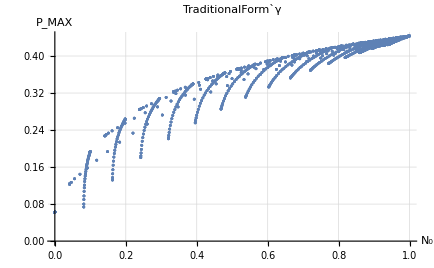

```mathematica
n=  Table[N0[θ,ϕ],{θ,0,π/2,0.05},{ϕ,0,π/2,0.05}] ;
nn= Table[FindMaxP[θ,ϕ,10^-4],{θ,0,π/2,0.05},{ϕ,0,π/2,0.05}];
ListPlot[ Join[ArrayReshape[n,{Dimensions[n][[1]]*Dimensions[n][[2]],1}],ArrayReshape[nn,{Dimensions[nn][[1]]*Dimensions[nn][[2]],1}],2],AxesOrigin->{0,0},AxesLabel->{Style[Subscript[N, 0],Large,Bold,Red],Style[Subscript[P, MAX],Large,Bold,Blue]},LabelStyle->Directive[Orange,Bold],Axes->True,Mesh->Full,GridLines->Automatic,PlotLabel->"TraditionalForm`γ"]
```

## 4bit

```mathematica
Clear[p,θ]
(*测试负熵*)
Ψ=({{Cos[θ]^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (Cos[θ] Sin[θ])/(√3), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (Cos[θ] Sin[θ])/(√3), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, (Cos[θ] Sin[θ])/(√3), 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, (Cos[θ] Sin[θ])/(√3), (Cos[θ] Sin[θ])/(√3), 0, (Cos[θ] Sin[θ])/(√3), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Sin[θ]^2/3, Sin[θ]^2/3, 0, Sin[θ]^2/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Sin[θ]^2/3, Sin[θ]^2/3, 0, Sin[θ]^2/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Sin[θ]^2/3, Sin[θ]^2/3, 0, Sin[θ]^2/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});(*某个N粒子密度矩阵*)
A00=({{1, 0}, {0, 0}});
A01=({{0, Sqrt[1-p]}, {0, 0}});
A10=({{0, 0}, {Sqrt[1-p], 0}});
A11=({{p, 0}, {0, 1-p}}); 
Gen[Ψ,A00,A01,A10,A11] ;
PPT[Gen[Ψ,A00,A01,A10,A11]] ;
Eigenvalues[PPT[Gen[Ψ,A00,A01,A10,A11]]] ;
Eigenvalues[PPT[ Ψ ]];
```

## 函数测试